```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\NumericalIntegration.m"
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BS.m"
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\Heston\\Heston.m"
```

```mathematica
Needs["PlotLegends`"]
```

# The Super Biheston Spread Risks Model

## Introduction

```mathematica
βoptimal
```

BiSabr, NormalHeston are common ways to represent a spread risk.The main problem is to have a consistent way to :
 1) - take into account the smile of the underlyings inside an arbitrage free framework, 
 2) - have additional flexibility to introduce the notion of correlation smile that can be adjusted to market data
 3) - be useable up to 40 years maturity options
 
 The final test of acceptance will be of course the stability of the hedge ratios
 
 In addition of these requirements some "nice to have" feature can also be considered:
4) - The ability to fit several maturities for the options, so allowing to have a real diffusion model, that can be used to price american deals
5)- The ability to do fit several matiurities in an autonomous way, that mean without using ime dependant coefficients, so improving forward smile behaviour, which is important for american deals
6) - The ability to have "closed form" formula for other type of options: Digitals on the underlyings, Min-Max options, Double condition options, 
7) - The ability to have additional flexibility to represent smile behaviour of the tail of the underlying beyond the usual 4 parameters framework 
 
 The Super BiHeston Framework fullfill all the requirements from 1) to 7) at a certain cost (computation time and complexity) but is very likely the only one to do so

## Specification of the model

notation

M : mean reversion
Σ_∞ : Long term variance
ρ : correlation underlying - variance
Σ : variance initial value
γ : frequency (Fourier parameters)
Y : Log of Underlying initial value
β : Relative  vol of vol ( convergence : β > 1)
τ : maturity

Variance Process

dΣ_t=(M (Σ_t-Σ_∞)+ (Σ_t-Σ_∞)M^*)dt+√Σ_t dW_t Q +Q^*dW_t^*(√Σ_t)^*

Bru shows the β>1 is enough to insure non explosion  of the model

ΩΩ^*=β Q^*Q

where

ΩΩ^*=-M Σ_∞-Σ_∞M^*

Σ_t=((Σ^11)_t | (Σ^12)_t
(Σ^12)_t | (Σ^22)_t) 3 process of variance

we note :

√Σ_t=σ_t=((σ^11)_t | (σ^12)_t
(σ^21)_t | (σ^22)_t) such that  Σ_t=σ_t σ_t^*

In the 1 dim case, we compute the vol of vol by :

Q=√(-M Σ_∞)/β

Variance Process Parameters

Initial value of the variance : Σ_0=((Σ^11)_0 | (Σ^12)_0
(Σ^21)_0 | (Σ^22)_0)

Vol of vol : Q=(ν_11 | ν_12
ν_21 | ν_22)

Mean reverting speed : M=(κ_11 | κ_12
κ_21 | κ_22)

Long term variance :  Σ_∞=(θ_11 | θ_12
θ_21 | θ_22)

M definite negative 
 Q  inversible
Σ_0 definite positive
Σ_∞ definite positive

Asset Returns

Vect[dS_(i,t)]=√Σ_t dZ_t

Covariance  asset - asset volatility

Z_(i,t)=Tr[W_t R_i^*]+B_(i,t)√(1-Tr[R_i R_i^*])   i∈{1,2}

such that  ‖R‖≤1   with  W_t et B_t   independant

we show that affinity of the process implies that {ρ_1,ρ_2}

such that  R_1=(ρ_1 | ρ_2
0 | 0)  et R_2=(0 | 0
ρ_1 | ρ_2)

## Risk Geometry

We use Einstein summation convenrtions

soit σ=√Σ

Underlying 1 Variance : projector P1

Var[Y_1]dt=<σ_(1k)dZ_k ,σ_(1m)dZ_m>=σ_(1k)σ_(1m)<dZ_k ,dZ_m>=σ_(1k)σ_(1m)δ_km dt=σ_(1k)σ_(1k)dt=Σ_11 dt

Variance of Underlying 1 Variance  :

we see that it does not work if we do not symmetrize Σ_ij dynamics : we can not get σ_(1m)σ_(1m) in factor

on a Σ_ij=σ_ik σ_jk

dY_i=(..)dt+σ_ik dZ_k

dΣ_jk=(..)dt+σ_jm dW_mn Q_nk+Q_mj dW_nm σ_kn

<dZ_k ,dW_mn> =R_(k,mn)dt=δ_km(δ_(n 1)ρ_1+δ_n2 ρ_2) dt

donc

Var[Σ_11]dt=<σ_(1m)dW_mn Q_n1+Q_m1 dW_nm σ_(1n) ,σ_(1u)dW_uv Q_v1+Q_u1 dW_vu σ_(1v)> =
<σ_(1m)dW_mn Q_n1 ,σ_(1u)dW_uv Q_v1>+
<σ_(1m)dW_mn Q_n1 ,Q_u1 dW_vu σ_(1v)>+
<Q_m1 dW_nm σ_(1n) ,σ_(1u)dW_uv Q_v1>+
<Q_m1 dW_nm σ_(1n) ,Q_u1 dW_vu σ_(1v)>

=σ_(1m)Q_n1 σ_(1u)Q_v1<dW_mn ,dW_uv>+σ_(1m)Q_n1 Q_u1 σ_(1v)<dW_mn ,dW_vu>+Q_m1 σ_(1n) σ_(1u)Q_v1<dW_nm,dW_uv>+Q_m1 σ_(1n)Q_u1 σ_(1v)<dW_nm ,dW_vu>

=σ_(1m)Q_n1 σ_(1u)Q_v1 δ_mu δ_nv+
σ_(1m)Q_n1 Q_u1 σ_(1v)δ_mv δ_nu+
Q_m1 σ_(1n) σ_(1u)Q_v1 δ_nu δ_mv+
Q_m1 σ_(1n)Q_u1 σ_(1v)δ_nv δ_mu

=σ_(1m)Q_n1 σ_(1m)Q_n1+
σ_(1m)Q_n1 Q_n1 σ_(1m)+
Q_m1 σ_(1n) σ_(1n)Q_m1+
Q_m1 σ_(1n)Q_m1 σ_(1n)

=σ_(1m)σ_(1m)(Q_n1 Q_n1+Q_n1 Q_n1+Q_m1 Q_m1+Q_m1 Q_m1)=4 Σ_11(Q_11^2+Q_12^2)

Covariance entre  l' underlying i  et la variance de  l' underlying 1 :

Covar[Y_i,Σ_11] dt =<σ_ik dZ_k ,σ_(1u)dW_uv Q_v1+Q_u1 dW_vu σ_(1v)> =
<σ_ik dZ_k ,σ_(1u)dW_uv Q_v1>+<σ_ik dZ_k ,Q_u1 dW_vu σ_(1v)> =
σ_ik σ_(1u)Q_v1<dZ_k ,dW_uv>+σ_ik Q_u1 σ_(1v)<dZ_k ,dW_vu> =
σ_ik σ_(1u)Q_v1 R_(k,uv)+σ_ik Q_u1 σ_(1v)R_(k,v,u) =

#### Affinité

Il est necessaire que l covariance entre Y_i et Σ_11 soit lineaire en Σ_11 (et ou Y_i mais ici , cela n'apparait pas)

donc il faut que

σ_ik σ_(1u)Q_v1 R_(k,uv)+σ_ik Q_u1 σ_(1v)R_(k,v,u)  soit une fonction de Σ_(1i)

c'est a dire Q_v1 R_(k,uv) doit etre null pour k et u different 
et en plus pour k =u , on doit avoir le meme coefficient quelque soit u , appelons le ρ_k

#### Covariance

donc

=σ_ik σ_(1u)Q_v1(δ_ku(δ_(v 1)ρ_1+δ_v2 ρ_2))+σ_ik Q_u1 σ_(1v)(δ_kv(δ_(u 1)ρ_1+δ_u2 ρ_2))=
σ_ik σ_(1u)Q_v1(δ_ku(δ_(v 1)ρ_1))+
σ_ik σ_(1u)Q_v1(δ_ku(δ_v2 ρ_2))+
σ_ik Q_u1 σ_(1v)(δ_kv(δ_(u 1)ρ_1))+
σ_ik Q_u1 σ_(1v)(δ_kv(δ_u2 ρ_2))

=σ_ik σ_(1k)Q_11 ρ_1+
σ_ik σ_(1k)Q_21 ρ_2+
σ_ik Q_11 σ_(1k)ρ_1+
σ_ik Q_21 σ_(1k)ρ_2

=Σ_(1i)Q_11 ρ_1+Σ_(1i)Q_21 ρ_2+Σ_(1i)Q_11 ρ_1+Σ_(1i)Q_21 ρ_2=
2 Σ_(1i)(Q_11 ρ_1+Q_21 ρ_2)

Correspondance Heston / BiHeston (Risque)

dY_1=(..)dt+√Σ_1 dP_1

dΣ_1 = (..)dt+ν_1 √Σ_1 dQ_1

On a donc les equations suivantes :

Var[dY_1]=Σ_1 dt

donc c' est la meme normalization de la vol

Var[dΣ_1 ]=ν_1^2 Σ_1 dt

Covar[dY_1,dΣ_1]=ρ_s1 ν_1 Σ_1

on a donc

ρ_s1 ν_1=(Q_11 ρ_1+Q_21 ρ_2)/2
ρ_s2 ν_2=(Q_12 ρ_1+Q_22 ρ_2)/2

ν_1^2/4=Q_11^2+Q_21^2
ν_2^2/4=Q_12^2+Q_22^2

Correspondance Heston / BiHeston (Drift)

On a

Ω Ω^*=β Q^*Q=β (Q_11^2+Q_21^2)

le drift de dΣ_11 est : (β (Q_11^2+Q_21^2) +2(M_11 Σ_11+M_21 Σ_12))dt

celui de dΣ_1 est λ_1(Σ_(∞1)-Σ_1)dt

donc on a les equations :

β (Q_11^2+Q_21^2) +2 M_21 Σ_12 = λ_1 Σ_(∞1)

2 M_11=-λ_1

β (Q_12^2+Q_22^2) +2 M_12 Σ_21 = λ_2 Σ_(∞2)

M_12=(λ_2 Σ_(∞2)-β (Q_12^2+Q_22^2))/(2 Σ_12)

M_21=(λ_1 Σ_(∞1)-β (Q_21^2+Q_11^2))/(2 Σ_12)

2 M_22=-λ_2

mais on n'oublie pas que Σ_21=Σ_12

On a donc , au total :

M=(-λ_1/2 | (λ_2 Σ_(∞2)-β (Q_12^2+Q_22^2))/(2 Σ_12)
(λ_1 Σ_(∞1)-β (Q_21^2+Q_11^2))/(2 Σ_12) | -λ_2/2)

## Transformé de fourier du payoff Vanille

We start computing the option for K > 0, then we will use conversion formula to deduce the case K < 0

But the payoff does not belong to a suitable space of functions so we decompose the payoff in two and formulate a fourier transformation theory with  specific shift in the fourier plane for each part :

```mathematica
PayOff[x1_,x2_,K_,α_,β_]:=Max[(α ⅇ^x1-β ⅇ^x2-K),0]
```

PayOff[x1, x2, K] == PayOff_1[x1, x2, K] + PayOff_2[x1, x2, K]

ou PayOff_1[x1,x2,K]=Max[(ⅇ^x1-ⅇ^x2-K),0]1_(x2>0)   et PayOff_2[x1,x2,K]=Max[(ⅇ^x1-ⅇ^x2-K),0]1_(x2<0)

CompleteFourierPayOffDroite  implements the fourier transform of PayOff_ 1

CompleteFourierPayOffGauche  implements the fourier transform of PayOff_ 2

The  Fourier Transform of PayOff[x1, x2, K] is therefore the sum of both

The case K == 0  is much simpler. It is handled separatly.

The computations are done in annex 1

```mathematica
CompleteFourierPayOffDroite[k1_,k2_,K_]:=K^(ⅈ k1)/(k1 (-ⅈ+k1) k2 (-ⅈ+k2))( K^(ⅈ k2+1)/Gamma[-ⅈ k1] ( 
(1+ⅈ k2) Gamma[1+ⅈ k2] ( Gamma[-ⅈ (k1+k2)])+ⅈ  k2 Gamma[2+ⅈ k2] (  Gamma[-ⅈ (-ⅈ+k1+k2)]))-
  (ⅈ  k2 Hypergeometric2F1[-ⅈ k1,1+ⅈ k2,2+ⅈ k2,-1/K]+K (1+ⅈ k2) Hypergeometric2F1[-ⅈ k1,ⅈ k2,1+ⅈ k2,-1/K]))
```

```mathematica
CompleteFourierPayOffDroite[k1_,k2_,K_,α_,β_]:=-((k1 (α-β)+ⅈ β)Hypergeometric2F1[-ⅈ k1,-ⅈ (-ⅈ+k1+k2),-ⅈ (k1+k2),-K])/(k1 (-ⅈ+k1)   (-ⅈ+k1+k2))-(K (ⅈ+k1 (-1+α)) ⅈ  Hypergeometric2F1[-ⅈ k1,-ⅈ (k1+k2),-ⅈ (ⅈ+k1+k2),-K])/(ⅈ (k1+k2)k1 (-ⅈ+k1))
```

```mathematica
{CompleteFourierPayOffDroite[1.1,2.2,0.1],CompleteFourierPayOffDroite[1.1,2.2,0.1,1,1]}
```

{0.180133-0.089615 ⅈ,0.180133-0.089615 ⅈ}

```mathematica
CompleteFourierPayOffDroite[k1_,k2_]:=1/(k1 (-ⅈ+k1) (1+ⅈ k1+ⅈ k2))
```

```mathematica
CompleteFourierPayOffDroite[k1_,k2_,α_,β_]:=(-(k1 (α-β)+ⅈ β))/(k1 (-ⅈ+k1) (-ⅈ+k1+k2))
```

```mathematica
{CompleteFourierPayOffDroite[1.17,2.2],CompleteFourierPayOffDroite[1.17,2.2,1,1]}
```

{0.13256-0.0859277 ⅈ,0.13256-0.0859277 ⅈ}

```mathematica
CompleteFourierPayOffGauche[k1_,k2_,K_]:=K^(ⅈ k1)/(k1 (-ⅈ+k1) k2 (-ⅈ+k2))  (ⅈ  k2 Hypergeometric2F1[-ⅈ k1,1+ⅈ k2,2+ⅈ k2,-1/K]+K (1+ⅈ k2) Hypergeometric2F1[-ⅈ k1,ⅈ k2,1+ⅈ k2,-1/K])
```

```mathematica
CompleteFourierPayOffGauche[k1_,k2_,K_,α_,β_]:=1/((-1-ⅈ k1) k1 k2 (-ⅈ+k2)) K^(ⅈ k1) ( k2 (-ⅈ k1 (α-β)+β) Hypergeometric2F1[-ⅈ k1,1+ⅈ k2,2+ⅈ k2,-1/K]+K (-ⅈ+k2) (1-ⅈ k1 (-1+α)) Hypergeometric2F1[-ⅈ k1,ⅈ k2,1+ⅈ k2,-1/K])
```

```mathematica
CompleteFourierPayOffGauche[k1_,k2_,K_,α_,β_]:=1/((-1-ⅈ k1) k1 k2 (-ⅈ+k2)) (k2 (-ⅈ k1 (α-β)+β) (((K)^(1+ⅈ k1+ⅈ k2) Gamma[-1-ⅈ k1-ⅈ k2] Gamma[2+ⅈ k2])/Gamma[-ⅈ k1]+((1+ⅈ k2)  Hypergeometric2F1[-ⅈ k1,-1-ⅈ k1-ⅈ k2,-ⅈ k1-ⅈ k2,-K])/(1+ⅈ k1+ⅈ k2))+ (-ⅈ+k2) (1-ⅈ k1 (-1+α)) (((K)^(1+ⅈ k1+ⅈ k2) Gamma[-ⅈ k1-ⅈ k2] Gamma[1+ⅈ k2])/Gamma[-ⅈ k1]+((K) ⅈ k2  Hypergeometric2F1[-ⅈ k1,-ⅈ k1-ⅈ k2,1-ⅈ k1-ⅈ k2,-K])/(ⅈ k1+ⅈ k2)))
```

```mathematica
CompleteFourierPayOffGauche[k1_,k2_,K_,α_,β_]:=Module[{a0=(K)^(1+ⅈ k1+ⅈ k2),g1= Gamma[-1-ⅈ k1-ⅈ k2],g2=Gamma[1+ⅈ k2],g3=Gamma[-ⅈ k1]},
1/((-1-ⅈ k1) k1 k2 (-ⅈ+k2)) (k2 (-ⅈ k1 (α-β)+β) ((a0 g1 g2(1+ⅈ k2))/g3+((1+ⅈ k2)  Hypergeometric2F1[-ⅈ k1,-1-ⅈ k1-ⅈ k2,-ⅈ k1-ⅈ k2,-K])/(1+ⅈ k1+ⅈ k2))+ (-ⅈ+k2) (1-ⅈ k1 (-1+α)) ((a0 g1(-1-ⅈ k1-ⅈ k2) g2)/g3+((K) ⅈ k2  Hypergeometric2F1[-ⅈ k1,-ⅈ k1-ⅈ k2,1-ⅈ k1-ⅈ k2,-K])/(ⅈ k1+ⅈ k2)))
]
```

```mathematica
{CompleteFourierPayOffGauche[1.17,2.2,0.1],CompleteFourierPayOffGauche[1.17,2.2,0.1,1,1]}
```

{-0.158254+0.0845554 ⅈ,-0.158254+0.0845554 ⅈ}

```mathematica
CompleteFourierPayOffGauche[k1_,k2_]:=-1/(k1 (-ⅈ+k1) (1+ⅈ k1+ⅈ k2))
```

```mathematica
CompleteFourierPayOffGauche[k1_,k2_,α_,β_]:=(k1 (α-β)+ⅈ β)/(k1 (-ⅈ+k1) (-ⅈ+k1+k2))
```

```mathematica
{CompleteFourierPayOffGauche[1.17,2.2],CompleteFourierPayOffGauche[1.17,2.2,1,1]}
```

{-0.13256+0.0859277 ⅈ,-0.13256+0.0859277 ⅈ}

When the strike get higher than 1 , we can use the following rule :

```mathematica
RuleHyper={Hypergeometric2F1[a_,b_,c_,z_]->(Gamma[b-a] Gamma[c])/(Gamma[b]Gamma[c-a])(-z)^-a Hypergeometric2F1[a,a-c+1,a-b+1,1/z]+(Gamma[a-b] Gamma[c])/(Gamma[a] Gamma[c-b])(-z)^-b Hypergeometric2F1[b,b-c+1,b-a+1,1/z]};
```

## Laplace transform of the propagator of the process

by Feynman Kac :

L=TR[(Ω Ω^*+M Σ +Σ M)D +(Σ D Q^* Q D)/2]+1/2∇_Y Σ  (∇_Y)^*+Tr[D Q^*ρ ∇_Y Σ]-1/2 Vec[Σ_ii]∇_Y

the  security price  verifies :

{-(∂ P)/(∂t)=L p
p[0]=(S_1 ⅇ^Y_1-S_2 ⅇ^Y_2-K)^+

then 
E[(S_1 ⅇ^(Y_(1,T))-S_2 ⅇ^(Y_(2,T))-K)^+]=(S_1 S_2)/(2π)^2∫_(ⅈ γ-∞)^(ⅈ γ+∞) ⅇ^(-2ⅈ ( Y_1 γ_1+Y_2 γ_2))q[-ⅈ γ_1,-ⅈ γ_2]ⅆ γ_1ⅆ γ_2

we assume for non explosion purposes (see Bru 1987)

Q Q^*=(-2 M Σinf)/β

The laplace transform of the  probability transition is affine with coefficients A and c  q[γ_1,γ_2]==E[exp[<γ,Y>]]==exp[Tr[A.Σ]+γ^T.Y+c]

we can show (see Fonseca 2007)

{(∂c[τ])/(∂τ)=M θ A[τ]
(∂A[τ])/(∂τ)=(Q Q^*)/2 A[τ]^2 +A[τ] M+M^* A[τ]+  γ ρ^* Q A[τ]+  A[τ]Q^* ρ γ^* +(γ γ^*)/2

that we can solve by linearizing the flow when we double the space dimension.

## Solution of a Riccati

We want to solve:         dA=(A a2 A+a1 A +A a1s + a0)dt

let  A[τ] = F^-1 G   soit G=F A
Then  d[F A]=dF A +F dA=dG

dA = (A a2 A + a1 A + A a1s + a0) dt

dG = F  dA + dF A = (F A a2 A + F a1 A + F A a1s + F a0) dt + dF  A

dG = (G a2 A + F a1 A + G a1s + F a0) dt + dF  A

We split:

( G a1s + F a0) dt = dG
(G a2 + F a1  ) dt + dF  = 0

then dF = ( -  F a1 - G a2) dt  et dG = ( G a1s  +  F a0) dt

therefore   d(F,G) =(F,G) . (-a1 | a0
-a2 | a1s)dt

and we can use matrix exponentiation to deduce the solution of the system

### Computation of A

{F,G} . (-a1 | a0
-a2 | a1s)

{-a1 F - a2 G, a0 F + a1s G}

a2=(Q Q^*)/2;a1=M^*+ γ ρ^* Q;a1s=M+Q^* ρ γ^*;a0=(γ γ^*)/2

initial condition  A[0] = 0  soit F = 1 et G = 0

then   {F,G} ={1,0}  . Exp[(-a1 | a0
-a2 | a1s)]

then (F
G)=Transpose[Exp[(-a1 | a0
-a2 | a1s)]] . (1
0)

then (F
G)=Exp[Transpose[(-a1 | a0
-a2 | a1s)]] . (1
0)=Exp[(-a1 | -a2
a0 | a1s)] . (1
0)

{{a11, a12}, {a21, a22}} . {1, 0}

{a11, a21}

A=a11^-1 a21

### Computation of c

dc =Tr[-β^2 QQ^*A]dt

but

dG=( G a1s  +  F a0) dt=( F(γ γ)/2 + G ((M+Q^* ρ γ^*)/2) )dt

dF =( -  F a1 - G a2) dt=-F ((M^*+γ R Q)/2)-G (Q^*Q)/2

where  a2=(Q Q^*)/2;a1=M^*+ γ ρ^* Q;a1s=M+Q^* ρ γ^*;a0=(γ γ^*)/2

we get:

G=-2(dF/dt+F ((M^*+γ R Q)/2))(Q^*Q)^-1

we multiplies by F

A=F^-1 G=-2(F^-1 dF/dt+ ((M^*+γ R Q)/2))(Q^*Q)^-1

then

dc =-2 β^2 Tr[ (F^-1 dF/dτ+ ((M^*+γ R Q)/2))]dτ

Using trace properties

c=-2 β^2 Tr[ (Log[F]+ ((M^*+γ R Q)/2)τ)]

## Handling of the gap at the money

Due to integration difficulty , the call put conversion relationship which is used to compute the K < 0 cases can lead to discontinuities of the smile at the money and if we handle the discontinuity, to discontinuity of the derivatives. To take care of them, we start from the T = 0 relationship that should have no discontinuity :

(S1-S2-K)^+=(S1-S2-K)+(S2-S1-(-K))^+

Obviously this relationship is continuous and has the same continuous derivatives in K > 0

(ⅇ^x1-ⅇ^x2-K)^+=(ⅇ^x1-ⅇ^x2)^+-(ⅇ^x2-ⅇ^x1)^+-K+(ⅇ^x2-ⅇ^x1-(-K))^+

let f[x1,x2,K]≡1_(K>0)(ⅇ^x1-ⅇ^x2-K)^++1_(K<0)((ⅇ^x1-ⅇ^x2)^+-(ⅇ^x2-ⅇ^x1)^+-K+(ⅇ^x2-ⅇ^x1-(-K))^+)

we have

f[x1,x2,K]==(ⅇ^x1-ⅇ^x2-K)^+   for all K ∈ℜ

but we use the definition of F to compute its fourier transform

#### Theory of special fourier operators to handle the K > 0 cases

Let 𝔉_(λ1,λ2) the special fourier transform that regularize with λ1 and λ2 the functions like g[x1,x2]=(ⅇ^x1-ⅇ^x2-K)^+and make them convergent:

𝔉_(λ1,λ2)[g][k1,k2]=(∫_(-∞)^∞ (ⅇ^(ⅈ (k1 +ⅈ λ1)x1+ⅈ( k2 -ⅈ λ2)x2)1_(x2<0))g[x1,x2]ⅆx1ⅆx2
∫_(-∞)^∞ (ⅇ^(ⅈ (k1 +ⅈ λ1)x1+ⅈ( k2 +ⅈ λ2)x2)1_(x2>0))g[x1,x2]ⅆx1ⅆx2)

We have the inverse fourier transform :

𝔊_(λ1,λ2)[(h1
h2)][x1,x2]=1/(2π)∫_(-∞)^∞ (ⅇ^(-ⅈ (k1 +ⅈ λ1)x1-ⅈ( k2 -ⅈ λ2)x2))h1[k1,k2]ⅆk1ⅆk2+1/(2π)∫_(-∞)^∞ (ⅇ^(-ⅈ (k1 +ⅈ λ1)x1-ⅈ( k2 +ⅈ λ2)x2))h2[k1,k2]ⅆk1ⅆk2

that we can justify by saying that we analyze separately  the 1_(x2<0)part and the 1_(x2>0)part

we can check that

𝔊_(λ1,λ2)(◦𝔉)_(λ1,λ2)[g] = g

let

g_c[K]=(ⅇ^x1-ⅇ^x2-K)^+

g_p[K]=(ⅇ^x1-ⅇ^x2)^+-(ⅇ^x2-ⅇ^x1)^+-K+(ⅇ^x2-ⅇ^x1-(-K))^+

g_f=(ⅇ^x1-ⅇ^x2)^+-(ⅇ^x2-ⅇ^x1)^+

having analytic closed forms for 𝔉_(λ1,λ2)[g_c]:

𝔉_(λ1,λ2)[g_c]==((K^(ⅈ k1) (ⅈ  k2 Hypergeometric2F1[-ⅈ k1,1+ⅈ k2,2+ⅈ k2,-1/K]+K (1+ⅈ k2) Hypergeometric2F1[-ⅈ k1,ⅈ k2,1+ⅈ k2,-1/K]))/(k1 (-ⅈ+k1) k2 (-ⅈ+k2)) /. {k1→k1+ⅈ λ1,k2→k2-ⅈ λ2}
K^(ⅈ k1)/(k1 (-ⅈ+k1) k2 (-ⅈ+k2))( K^(ⅈ k2+1)/Gamma[-ⅈ k1] ( (1+ⅈ k2) Gamma[1+ⅈ k2] ( Gamma[-ⅈ (k1+k2)])+ⅈ  k2 Gamma[2+ⅈ k2] (  Gamma[-ⅈ (-ⅈ+k1+k2)]))-
  (ⅈ  k2 Hypergeometric2F1[-ⅈ k1,1+ⅈ k2,2+ⅈ k2,-1/K]+K (1+ⅈ k2) Hypergeometric2F1[-ⅈ k1,ⅈ k2,1+ⅈ k2,-1/K])) /. {k1→k1+ⅈ λ1,k2→k2+ⅈ λ2})

𝔉_(λ1,λ2)[g_f]==(-1/(k1 (-ⅈ+k1) (1+ⅈ k1+ⅈ k2)) /. {k1→k1+ⅈ λ1,k2→k2-ⅈ λ2}
1/(k1 (-ⅈ+k1) (1+ⅈ k1+ⅈ k2)) /. {k1→k1+ⅈ λ1,k2→k2+ⅈ λ2})

```mathematica
Fλ1λ2gc[k1_,k2_,λ1_,λ2_,K_]:={(K^(ⅈ (k1+ⅈ λ1)) (ⅈ (k2-ⅈ λ2) Hypergeometric2F1[-ⅈ (k1+ⅈ λ1),1+ⅈ (k2-ⅈ λ2),2+ⅈ (k2-ⅈ λ2),-1/K]+K (1+ⅈ (k2-ⅈ λ2)) Hypergeometric2F1[-ⅈ (k1+ⅈ λ1),ⅈ (k2-ⅈ λ2),1+ⅈ (k2-ⅈ λ2),-1/K]))/((k1+ⅈ λ1) (-ⅈ+(k1+ⅈ λ1)) (k2-ⅈ λ2) (-ⅈ+(k2-ⅈ λ2))),1/((k1+ⅈ λ1) (-ⅈ+(k1+ⅈ λ1)) (k2+ⅈ λ2) (-ⅈ+(k2+ⅈ λ2)))K^(ⅈ (k1+ⅈ λ1)) (1/Gamma[-ⅈ (k1+ⅈ λ1)] K^(ⅈ (k2+ⅈ λ2)+1) ((1+ⅈ (k2+ⅈ λ2)) Gamma[1+ⅈ (k2+ⅈ λ2)] Gamma[-ⅈ ((k1+ⅈ λ1)+(k2+ⅈ λ2))]+ⅈ (k2+ⅈ λ2) Gamma[2+ⅈ (k2+ⅈ λ2)] Gamma[-ⅈ (-ⅈ+(k1+ⅈ λ1)+(k2+ⅈ λ2))])-(ⅈ (k2+ⅈ λ2) Hypergeometric2F1[-ⅈ (k1+ⅈ λ1),1+ⅈ (k2+ⅈ λ2),2+ⅈ (k2+ⅈ λ2),-1/K]+K (1+ⅈ (k2+ⅈ λ2)) Hypergeometric2F1[-ⅈ (k1+ⅈ λ1),ⅈ (k2+ⅈ λ2),1+ⅈ (k2+ⅈ λ2),-1/K]))}
```

```mathematica
Fλ1λ2gf[k1_,k2_,λ1_,λ2_]:={-1/((k1+ⅈ λ1) (-ⅈ+(k1+ⅈ λ1)) (1+ⅈ (k1+ⅈ λ1)+ⅈ (k2-ⅈ λ2))),1/((k1+ⅈ λ1) (-ⅈ+(k1+ⅈ λ1)) (1+ⅈ (k1+ⅈ λ1)+ⅈ (k2+ⅈ λ2)))}
```

```mathematica
Module[{k1=1,k2=1,λ1=1.1,λ2=1.2},Fλ1λ2gf[k1,k2,λ1,λ2]]
```

{0.122192+0.266569 ⅈ,-0.280064-0.0173219 ⅈ}

```mathematica
Module[{k1=1,k2=1,λ1=1.1,λ2=1.2},Fλ1λ2gc[k1,k2,λ1,λ2,0.0001]]
```

{0.122168+0.266592 ⅈ,-0.280067-0.0173439 ⅈ}

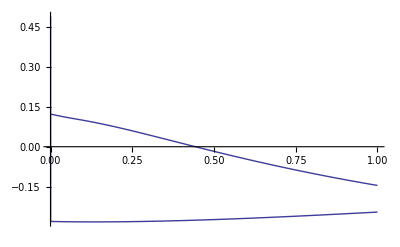

```mathematica
Module[{k1=1,k2=1,λ1=1.1,λ2=1.2},Plot[Re[Fλ1λ2gc[k1,k2,λ1,λ2,K]],{K,0,1}]]
```

on a bien convergence

Lim_(K→0) 𝔉_(λ1,λ2)[g_c[K]]=𝔉_(λ1,λ2)[g_f]

Differentiability at K = 0

(∂g_c[K])/(∂K)=(∂(ⅇ^x1-ⅇ^x2-K)^+)/(∂K)=(∂((ⅇ^x1-ⅇ^x2-K)θ[ⅇ^x1-ⅇ^x2-K]))/(∂K)=(∂(ⅇ^x1-ⅇ^x2-K))/(∂K)θ[ⅇ^x1-ⅇ^x2-K]+(ⅇ^x1-ⅇ^x2-K)(∂(θ[ⅇ^x1-ⅇ^x2-K]))/(∂K)=-θ[ⅇ^x1-ⅇ^x2-K]-(ⅇ^x1-ⅇ^x2-K)δ[ⅇ^x1-ⅇ^x2-K]

assume two different definitions of f ,for K>0 and K<0 :

f[K] = θ[K] fp[K] + (1 - θ[K]) fn[K] = fn[K] + θ[K] (fp[K] - fn[K])

(∂f[K])/(∂K)=(∂fn[K])/(∂K)+θ[K](∂(fp[K]-fn[K]))/(∂K)+(fp[K]-fn[K])δ[K]

we have  fn[x1, x2, K] = ΔS - K + fp[x2, x1, -K]

So

(∂f[K])/(∂K)=-1-(∂fp[x2,x1,-K])/(∂K)+θ[K](∂(fp[x1,x2,K]+1+fp[x2,x1,-K]))/(∂K)+(fp[x1,x2,K]-(ΔS-K+fp[x2,x1,-K]))δ[K]

(∂f[K])/(∂K)=θ[K](∂fp[x1,x2,K])/(∂K)-(1-θ[K])(∂fp[x2,x1,-K])/(∂K)+(fp[x1,x2,K]-(ΔS-K+fp[x2,x1,-K]))δ[K]

(∂f[K])/(∂K)=1_(K>0)(∂fp[x1,x2,K])/(∂K)-1_(K<0)(∂fp[x2,x1,-K])/(∂K)+(fp[x1,x2,K]-(ΔS-K+fp[x2,x1,-K]))δ[K]

let suppose  ΔS = fp[x1, x2, 0] - fp[x2, x1, 0]

then

(((∂f[x1,x2,K])/(∂K)|)_(0+)=(∂f[x1,x2,K])/(∂K)|)_(0-)+((∂fp[x1,x2,0])/(∂K)-(∂fp[x2,x1,0])/(∂K))

but we have fp[x1,x2,K]=g_c[K]

(∂g_c[K])/(∂K)=(∂(ⅇ^x1-ⅇ^x2-K)^+)/(∂K)=(∂((ⅇ^x1-ⅇ^x2-K)θ[ⅇ^x1-ⅇ^x2-K]))/(∂K)=(∂(ⅇ^x1-ⅇ^x2-K))/(∂K)θ[ⅇ^x1-ⅇ^x2-K]+(ⅇ^x1-ⅇ^x2-K)(∂(θ[ⅇ^x1-ⅇ^x2-K]))/(∂K)=-θ[ⅇ^x1-ⅇ^x2-K]-(ⅇ^x1-ⅇ^x2-K)δ[ⅇ^x1-ⅇ^x2-K]

```mathematica
and
```

```mathematica
((∂fp[x1,x2,0])/(∂K)-(∂fp[x2,x1,0])/(∂K))=-θ[ⅇ^x1-ⅇ^x2]-(ⅇ^x1-ⅇ^x2)δ[ⅇ^x1-ⅇ^x2]-(-θ[ⅇ^x2-ⅇ^x1]-(ⅇ^x2-ⅇ^x1)δ[ⅇ^x2-ⅇ^x1])
```

```mathematica
let ΔS=ⅇ^x1-ⅇ^x2
```

```mathematica
((∂fp[x1,x2,0])/(∂K)-(∂fp[x2,x1,0])/(∂K))=-θ[ΔS]-(ΔS)δ[ΔS]-(-θ[-ΔS]-(-ΔS)δ[-ΔS])=-θ[ΔS]-(ΔS)δ[ΔS]-(-(1-θ[ΔS])-(-ΔS)δ[ΔS])=
-θ[ΔS]-ΔSδ[ΔS]-(-1+θ[ΔS]+ΔS δ[ΔS])=-θ[ΔS]-ΔSδ[ΔS]+1-θ[ΔS]-ΔS δ[ΔS]=1
```

```mathematica
f[ΔS_]:=-HeavisideTheta[ΔS]-ΔS DiracDelta[ΔS]
```

```mathematica
Simplify[f[ΔS]-f[-ΔS]]
```

HeavisideTheta[-ΔS]-HeavisideTheta[ΔS]

```mathematica
=1-2θ[ΔS]
```

```mathematica
f[S_,K_]:=Max[S-K,0]
```

```mathematica
h=(D[f[S,K],K] -D[f[-S,K],K] )/. K->0
```

Piecewise[{{-1, -S<0}}]-Piecewise[{{-1, S<0}}]

```mathematica
FullForm[h]
```

Plus[Piecewise[List[List[-1,Less[Times[-1,S],0]]],0],Times[-1,Piecewise[List[List[-1,Less[S,0]]],0]]]

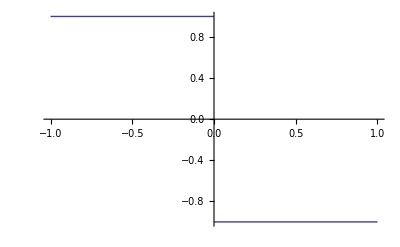

```mathematica
Plot[h,{S,-1,1}]
```

## Implementation

Therefore we can write a first version of the propagator

```mathematica
SuperBiHestonLaplaceTransform[M_,{{θ11_,θ12_},{θ12_,θ22_}},ρ_,{{Σ11_,Σ12_},{Σ12_,Σ22_}},γ_,β_,τ_]:=
Module[{H,EXPH,A11,A21,A,Q,ν11,ν12,ν21,ν22,c,Σ=({{Σ11, Σ12}, {Σ12, Σ22}}),ΣinfM=({{θ11, θ12}, {θ12, θ22}}),
Placement1={{1,0,0,0},{0,1,0,0}},Placement2={{0,0,1,0},{0,0,0,1}}},
Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;

H=Transpose[Placement1] .((-( M+Transpose[Q].Outer[Times,ρ,γ]))/2).Placement1+
Transpose[Placement1] .(-Transpose[Q]. Q/2).Placement2+
Transpose[Placement2] . (1/2(Outer[Times,γ,γ]-DiagonalMatrix[γ] )).Placement1+
Transpose[Placement2] . (Transpose[(M+Transpose[Q].Outer[Times,ρ,γ])/2]).Placement2 ; 
EXPH=MatrixExp[τ H];
A11={{EXPH[[1,1]],EXPH[[1,2]]},{EXPH[[2,1]],EXPH[[2,2]]}};
A21={{EXPH[[3,1]],EXPH[[3,2]]},{EXPH[[4,1]],EXPH[[4,2]]}};
A=Inverse[A11] .A21;
c=-2 β^2(Tr[MatrixLog2[A11]+τ/2 (Transpose[M]+Outer[Times,γ,ρ].Q)]); (*c=-β/2 Tr[Log[A22]+τ (Transpose[M]+Outer[Times,γ,ρ].Q)];*)
Exp[Tr[A . Σ]+c]
]
```

the problem of this version is that Q is recomputed insde the procedure that will be called at evry node (γ1, γ2), so we optimize the procedure by externalizing the computation of Q and precomputing all the matrix algebra :

```mathematica
SuperBiHestonLaplaceTransformReduced[{{M11_,M12_},{M21_,M22_}},{{Q11_,Q12_},{Q21_,Q22_}},{ρ1_,ρ2_},{{Σ11_,Σ12_},{Σ21_,Σ22_}},{γ1_,γ2_},β_,τ_]:=
Module[{EXPH=MatrixExp[τ{{1/2 (-M11-Q11 γ1 ρ1-Q21 γ1 ρ2),1/2 (-M12-Q11 γ2 ρ1-Q21 γ2 ρ2),1/2 (-Q11^2-Q21^2),1/2 (-Q11 Q12-Q21 Q22)},{1/2 (-M21-Q12 γ1 ρ1-Q22 γ1 ρ2),1/2 (-M22-Q12 γ2 ρ1-Q22 γ2 ρ2),1/2 (-Q11 Q12-Q21 Q22),1/2 (-Q12^2-Q22^2)},{1/2 (-1+γ1) γ1,(γ1 γ2)/2,1/2 (M11+Q11 γ1 ρ1+Q21 γ1 ρ2),1/2 (M21+Q12 γ1 ρ1+Q22 γ1 ρ2)},{(γ1 γ2)/2,1/2 (-1+γ2) γ2,1/2 (M12+Q11 γ2 ρ1+Q21 γ2 ρ2),1/2 (M22+Q12 γ2 ρ1+Q22 γ2 ρ2)}}],δ},
δ=-EXPH[[1,2]] EXPH[[2,1]]+EXPH[[1,1]] EXPH[[2,2]];
Exp[1/δ(EXPH[[2,2]] EXPH[[3,1]] Σ11-EXPH[[1,2]] EXPH[[4,1]] Σ11-EXPH[[2,1]] EXPH[[3,1]] Σ12+EXPH[[2,2]] EXPH[[3,2]] Σ12+
EXPH[[1,1]] EXPH[[4,1]] Σ12-EXPH[[1,2]] EXPH[[4,2]] Σ12-EXPH[[2,1]] EXPH[[3,2]] Σ22+EXPH[[1,1]] EXPH[[4,2]] Σ22)-2 β^2(Log[δ]+τ/2( M11+M22+Q11 γ1 ρ1+Q12 γ2 ρ1+Q21 γ1 ρ2+Q22 γ2 ρ2))]
]
```

the same procedure but where' underlying 1 is echanged with  underlying 2

```mathematica
SuperBiHestonLaplaceTransformReduced2[{{M22_,M21_},{M12_,M11_}},{{Q22_,Q21_},{Q12_,Q11_}},{ρ2_,ρ1_},{{Σ22_,Σ21_},{Σ12_,Σ11_}},{γ1_,γ2_},β_,τ_]:=
Module[{EXPH=MatrixExp[τ{{1/2 (-M11-Q11 γ1 ρ1-Q21 γ1 ρ2),1/2 (-M12-Q11 γ2 ρ1-Q21 γ2 ρ2),1/2 (-Q11^2-Q21^2),1/2 (-Q11 Q12-Q21 Q22)},{1/2 (-M21-Q12 γ1 ρ1-Q22 γ1 ρ2),1/2 (-M22-Q12 γ2 ρ1-Q22 γ2 ρ2),1/2 (-Q11 Q12-Q21 Q22),1/2 (-Q12^2-Q22^2)},{1/2 (-1+γ1) γ1,(γ1 γ2)/2,1/2 (M11+Q11 γ1 ρ1+Q21 γ1 ρ2),1/2 (M21+Q12 γ1 ρ1+Q22 γ1 ρ2)},{(γ1 γ2)/2,1/2 (-1+γ2) γ2,1/2 (M12+Q11 γ2 ρ1+Q21 γ2 ρ2),1/2 (M22+Q12 γ2 ρ1+Q22 γ2 ρ2)}}],δ},
δ=-EXPH[[1,2]] EXPH[[2,1]]+EXPH[[1,1]] EXPH[[2,2]];
Exp[1/δ(EXPH[[2,2]] EXPH[[3,1]] Σ11-EXPH[[1,2]] EXPH[[4,1]] Σ11-EXPH[[2,1]] EXPH[[3,1]] Σ12+EXPH[[2,2]] EXPH[[3,2]] Σ12+
EXPH[[1,1]] EXPH[[4,1]] Σ12-EXPH[[1,2]] EXPH[[4,2]] Σ12-EXPH[[2,1]] EXPH[[3,2]] Σ22+EXPH[[1,1]] EXPH[[4,2]] Σ22)-2 β^2(Log[δ]+τ/2( M11+M22+Q11 γ1 ρ1+Q12 γ2 ρ1+Q21 γ1 ρ2+Q22 γ2 ρ2))]
]
```

In annex , we write the 1 dimension case, and compare it with the known Heston formula. it tests and verifies the matrix exponential method for solving the riccati equation

## Computation of the integrand

Naive integrand

following the preceding theory we can write a first version of the integrand

```mathematica
SuperBiHestonVanillaIntegrand[K_,τ_,M_,Σinf_,ρ_,Σ_,Y_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]]},Re[SuperBiHestonLaplaceTransform[M,Σinf,ρ, Σ,{-ⅈ (ω1+ⅈ λ1),-ⅈ (ω2-ⅈ λ2)},β,τ] ⅇ^(-ⅈ x1( ω1+ⅈ λ1)-ⅈ x2( ω2-ⅈ λ2))CompleteFourierPayOffGauche[ω1+ⅈ λ1,( ω2-ⅈ λ2),K]+
SuperBiHestonLaplaceTransform[M,Σinf,ρ, Σ,{-ⅈ (ω1+ⅈ λ1),-ⅈ (ω2+ⅈ λ2)},β,τ] ⅇ^(-ⅈ x1( ω1+ⅈ λ1)-ⅈ x2( ω2+ⅈ λ2))CompleteFourierPayOffDroite[ω1+ⅈ λ1,( ω2+ⅈ λ2),K]]] /; K≠0
```

```mathematica
SuperBiHestonVanillaSymetrizedIntegrand[K_,τ_,M_,Σinf_,ρ_,Σ_,Y_,β_,λ1_,λ2_,ω1_,ω2_]:=
(SuperBiHestonVanillaIntegrand[K,τ,M,Σinf,ρ,Σ,Y,β,λ1,λ2,ω1,ω2]+SuperBiHestonVanillaIntegrand[K,τ,M,Σinf,ρ,Σ,Y,β,λ1,λ2,-ω1,ω2])
```

But this version recomputes the cholesky matrix every time the SuperBiHestonLaplaceTransform function is called, and  we want to include the symetrization.
Also we want to adress the K<0 case and the handling of the ATM gap (or not)

Integrand without handling of the at the money gap

```mathematica
NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K_,τ_,M_,Q_,ρ_,Σ_,Y_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[If[K>0,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
α propagatorDroit CompleteFourierPayOffDroite[k1,k2,K]+
Symα SympropagatorDroit CompleteFourierPayOffDroite[Sk1,k2,K]+
αA propagatorGauche CompleteFourierPayOffGauche[k1,k2A,K]+
SymαA SympropagatorGauche CompleteFourierPayOffGauche[Sk1A,k2A,K],
If[K<0,
α2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2);αA2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2A);Symα2=ⅇ^(-ⅈ x2 Sk1-ⅈ x1 k2);SymαA2=ⅇ^(-ⅈ x2 Sk1A-ⅈ x1 k2A);
propagatorDroit2=SuperBiHestonLaplaceTransformReduced2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit2=SuperBiHestonLaplaceTransformReduced2[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche2=SuperBiHestonLaplaceTransformReduced2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche2=SuperBiHestonLaplaceTransformReduced2[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];(α2 (propagatorDroit2 (CompleteFourierPayOffDroite[k1,k2,-K]))+Symα2 (SympropagatorDroit2(CompleteFourierPayOffDroite[Sk1,k2,-K]))) +
(αA2 propagatorGauche2( CompleteFourierPayOffGauche[k1,k2A,-K])+SymαA2 SympropagatorGauche2(CompleteFourierPayOffGauche[Sk1A,k2A,-K]))
,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
α propagatorDroit CompleteFourierPayOffDroite[k1,k2]+
Symα SympropagatorDroit CompleteFourierPayOffDroite[Sk1,k2]+
αA propagatorGauche CompleteFourierPayOffGauche[k1,k2A]+
SymαA SympropagatorGauche CompleteFourierPayOffGauche[Sk1,k2A]]]]]
```

Integrand with handling of the at the money gap

```mathematica
NewSymetrizedSuperBiHestonVanillaReducedIntegrand[K_,τ_,M_,Q_,ρ_,Σ_,Y_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[If[K>0,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
α propagatorDroit CompleteFourierPayOffDroite[k1,k2,K]+
Symα SympropagatorDroit CompleteFourierPayOffDroite[Sk1,k2,K]+
αA propagatorGauche CompleteFourierPayOffGauche[k1,k2A,K]+
SymαA SympropagatorGauche CompleteFourierPayOffGauche[Sk1A,k2A,K],
If[K<0,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
α2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2);αA2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2A);Symα2=ⅇ^(-ⅈ x2 Sk1-ⅈ x1 k2);SymαA2=ⅇ^(-ⅈ x2 Sk1A-ⅈ x1 k2A);
propagatorDroit2=SuperBiHestonLaplaceTransformReduced2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit2=SuperBiHestonLaplaceTransformReduced2[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche2=SuperBiHestonLaplaceTransformReduced2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche2=SuperBiHestonLaplaceTransformReduced2[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];(α2 (propagatorDroit2 (CompleteFourierPayOffDroite[k1,k2,-K]))+Symα2 (SympropagatorDroit2(CompleteFourierPayOffDroite[Sk1,k2,-K]))) +
(αA2 propagatorGauche2( CompleteFourierPayOffGauche[k1,k2A,-K])+SymαA2 SympropagatorGauche2(CompleteFourierPayOffGauche[Sk1A,k2A,-K]))+
(α propagatorDroit-α2 propagatorDroit2) CompleteFourierPayOffDroite[k1,k2]+
(Symα SympropagatorDroit-Symα2 SympropagatorDroit2) CompleteFourierPayOffDroite[Sk1,k2]+
(αA propagatorGauche-αA2 propagatorGauche2) CompleteFourierPayOffGauche[k1,k2A]+
(SymαA SympropagatorGauche-SymαA2 SympropagatorGauche2) CompleteFourierPayOffGauche[Sk1,k2A]

,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
α propagatorDroit CompleteFourierPayOffDroite[k1,k2]+
Symα SympropagatorDroit CompleteFourierPayOffDroite[Sk1,k2]+
αA propagatorGauche CompleteFourierPayOffGauche[k1,k2A]+
SymαA SympropagatorGauche CompleteFourierPayOffGauche[Sk1,k2A]]]]]
```

Of course all these functions computes the same things

```mathematica
Timing[Module[{S1=0.05,S2=0.045,K=0.00001,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,nb=40,printflag=0,ω1=1,ω2=1,Σinf,M,Σ,Q},
Σinf={{θ1,√(θ1 θ2) ρsinf},{√(θ1 θ2) ρsinf,θ2}};Σ={{Σ1,√(Σ1 Σ2) ρs},{√(Σ1 Σ2) ρs,Σ2}};M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, {{Σ1,√(Σ1 Σ2) ρs},{√(Σ1 Σ2) ρs,Σ2}},{Log[S1],Log[S2]},β,λ1,λ2,ω1,ω2],
SuperBiHestonVanillaSymetrizedIntegrand[K,τ,M,Σinf,{ρ1,ρ2},Σ,{Log[S1],Log[S2]},β,λ1,λ2,ω1,ω2]
}]]
```

{0.016,{-0.195351,-0.195351}}

## Final Formula for the computation of the vanilla option

Option brute

### with handling of the at the money gap

```mathematica
NewSuperBiHestonVanilla[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,Scope1_,Scope2_,Nb_,printflag_]:=NewSuperBiHestonVanillaAux[K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2,Scope1,Scope2,Nb,printflag] /; K≥0
```

```mathematica
NewSuperBiHestonVanilla[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,Scope1_,Scope2_,Nb_,printflag_]:=NewSuperBiHestonVanillaAux[K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2,Scope1,Scope2,Nb,printflag]+S[[1]]-S[[2]]-K/; K<0
```

```mathematica
NewSuperBiHestonVanillaAux[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,Scope1_,Scope2_,Nb_,printflag_]:=
2/(2π)^2 Module[{res,Y={Log[S[[1]]],Log[S[[2]]]},Q},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
If[printflag==1,Print["{K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2}=",{K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2}," {Nb,Scope1,Scope2}=",{Nb,Scope1,Scope2}]];
res=CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,#1,#2])&,RiemanCoeffs[Nb,0,Scope1],RiemanCoeffs[Nb/2,0,Scope2]];
If[printflag==1,Print["res-aux=",res]];
res]
```

### without handling of the at the money gap

```mathematica
NewSuperBiHestonVanilla2[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,Scope1_,Scope2_,Nb_,printflag_]:=NewSuperBiHestonVanillaAux2[K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2,Scope1,Scope2,Nb,printflag] /; K≥0
```

```mathematica
NewSuperBiHestonVanilla2[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,Scope1_,Scope2_,Nb_,printflag_]:=NewSuperBiHestonVanillaAux2[K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2,Scope1,Scope2,Nb,printflag]-K/; K<0
```

```mathematica
NewSuperBiHestonVanillaAux2[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,Scope1_,Scope2_,Nb_,printflag_]:=
2/(2π)^2 Module[{res,Y={Log[S[[1]]],Log[S[[2]]]},Q},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
If[printflag==1,Print["{K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2}=",{K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2}," {Nb,Scope1,Scope2}=",{Nb,Scope1,Scope2}]];
res=CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,#1,#2])&,RiemanCoeffs[Nb,0,Scope1],RiemanCoeffs[Nb/2,0,Scope2]];
If[printflag==1,Print["res-aux=",res]];
res]
```

Option Interfacée Heston (avec traitement du gap a la monnaie)

Several integration shema are provided

```mathematica
NewSuperBiHestonVanilla[{ν1_,ρs1_,χ1_,Σinf1_},{ν2_,ρs2_,χ2_,Σinf2_},{ρ1_,ρ2_},{ρ12_,ρinf12_} , {Σ1_,Σ2_},{S1_,S2_},β_,K_,τ_,λ1_,λ2_,z1max_,z2max_,Nb_,Integflag_,printflag_]:=NewSuperBiHestonVanillaAux[{ν1,ρs1,χ1,Σinf1},{ν2,ρs2,χ2,Σinf2},{ρ1,ρ2},{ρ12,ρinf12} , {Σ1,Σ2},{S1,S2},β,K,τ,λ1,λ2,z1max,z2max,Nb,Integflag,printflag]  /; K≥0
```

```mathematica
NewSuperBiHestonVanilla[{ν1_,ρs1_,χ1_,Σinf1_},{ν2_,ρs2_,χ2_,Σinf2_},{ρ1_,ρ2_},{ρ12_,ρinf12_} , {Σ1_,Σ2_},{S1_,S2_},β_,K_,τ_,λ1_,λ2_,z1max_,z2max_,Nb_,Integflag_,printflag_]:=NewSuperBiHestonVanillaAux[{ν1,ρs1,χ1,Σinf1},{ν2,ρs2,χ2,Σinf2},{ρ1,ρ2},{ρ12,ρinf12} , {Σ1,Σ2},{S1,S2},β,K,τ,λ1,λ2,z1max,z2max,Nb,Integflag,printflag]+S1-S2-K  /; K<0
```

```mathematica
NewSuperBiHestonVanillaAux[{ν1_,ρs1_,χ1_,Σinf1_},{ν2_,ρs2_,χ2_,Σinf2_},{ρ1_,ρ2_},{ρ12_,ρinf12_} ,{Σ1_,Σ2_},{S1_,S2_},β_,K_,τ_,λ1_,λ2_,z1max_,z2max_,Nb_,Integflag_,printflag_]:=Module[{M,Σinf,Σ,Q,Σ12,Scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ)),Scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ)),result,coeffs1,coeffs2,y0,Y1=Log[S1],Y2=Log[S2]},
Σ12=√(Σ1 Σ2) ρ12;
Q=DetermineQ[ρ1,ρ2,ν1,ν2,ρs1,ρs2,printflag];
M=DetermineM[Q,β,Σinf1,Σinf2,χ1,χ2,Σ12,printflag];
Σinf={{Σinf1,√(Σinf1 Σinf2) ρinf12},{√(Σinf1 Σinf2) ρinf12,Σinf2}};
Σ={{Σ1,Σ12},{Σ12,Σ2}};
If[printflag==1,Print["M=",M // MatrixForm,"  Q=",Q // MatrixForm,"  Σ=",Σ// MatrixForm,"  Σinf=",Σinf // MatrixForm," Scope1=",Scope1," Scope2=",Scope2];];
If[printflag==1,Print["{K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2}=",{K,τ,M,Σinf,{ρ1,ρ2},Σ,{S1,S2},β,λ1,λ2}," {Nb,Scope1,Scope2}=",{Nb,Scope1,Scope2}]];
If[Integflag==0,If[printflag==1,Print["integflag=",Integflag]];
result=2/(2π)^2 Module[{},CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,RiemanCoeffs[Nb/2,0,Scope1],RiemanCoeffs[Nb/2,0,Scope2]]]];
If[Integflag==1,If[printflag==1,Print["integflag=",Integflag]];
result=2/(2π)^2 Module[{},CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,ZeroTangeanteRiemanCoeffs[Nb/2,0,Scope1],ZeroTangeanteRiemanCoeffs[Nb/2,0,Scope2]]]];

If[Integflag==2,If[printflag==1,Print["integflag=",Integflag]];
result=2/(2π)^2 Module[{},CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,ReenforcedRiemanCoeffs[Floor[Nb/2],0,Scope1/3,Scope1],ReenforcedRiemanCoeffs[Floor[Nb/2],0,Scope2/3,Scope2]]]];
If[Integflag==3,If[printflag==1,Print["integflag=",Integflag]];
result=2/(2π)^2 Module[{},CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,ZeroTangeanteReenforcedRiemanCoeffs[Floor[Nb/2],0,Scope1/3,Scope1],ZeroTangeanteReenforcedRiemanCoeffs[Floor[Nb/2],0,Scope2/3,Scope2]]]];
If[Integflag==10,If[printflag==1,Print["integflag=",Integflag]];
coeffs1=SpecialExpCoeffs[
{0,Apply[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,{0,0}]},
{Scope1/5,Apply[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,{Scope1/5,0}]},
{Scope1/2,Apply[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,{Scope1/2,0}]},
0,Scope1,Nb];
coeffs2=SpecialExpCoeffs[
{0,Apply[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,{0,0}]},
{Scope2/5,Apply[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,{0,Scope2/5}]},
{Scope2/2,Apply[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,{0,Scope2/2}]},
0,Scope2,Nb];
result=2/(2π)^2 Module[{},CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,coeffs1,coeffs2]]];
If[Integflag==11,If[printflag==1,Print["integflag=",Integflag]];
y0=Apply[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,{0,0}];
coeffs1=SpecialExpCoeffs2[
y0,
{Scope1/2,Apply[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,{Scope1/2,0}]},
0,Nb];
coeffs2=SpecialExpCoeffs2[
{0,Apply[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,{0,0}]},
{Scope2/5,Apply[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,{0,Scope2/5}]},
{Scope2/2,Apply[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,{0,Scope2/2}]},
0,Scope2,Nb];
result=2/(2π)^2 Module[{},CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,{ρ1,ρ2}, Σ,{Y1,Y2},β,λ1,λ2,#1,#2])&,coeffs1,coeffs2]]];
result
]
```

## Example of execution

```mathematica
Timing[Module[{S1=0.05,S2=0.05,K=0.0000001,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,nb=40,printflag=0,M,Σinf,Σ},
scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
{NewSuperBiHestonVanilla[K,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag],
NewSuperBiHest∂_□ □onVanilla[0,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag],
NewSuperBiHestonVanilla[-K,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]
}]]
```

{12.078,{0.00859547,0.00861146,0.00860579}}

```mathematica
Timing[Module[{S1=0.05,S2=0.045,K=0.0000001,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,nb=40,printflag=0,M,Σinf,Σ},
scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
{NewSuperBiHestonVanilla[K,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag],
NewSuperBiHestonVanilla[0,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag],
NewSuperBiHestonVanilla[-K,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]
}]]
```

{12.047,{0.0108955,0.0109097,0.010946}}

## Handling of the Gap at the money

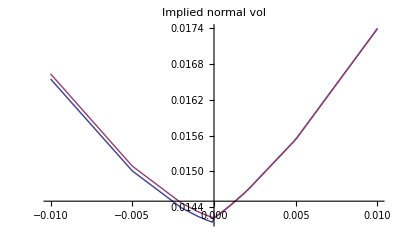
{58.282,-Graphics-}

```mathematica
Timing[Module[{S1=0.04,S2=0.04,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.8,ρsinf=0.8,ρm1=0.,ρm2=0.5,ρ1=-0.15,ρ2=-0.15, Σ1=0.04,Σ2=0.04,β=5,τ=5,λ1=1.1,λ2=1.2,strikes={-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.002,0.005,0.01},scope1,scope2,nb=40,inter,Lcoefs,vol1,vol2,ν1,ν2,printflag=0,Σinf,M,Σ},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
smile=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter=Interpolation[smile,InterpolationOrder->1];
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2,InterpolationOrder->1];
Plot[{inter[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston","biheston2"}]
]]
```

## Comparaison with a lognormal model and spike at the money

Le smile presente un coin a la monaie

β=9.

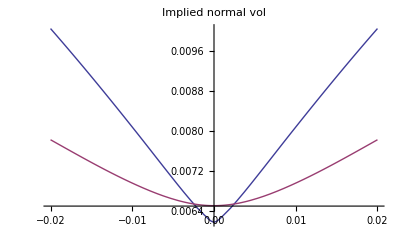
{80.172,-Graphics-}

```mathematica
Timing[Module[{ν1=0.1,ν2=0.1,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,integflag=0,
τ=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=60,flag=1,det,Lcoefs=LegendreCoeffs[40],vol1,vol2,spdopt,strikes,βmul=0.9},
strikes={-0.02,-0.015,-0.01,-0.0075,-0.005,-0.003,-0.001,0,0.001,0.003,0.005,0.0075,0.01,0.015,0.02};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];β*=βmul;
z1max=2;z2max=4;
smile1=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[{ν1,ρs1,χ1,Σinf1},{ν2,ρs2,χ2,Σinf2},{ρ1,ρ2},{ρ12,ρinf12}, {Σ1,Σ2},{S1,S2},β,strikes[[i]],τ,λ1,λ2,z1max,z2max,Nb,integflag,0]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile1];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,Σinf1,ρs1,χ1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,Σinf2,ρs2,χ2,ν2,Lcoefs];

smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρ12,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter1[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston","bilog"}]
]]
```

There is a discontinuity in the smile at the money that can be traced back a discontinuity of the derivative of the option price with respect to K

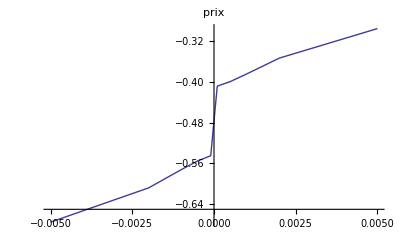
{76.109,-Graphics-}

```mathematica
Timing[Module[{S1=0.04,S2=0.04,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.8,ρsinf=0.8,ρm1=0.,ρm2=0.5,ρ1=-0.15,ρ2=-0.15, Σ1=0.04,Σ2=0.04,β=5,τ=5,λ1=1.1,λ2=1.2,strikes={-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.002,0.005,0.01},scope1,scope2,nb=40,inter,Lcoefs,vol1,vol2,ν1,ν2,printflag=0,Σinf,M,Σ},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
smile=Table[{strikes[[i]],NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]},{i,1,Length[strikes]}];
inter=Interpolation[smile,InterpolationOrder->1];
shift=0.0001;
smile2=Table[{strikes[[i]],(inter[strikes[[i]]+shift]-inter[strikes[[i]]-shift])/(2shift)},{i,2,Length[strikes]-1}];
inter2=Interpolation[smile2,InterpolationOrder->1];
Plot[{inter2[x]},{x,strikes[[2]],strikes[[Length[strikes]-1]]},PlotLabel->"prix",
PlotLegend->{"biheston","biheston2"}]
]]
```

## Smart Integration

```mathematica
Timing[Module[{S1=0.04,S2=0.04,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.8,ρsinf=0.8,ρm1=0.,ρm2=0.,ρ1=-0.15,ρ2=-0.15, Σ1=0.04,Σ2=0.04,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,nb=60,inter,Lcoefs,vol1,vol2,ν1,ν2,printflag=0,Σinf,M,Q,Σ,ρ,Y,zmax1,zmax2,K=0.001},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});ρ={ρ1,ρ2};
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;Y={Log[S1],Log[S2]};
scope1=4/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=6/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Plot3D[NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,ω2],{ω1,0,scope1},{ω2,0 ,scope2},PlotPoints->nb,PlotRange->All,PlotLabel->"K="<>ToString[K]]]]
```

{265.937,-Graphics3D-}

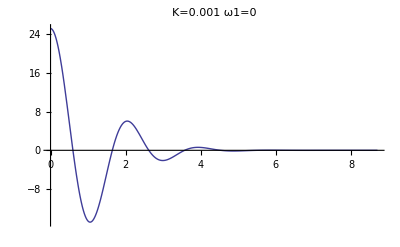
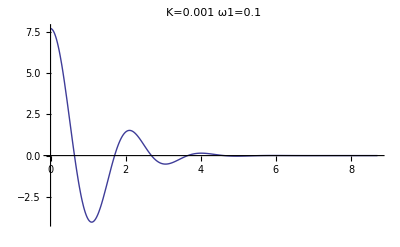
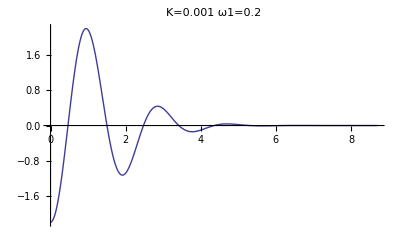
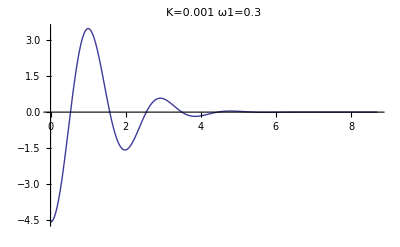
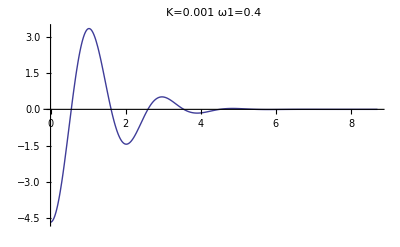
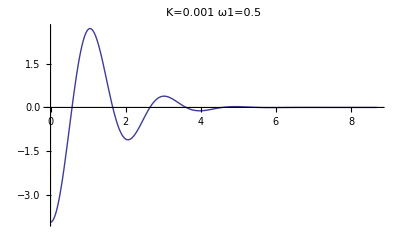
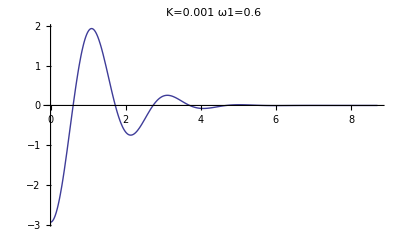
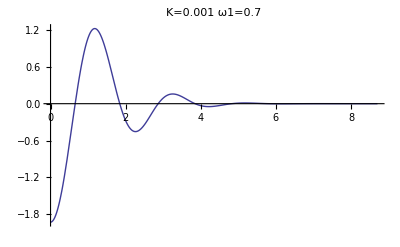
{186.765,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{S1=0.04,S2=0.04,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.8,ρsinf=0.8,ρm1=0.,ρm2=0.,ρ1=-0.15,ρ2=-0.15, Σ1=0.04,Σ2=0.04,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,nb=60,inter,Lcoefs,vol1,vol2,ν1,ν2,printflag=0,Σinf,M,Q,Σ,ρ,Y,zmax1,zmax2,K=0.001,ω1},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});ρ={ρ1,ρ2};
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;Y={Log[S1],Log[S2]};
scope1=4/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=6/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Table[Plot[NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,ω2],{ω2,0 ,scope2},PlotPoints->nb,PlotRange->All,PlotLabel->"K="<>ToString[K]<>" ω1="<>ToString[ω1]],{ω1,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,1,1.5,2}}]]]
```

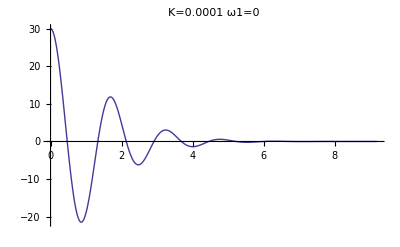
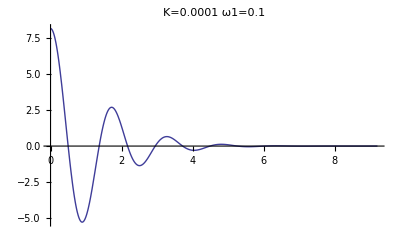
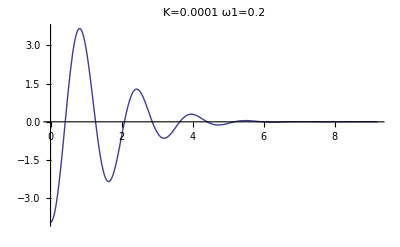
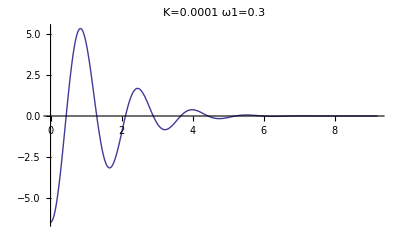
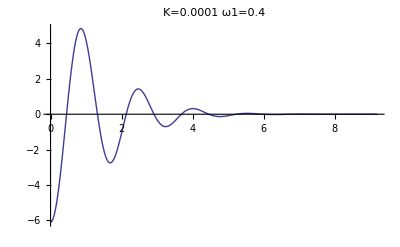
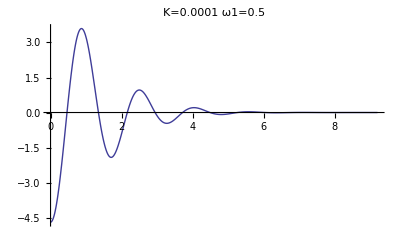
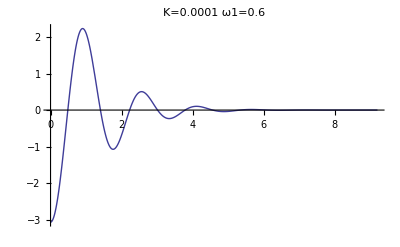
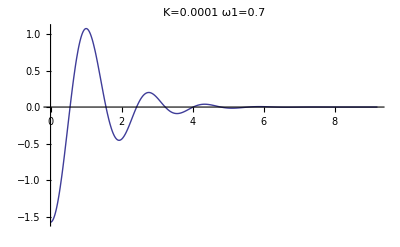
{203.032,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{S1=0.02,S2=0.02,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.3,ρsinf=0.3,ρm1=0.,ρm2=0.,ρ1=-0.15,ρ2=-0.15, Σ1=0.02,Σ2=0.02,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,nb=60,inter,Lcoefs,vol1,vol2,ν1,ν2,printflag=0,Σinf,M,Q,Σ,ρ,Y,zmax1,zmax2,K=0.0001,ω1},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});ρ={ρ1,ρ2};
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;Y={Log[S1],Log[S2]};
scope1=4/(√((Σ1+Σ2+θ1+θ2)/4τ));scope2=6/(√((Σ1+Σ2+θ1+θ2)/4τ));
Table[Plot[NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,ω2],{ω2,0 ,scope2},PlotPoints->nb,PlotRange->All,PlotLabel->"K="<>ToString[K]<>" ω1="<>ToString[ω1]],{ω1,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,1,1.5,2}}]]]
```

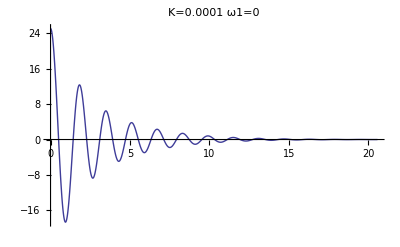
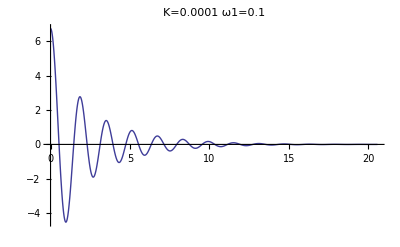
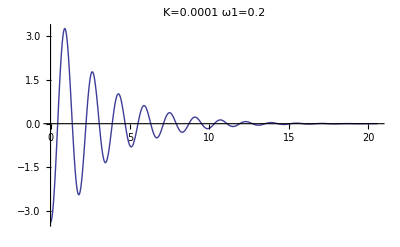
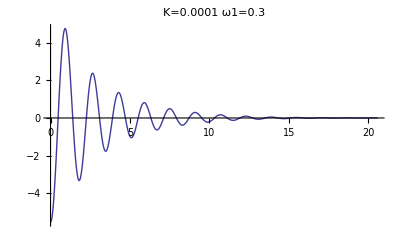
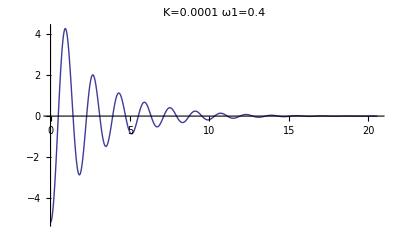
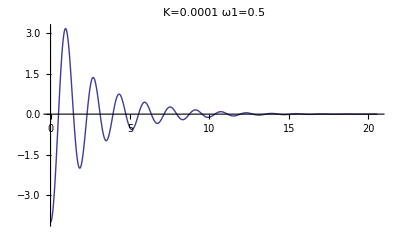
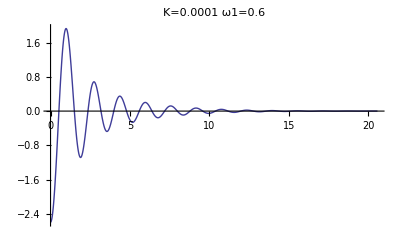
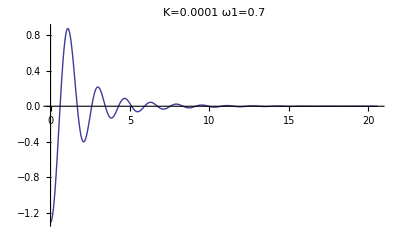
{284.703,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{S1=0.02,S2=0.02,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.3,ρsinf=0.3,ρm1=0.,ρm2=0.,ρ1=-0.15,ρ2=-0.15, Σ1=0.02,Σ2=0.02,β=10,τ=1,λ1=1.1,λ2=1.2,scope1,scope2,nb=60,inter,Lcoefs,vol1,vol2,ν1,ν2,printflag=0,Σinf,M,Q,Σ,ρ,Y,zmax1,zmax2,K=0.0001,ω1},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});ρ={ρ1,ρ2};
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;Y={Log[S1],Log[S2]};
scope1=4/(√((Σ1+Σ2+θ1+θ2)/4τ));scope2=6/(√((Σ1+Σ2+θ1+θ2)/4τ));
Table[Plot[NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,ω2],{ω2,0 ,scope2},PlotPoints->nb,PlotRange->All,PlotLabel->"K="<>ToString[K]<>" ω1="<>ToString[ω1]],{ω1,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,1,1.5,2}}]]]
```

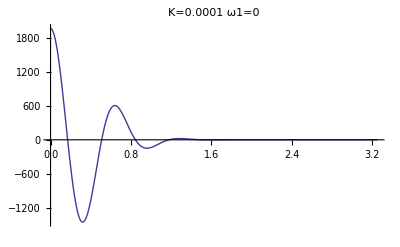
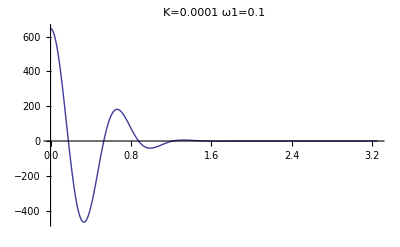
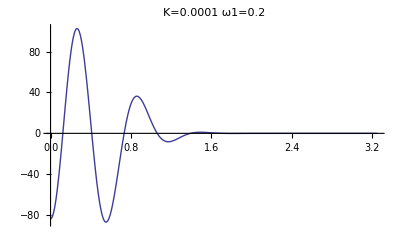
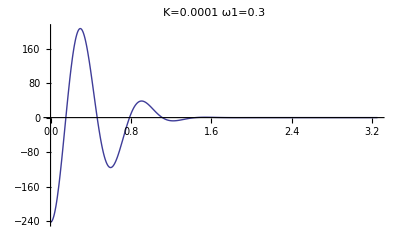
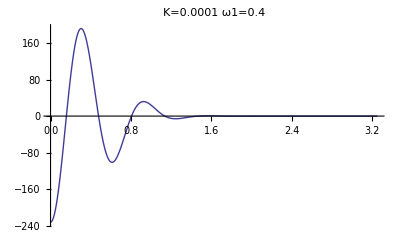
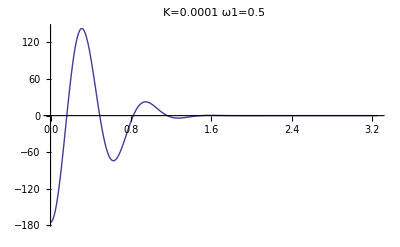
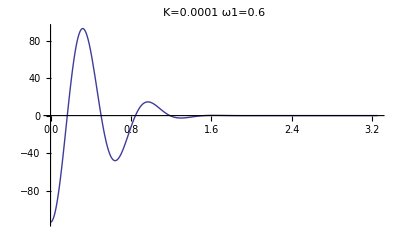
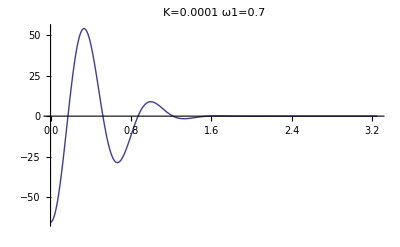
{212.141,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{S1=0.02,S2=0.02,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.3,ρsinf=0.3,ρm1=0.,ρm2=0.,ρ1=-0.15,ρ2=-0.15, Σ1=0.02,Σ2=0.02,β=10,τ=40,λ1=1.1,λ2=1.2,scope1,scope2,nb=60,inter,Lcoefs,vol1,vol2,ν1,ν2,printflag=0,Σinf,M,Q,Σ,ρ,Y,zmax1,zmax2,K=0.0001,ω1},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});ρ={ρ1,ρ2};
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;Y={Log[S1],Log[S2]};
scope1=4/(√((Σ1+Σ2+θ1+θ2)/4τ));scope2=6/(√((Σ1+Σ2+θ1+θ2)/4τ));
Table[Plot[NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,ω2],{ω2,0 ,scope2},PlotPoints->nb,PlotRange->All,PlotLabel->"K="<>ToString[K]<>" ω1="<>ToString[ω1]],{ω1,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,1,1.5,2}}]]]
```

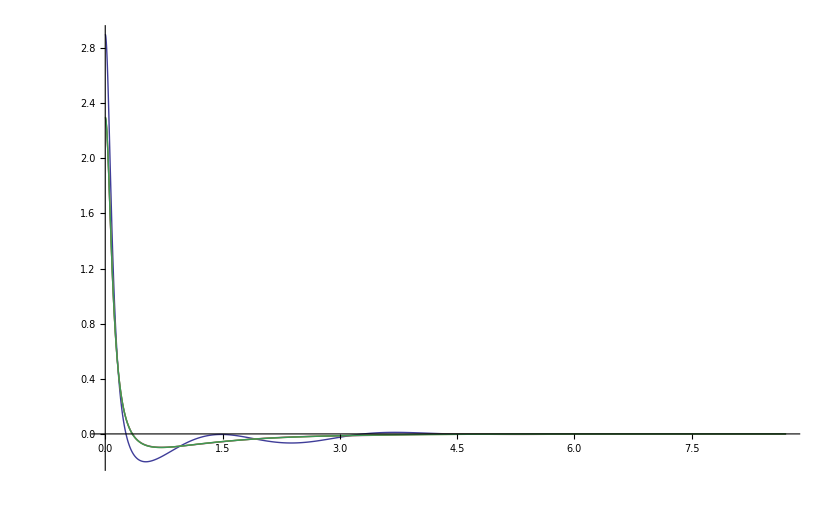
{1092.16,-Graphics-}

```mathematica
Timing[Module[{S1=0.04,S2=0.04,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.8,ρsinf=0.8,ρm1=0.,ρm2=0.,ρ1=-0.15,ρ2=-0.15, Σ1=0.04,Σ2=0.04,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,nb=60,inter,Lcoefs,vol1,vol2,ν1,ν2,printflag=0,Σinf,M,Q,Σ,ρ,Y,zmax1,zmax2,K=0.0001,ω1},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});ρ={ρ1,ρ2};
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;Y={Log[S1],Log[S2]};
scope1=4/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=6/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Plot[{CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,#])&,RiemanCoeffs[nb,0,scope2/3]],
CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,#])&,RiemanCoeffs[nb,0,scope2/1.5]],
CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,#])&,RiemanCoeffs[nb,0,scope2]],
CoeffBasedIntegrate[(NewSymetrizedSuperBiHestonVanillaReducedIntegrand2[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,#])&,RiemanCoeffs[nb,0,scope2*1.3]]},{ω1,0,scope2},PlotRange->All]]]
```

```mathematica
AdaptativeIntegrate[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_]:=Module[{sum=0.0,increment=ϵ+1,i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[Abs[increment]>ϵ,increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];i+=1;sum+=increment];{i,sum}]
```

```mathematica
AdaptativeIntegrate[Func_,LegendreCoef0_,period0_,periodn_,ϵ_]:=Module[{sum=0.0,increment=ϵ+1,i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[Abs[increment]>ϵ,increment=Func[period0+(i+1/2)*periodn]periodn;i+=1;sum+=increment];{i,sum}]
```

```mathematica
coefs=LegendreCoeffs[15];coefs2=LegendreCoeffs[5];
```

```mathematica
a=AdaptativeIntegrate[((1+Sin[#^2])Exp[-#] )&,coefs,coefs2,2,0.5,0.000001];{a,a[[2]]-NIntegrate[((1+Sin[x^2])Exp[-x] ),{x,0,∞}]}
```

{{23,1.27051},-1.32787×10^-6}

```mathematica
a=AdaptativeIntegrate[((1+Sin[#^2])Exp[-#] )&,coefs,4,0.01,0.0000001];{a,a[[2]]-NIntegrate[((1+Sin[x^2])Exp[-x] ),{x,0,∞}]}
```

{{16,1.25513},-0.0153883}

```mathematica
AdaptativeIntegrate[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_]:=Module[{sum=0.0,increment=ϵ+1,i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[Abs[increment]>ϵ,increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];i+=1;sum+=increment];{i,sum}]
```

```mathematica
AdaptativeIntegrate[Func_,LegendreCoef0_,period0_,periodn_,ϵ_]:=Module[{sum=0.0,increment=ϵ+1,i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[Abs[increment]>ϵ,increment=Func[period0+(i+1/2)*periodn]periodn;i+=1;sum+=increment];{i,sum}]
```

```mathematica
NewSuperBiHestonVanilla[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=NewSuperBiHestonVanillaAux[K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag] /; K≥0
```

```mathematica
NewSuperBiHestonVanilla[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=NewSuperBiHestonVanillaAux[K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]-K/; K<0
```

```mathematica
NewSuperBiHestonVanillaAux[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},Q},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
If[printflag==1,Print["{K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2}=",{K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2}]];
If[printflag==2,Print["{NbLegendreCoef1,NbLegendreCoef1n,period1,period1n,ϵ1}=",{Length[LegendreCoef1],Length[LegendreCoef1n],period1,period1n,ϵ1}]];
If[printflag==2,Print["{NbLegendreCoef2,period2,period2n,ϵ2}=",{Length[LegendreCoef2],period2,period2n,ϵ2}]];
If[printflag==1,Print["{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1}=",{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1}," {LegendreCoef2,period2,period2n,ϵ2}=",{LegendreCoef2,period2,period2n,ϵ2}]];
res=AdaptativeIntegrate[Function[ω2,a=AdaptativeIntegrate[Function[ω1,NewSymetrizedSuperBiHestonVanillaReducedIntegrand[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1];If[printflag==2,Print["Integ_2=",a]];a[[2]]],LegendreCoef2,period2,period2n,ϵ2];
If[printflag==2,Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
Timing[Module[{S1=0.05,S2=0.05,K=0.00001,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=0,M,Σinf,Σ},scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=12;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=8;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.00001;
Nb2=10;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/10;ϵ2=0.00001;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
{NewSuperBiHestonVanilla[K,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag],
NewSuperBiHestonVanilla[0,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag],
NewSuperBiHestonVanilla[-K,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]}]]
```

{6.437,{0.00877397,0.00877929,0.0087846}}

## Correlation smile effect

The purpose of the whole framework is be able to model correlation smile effect that is visualized here through the rotation effect of the smile due to croos term inside the mean reverting matrix M

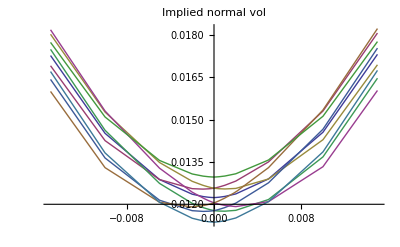
{2948.37,-Graphics-}

```mathematica
Timing[Module[{S1=0.04,S2=0.04,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.8,ρsinf=0.8,ρm1=0.,ρm2=0.,ρ1=-0.15,ρ2=-0.15, Σ1=0.04,Σ2=0.04,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,nb=100,inter,Lcoefs,vol1,vol2,ν1,ν2,printflag=0,Σinf,M,Σ},
strikes={-0.03,-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.01,0.02,0.03};
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
scope1=4/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=6/(√((Σ1+Σ2+θ1+θ2)/4 τ));
ρm1=0.;ρm2=0.;M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile00=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter00=Interpolation[smile00,InterpolationOrder->1];
ρm1=0.5;ρm2=0.;M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile10=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter10=Interpolation[smile10,InterpolationOrder->1];
ρm1=0.;ρm2=0.5;M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile01=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter01=Interpolation[smile01,InterpolationOrder->1];
ρm1=-0.5;ρm2=0.;M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile50=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter50=Interpolation[smile50,InterpolationOrder->1];
ρm1=0.;ρm2=-0.5;M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile05=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter05=Interpolation[smile05,InterpolationOrder->1];
ρm1=0.5;ρm2=0.5;M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile11=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter11=Interpolation[smile11,InterpolationOrder->1];
ρm1=-0.5;ρm2=-0.5;M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile55=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter55=Interpolation[smile55,InterpolationOrder->1];
ρm1=-0.5;ρm2=0.5;M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile51=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter51=Interpolation[smile51,InterpolationOrder->1];
ρm1=0.5;ρm2=-0.5;M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile15=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter15=Interpolation[smile15,InterpolationOrder->1];
Lcoefs=LegendreCoeffs[40];
ν1=0.2;vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρ1,M1,ν1,Lcoefs];
ν2=0.2;vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρ2,M2,ν2,Lcoefs];
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρs,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2,InterpolationOrder->1];
Plot[{inter00[x],inter01[x],inter10[x],inter05[x],inter50[x],inter15[x],inter51[x],inter11[x],inter55[x]},{x,strikes[[1]]/2,Last[strikes]/2},PlotLabel->"Implied normal vol",
PlotLegend->{"00","01","10","05","50","15","51","11","55"},LegendPosition->{1,0}]
]]
```

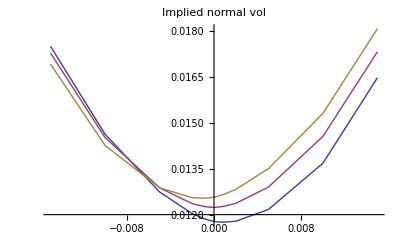

```mathematica
Plot[{inter05[x],inter00[x],inter01[x]},{x,strikes[[1]]/2,Last[strikes]/2},PlotLabel->"Implied normal vol",
PlotLegend->{"05","00","01"},LegendPosition->{1,0}]
```

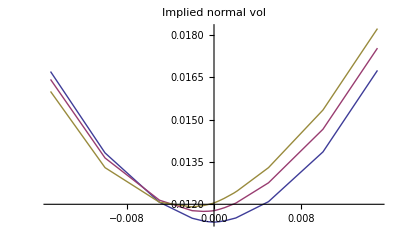

```mathematica
Plot[{inter55[x],inter50[x],inter51[x]},{x,strikes[[1]]/2,Last[strikes]/2},PlotLabel->"Implied normal vol",
PlotLegend->{"55","50","51"},LegendPosition->{1,0}]
```

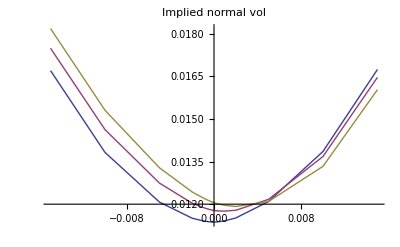

```mathematica
Plot[{inter55[x],inter05[x],inter15[x]},{x,strikes[[1]]/2,Last[strikes]/2},PlotLabel->"Implied normal vol",
PlotLegend->{"55","05","15"},LegendPosition->{1,0}]
```

```mathematica
AjustOrder[n_]:=Module[{},
inter15=Interpolation[smile15,InterpolationOrder->n];
inter51=Interpolation[smile51,InterpolationOrder->n];
inter55=Interpolation[smile55,InterpolationOrder->n];
inter11=Interpolation[smile11,InterpolationOrder->n];
inter05=Interpolation[smile05,InterpolationOrder->n];
inter50=Interpolation[smile50,InterpolationOrder->n];
inter10=Interpolation[smile10,InterpolationOrder->n];
inter00=Interpolation[smile00,InterpolationOrder->n];
inter01=Interpolation[smile01,InterpolationOrder->n];
]
```

L' ordre de l' interpolation ne change rien car le smile presente reelement un coin

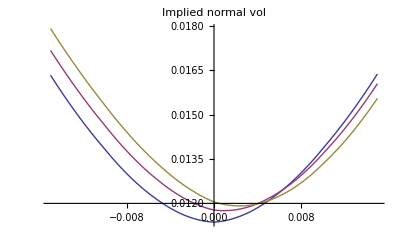

```mathematica
AjustOrder[2];Plot[{inter55[x],inter05[x],inter15[x]},{x,strikes[[1]]/2,Last[strikes]/2},PlotLabel->"Implied normal vol",
PlotLegend->{"55","05","15"},LegendPosition->{1,0}]
```

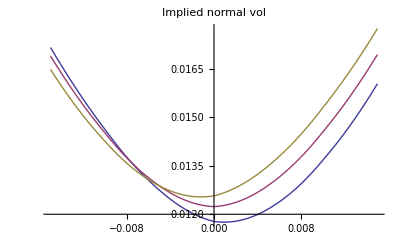

```mathematica
Plot[{inter05[x],inter00[x],inter01[x]},{x,strikes[[1]]/2,Last[strikes]/2},PlotLabel->"Implied normal vol",
PlotLegend->{"05","00","01"},LegendPosition->{1,0}]
```

## Influence of the stochastic correlation

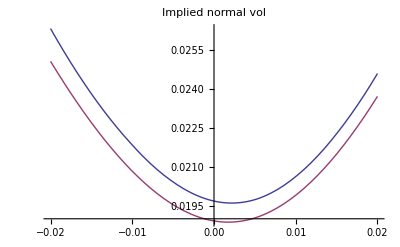
{19.905,-Graphics-}

```mathematica
Timing[Module[{S1=0.05,S2=0.05,K=0.00001,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,ν1=0.01,ν2=0.01,Lcoefs=LegendreCoeffs[40],
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=0,M,Σinf,Σ},scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=12;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=8;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.00001;
Nb2=10;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/10;ϵ2=0.00001;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
strikes={-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02};
smile000=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter000=Interpolation[smile000,InterpolationOrder->2];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρ1,-M1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρ2,-M2,ν2,Lcoefs];ρsmod=ρs;
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρsmod,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter000[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston","bilog"}]
]]
```

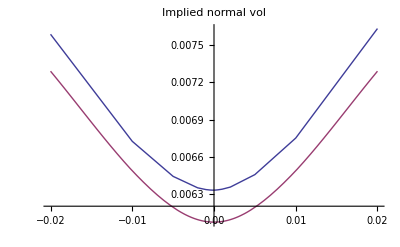
{214.938,-Graphics-}

```mathematica
Timing[Module[{S1=0.04,S2=0.04,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.8,ρsinf=0.8,ρm1=0.,ρm2=0.,ρ1=-0.15,ρ2=-0.15, Σ1=0.04,Σ2=0.04,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,nb=60,inter,Lcoefs=LegendreCoeffs[40],vol1,vol2,ν1=0.01,ν2=0.01,printflag=0,Σinf,M,Σ},
strikes={-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.01,0.02};
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
scope1=5/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=8/(√((Σ1+Σ2+θ1+θ2)/4 τ));
ρm1=0.;ρm2=0.;M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile000=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter000=Interpolation[smile000,InterpolationOrder->1];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρ1,-M1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρ2,-M2,ν2,Lcoefs];ρsmod=ρs;
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρsmod,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter000[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston","bilog"}]
]]
```

```mathematica
smile000
```

{{-0.02,0.00719348},{-0.01,0.00655477},{-0.005,0.00630812},{-0.002,0.00621388},{-0.001,0.00619576},{-0.0005,0.0061896},{-0.0002,0.00618687},{-0.0001,0.00618613},{0,0.00618547},{0.0001,0.00618639},{0.0002,0.00618739},{0.0005,0.00619087},{0.001,0.00619828},{0.002,0.00621879},{0.005,0.00631958},{0.01,0.00657606},{0.02,0.00723526}}

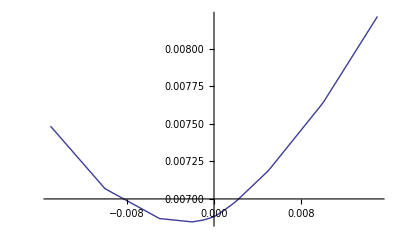
{118.609,-Graphics-}

```mathematica
Timing[Module[{S1=0.04,S2=0.04,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.8,ρsinf=0.8,ρm1=0.,ρm2=0.5,ρ1=-0.15,ρ2=-0.15, Σ1=0.04,Σ2=0.04,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,nb=40,inter,Lcoefs,vol1,vol2,ν1,ν2,printflag=0,Σinf,M,Σ},
strikes={-0.03,-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.01,0.02,0.03};
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
scope1=4/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=6/(√((Σ1+Σ2+θ1+θ2)/4 τ));
smile000=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter000=Interpolation[smile000,InterpolationOrder->1];
Plot[inter000[x],{x,strikes[[1]]/2,Last[strikes]/2}]
]]
```

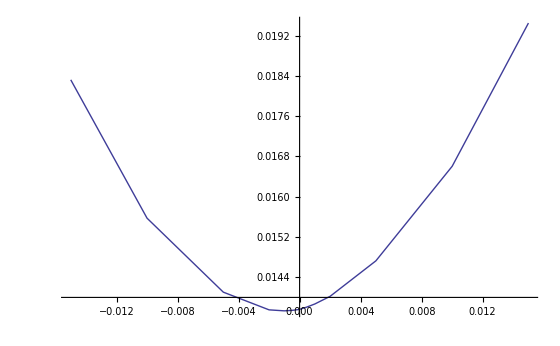
{57.596,-Graphics-}

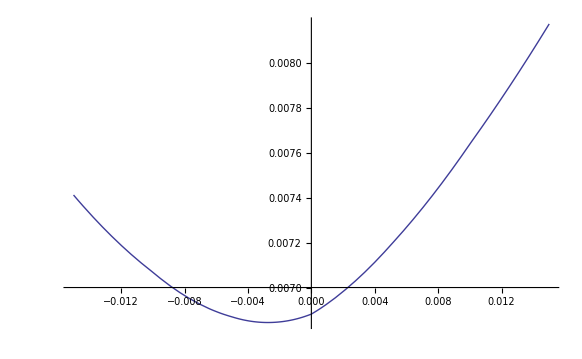
{109.11,-Graphics-}

```mathematica
Timing[Module[{S1=0.04,S2=0.04,M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.8,ρsinf=0.8,ρm1=0.,ρm2=0.5,ρ1=-0.15,ρ2=-0.15, Σ1=0.04,Σ2=0.04,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,nb=40,inter,Lcoefs,vol1,vol2,ν1,ν2,printflag=0,Σinf,M,Σ},
strikes={-0.03,-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.01,0.02,0.03};
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
scope1=4/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=6/(√((Σ1+Σ2+θ1+θ2)/4 τ));
smile000=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla2[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,nb,printflag]]},{i,1,Length[strikes]}];
inter000=Interpolation[smile000,InterpolationOrder->1];
Plot[inter000[x],{x,strikes[[1]]/2,Last[strikes]/2}]
]]
```

β=9.

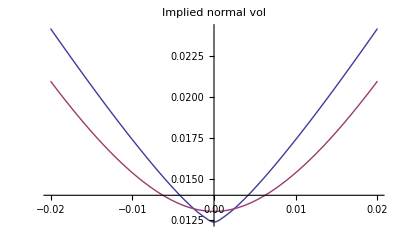
{44.07,-Graphics-}

```mathematica
Timing[Module[{ν1=0.1,ν2=0.1,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,integflag=0,
τ=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=60,flag=1,det,Lcoefs=LegendreCoeffs[40],vol1,vol2,spdopt,strikes,βmul=0.9},
strikes={-0.02,-0.015,-0.01,-0.0075,-0.005,-0.003,-0.001,0,0.001,0.003,0.005,0.0075,0.01,0.015,0.02};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];β*=βmul;
z1max=2;z2max=4;
smile1=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[{ν1,ρs1,χ1,Σinf1},{ν2,ρs2,χ2,Σinf2},{ρ1,ρ2},{ρ12,ρinf12}, {Σ1,Σ2},{S1,S2},β,strikes[[i]],τ,λ1,λ2,z1max,z2max,Nb,integflag,0]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile1];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,Σinf1,ρs1,χ1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,Σinf2,ρs2,χ2,ν2,Lcoefs];

smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρ12,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter1[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston","bilog"}]
]]
```

β=9.

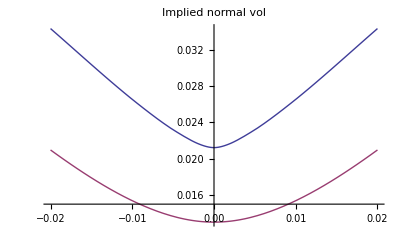
{96.19,-Graphics-}

```mathematica
Timing[Module[{ν1=0.1,ν2=0.1,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,integflag=0,
τ=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=80,flag=1,det,Lcoefs=LegendreCoeffs[40],vol1,vol2,spdopt,strikes,βmul=0.9},
strikes={-0.02,-0.01,-0.0075,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.02};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];β*=βmul;
z1max=8;z2max=12;
smile1=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[{ν1,ρs1,χ1,Σinf1},{ν2,ρs2,χ2,Σinf2},{ρ1,ρ2},{ρ12,ρinf12}, {Σ1,Σ2},{S1,S2},β,strikes[[i]],τ,λ1,λ2,z1max,z2max,Nb,integflag,0]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile1];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,Σinf1,ρs1,χ1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,Σinf2,ρs2,χ2,ν2,Lcoefs];

smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρ12,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter1[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston","bilog"}]
]]
```

β=10.8

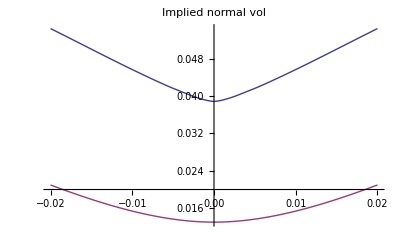
{149.262,-Graphics-}

```mathematica
Timing[Module[{ν1=0.1,ν2=0.1,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,integflag=0,
τ=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=100,flag=1,det,Lcoefs=LegendreCoeffs[40],vol1,vol2,spdopt,strikes,βmul=0.9},
strikes={-0.02,-0.01,-0.0075,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.02};
β=1.2 βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];β*=βmul;
z1max=15;z2max=20;
smile1=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[{ν1,ρs1,χ1,Σinf1},{ν2,ρs2,χ2,Σinf2},{ρ1,ρ2},{ρ12,ρinf12}, {Σ1,Σ2},{S1,S2},β,strikes[[i]],τ,λ1,λ2,z1max,z2max,Nb,integflag,0]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile1];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,Σinf1,ρs1,χ1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,Σinf2,ρs2,χ2,ν2,Lcoefs];

smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρ12,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter1[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston","bilog"}]
]]
```

## Option Vanille Partielle (S_1-K)^+

x2>0

```mathematica
integration1=Simplify[∫_Log[K]^∞ ⅇ^(ⅈ k1 x1)(ⅇ^x1-K)ⅆx1]
```

If[Im[k1]>1,-K^(1+ⅈ k1)/(k1 (-ⅈ+k1)),Integrate[ⅇ^(x1+ⅈ k1 x1)-ⅇ^(ⅈ k1 x1) K,{x1,Log[K],∞},Assumptions→Im[k1]≤1]]

```mathematica
integration11=Simplify[integration1,Im[k1]>1]
```

-K^(1+ⅈ k1)/(k1 (-ⅈ+k1))

```mathematica
integration12=Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration11,{x2,0,∞}],K>0]
```

-(K^(1+ⅈ k1) If[Im[k2]>0,ⅈ/k2,Integrate[ⅇ^(ⅈ k2 x2),{x2,0,∞},Assumptions→Im[k2]≤0]])/(k1 (-ⅈ+k1))

```mathematica
Simplify[integration12,Im[k2]>0]
```

(ⅈ K^(1+ⅈ k1))/(ⅈ k1 k2-k1^2 k2)

x2<0

```mathematica
integration1=Simplify[∫_Log[K]^∞ ⅇ^(ⅈ k1 x1)(ⅇ^x1-K)ⅆx1]
```

If[Im[k1]>1,-K^(1+ⅈ k1)/(k1 (-ⅈ+k1)),Integrate[ⅇ^(x1+ⅈ k1 x1)-ⅇ^(ⅈ k1 x1) K,{x1,Log[K],∞},Assumptions→Im[k1]≤1]]

```mathematica
integration11=Simplify[integration1,Im[k1]>1]
```

-K^(1+ⅈ k1)/(k1 (-ⅈ+k1))

```mathematica
integration12=Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration11,{x2,-∞,0}],K>0]
```

-(K^(1+ⅈ k1) If[Im[k2]<0,-ⅈ/k2,Integrate[ⅇ^(-ⅈ k2 x2),{x2,0,∞},Assumptions→Im[k2]≥0]])/(k1 (-ⅈ+k1))

```mathematica
Simplify[integration12,Im[k2]<0]
```

-K^(1+ⅈ k1)/(k1 k2+ⅈ k1^2 k2)

```mathematica
FirstUnderlyingPayOff[x1_,x2_,K_]:=Max[ⅇ^x1-K,0]
```

```mathematica
FirstUnderlyingVanillaFourierPayOffDroite[k1_,k2_,K_]:=(ⅈ K^(1+ⅈ k1))/(ⅈ k1 k2-k1^2 k2)
```

```mathematica
FirstUnderlyingVanillaFourierPayOffGauche[k1_,k2_,K_]:=-K^(1+ⅈ k1)/(k1 k2+ⅈ k1^2 k2)
```

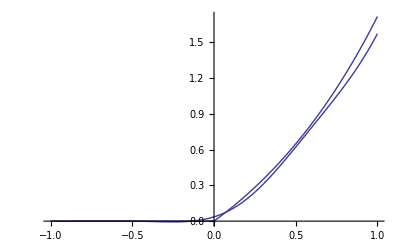
{37.532,-Graphics-}

```mathematica
Timing[Module[{x2=0.1,K=1,λ1=2,λ2=1.2,coeff=RiemanCoeffs[40,-8,8]},g1=ListPlot[Table[{i/100,Re[Module[{x1=i/100},1/(2π)^2 CoeffBasedIntegrate[(ⅇ^(-ⅈ x1( #1+ⅈ λ1)-ⅈ x2( #2-ⅈ λ2))FirstUnderlyingVanillaFourierPayOffGauche[#1+ⅈ λ1,( #2-ⅈ λ2),K]+ⅇ^(-ⅈ x1( #1+ⅈ λ1)-ⅈ x2( #2+ⅈ λ2))FirstUnderlyingVanillaFourierPayOffDroite[#1+ⅈ λ1,( #2+ⅈ λ2),K])&,coeff,coeff]]]},{i,-100,100}],Joined->True];
g2=ListPlot[Table[{i/100,Module[{x1=i/100},Re[FirstUnderlyingPayOff[x1,x2,K]]]},{i,-100,100}],Joined->True];
Show[g1,g2,PlotRange->All]]]
```

```mathematica
SymetrizedSuperBiHestonUnderlying1VanillaIntegrand[K_,τ_,M_,Q_,ρ_,Σ_,Y_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
α propagatorDroit FirstUnderlyingVanillaFourierPayOffDroite[k1,k2,K]+
Symα SympropagatorDroit FirstUnderlyingVanillaFourierPayOffDroite[Sk1,k2,K]+
αA propagatorGauche FirstUnderlyingVanillaFourierPayOffGauche[k1,k2A,K]+
SymαA SympropagatorGauche FirstUnderlyingVanillaFourierPayOffGauche[Sk1A,k2A,K]]]
```

```mathematica
NewSuperBiHestonUnderlying1Vanilla[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=NewSuperBiHestonUnderlying1VanillaAux[K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag] /; K≥0
```

```mathematica
NewSuperBiHestonUnderlying1Vanilla[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=NewSuperBiHestonUnderlying1VanillaAux[K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]-K/; K<0
```

```mathematica
NewSuperBiHestonUnderlying1VanillaAux[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},Q},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
If[printflag==1,Print["{K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2}=",{K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2}]];
If[printflag==2,Print["{NbLegendreCoef1,NbLegendreCoef1n,period1,period1n,ϵ1}=",{Length[LegendreCoef1],Length[LegendreCoef1n],period1,period1n,ϵ1}]];
If[printflag==2,Print["{NbLegendreCoef2,period2,period2n,ϵ2}=",{Length[LegendreCoef2],period2,period2n,ϵ2}]];
If[printflag==1,Print["{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1}=",{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1}," {LegendreCoef2,period2,period2n,ϵ2}=",{LegendreCoef2,period2,period2n,ϵ2}]];
res=AdaptativeIntegrate[Function[ω2,a=AdaptativeIntegrate[Function[ω1,SymetrizedSuperBiHestonUnderlying1VanillaIntegrand[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1];If[printflag==2,Print["Integ_2=",a]];a[[2]]],LegendreCoef2,period2,period2n,ϵ2];
If[printflag==2,Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
Module[{S1=0.05,S2=0.05,K=0.05,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=0,M,Σinf,Σ},scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=12;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=8;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.00001;
Nb2=10;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/10;ϵ2=0.00001;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
Timing[NewSuperBiHestonUnderlying1Vanilla[K,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]]
```

{1.156,0.00918266}

InterpolatingFunction::dmval: Input value {0.0200016} lies outside the range of data in the interpolating function. Extrapolation will be used.

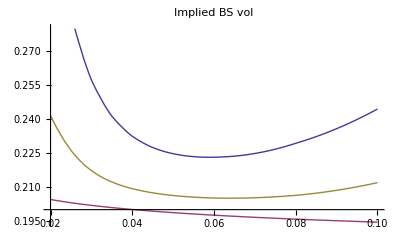
{66.955,-Graphics-}

```mathematica
Off[InterpolatingFunction::"dmval"];
Timing[Module[{S1=0.05,S2=0.05,K=0.00001,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.,ρm2=0.,ρ1=-0.5,ρ2=-0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,ν1=0.01,ν2=0.01,Lcoefs=LegendreCoeffs[40],
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=0,M,Σinf,Σ},scope1=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=4/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=12;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=8;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.00001;
Nb1F=35;LegendreCoef1F=LegendreCoeffs[Nb1F];Nb1nF=12;LegendreCoef1nF=LegendreCoeffs[Nb1nF];
Nb2=20;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/10;ϵ2=0.00001;
Nb2F=20;LegendreCoef2F=LegendreCoeffs[Nb2F];
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
strikes={0.02,0.025,0.03,0.035,0.04,0.045,0.048,0.049,0.0499,0.05,0.0501,0.0505,0.055,0.06,0.08,0.1};
smile000=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,NewSuperBiHestonUnderlying1Vanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter000=Interpolation[smile000,InterpolationOrder->2];
smile2=Table[{strikes[[i]],ImpVolHeston2[S1,strikes[[i]],τ,Σ1,θ1,ρ1,-M1,ν1,Lcoefs]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
smile3=Table[{strikes[[i]]+0.0001,ImpVolBS[S1,strikes[[i]]+0.0001,τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,0.0001},β,λ1,λ2,
{LegendreCoef1F,LegendreCoef1nF,period1,period1n/2,ϵ1},{LegendreCoef2F,period2,period2n/4,ϵ2},printflag]]},{i,1,Length[strikes]}];

inter3=Interpolation[smile3];
Plot[{inter000[x],inter2[x],inter3[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol",
PlotLegend->{"BiHestonUnderlying1","Heston","Bihestonlimit"},LegendPosition->{1,0}]
]]
```

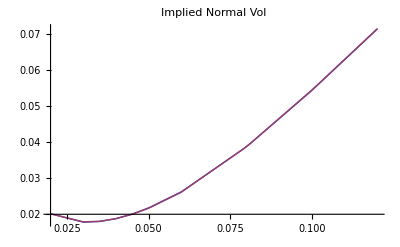
{53.586,-Graphics-}

```mathematica
Timing[Module[{M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.,ρsinf=0.,ρm1=0.,ρm2=0.,ρ1=-0.5,ρ2=-0.5, Σ1=0.04,Σ2=0.04,β=2.25,τ=5,λ1=1.1,λ2=1.1,ν1,S={0.04,0.0001},Q,strikes={0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.08,0.1,0.12},scope1,scope2,nb=70,inter,inter2,integflag=0,coeffs=LegendreCoeffs[40],M,Σinf,Σ},
scope1=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=5/(√((Σ1+Σ2+θ1+θ2)/4 τ));
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
smile=Table[{strikes[[i]],NormalImplicitVol[S[[1]]-S[[2]],strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,S,β,λ1,λ2,scope1,scope2,nb,0]]},{i,1,Length[strikes]}];
inter=Interpolation[smile,InterpolationOrder->1];
 Q=√(-M1 θ1)/β;
smile2=Table[{strikes[[i]],NormalImplicitVol[S[[1]]-S[[2]],strikes[[i]],τ,HestonCall2[S[[1]],strikes[[i]]+S[[2]],τ,Σ1,θ1,ρ1,-M1,Q,coeffs]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2,InterpolationOrder->1];
Plot[{inter[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied Normal Vol",PlotLegend->{"BiHeston","Heston"}, LegendPosition->{1,0}, LegendSize->0.5]
]]
```

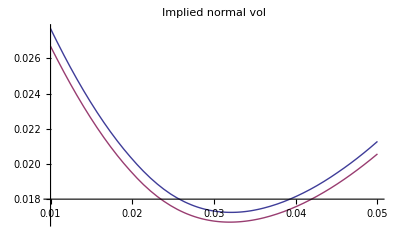
{22.588,-Graphics-}

```mathematica
Timing[Module[{S1=0.05,S2=0.01,K=0.00001,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,ν1=0.01,ν2=0.01,Lcoefs=LegendreCoeffs[40],
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=0,M,Σinf,Σ},scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=12;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=8;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.00001;
Nb2=10;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/10;ϵ2=0.00001;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
strikes={-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02}+0.03;
smile000=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter000=Interpolation[smile000,InterpolationOrder->2];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρ1,-M1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρ2,-M2,ν2,Lcoefs];ρsmod=ρs;
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρsmod,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter000[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston","bilog"}]
]]
```

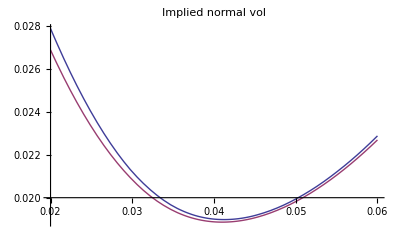
{100.745,-Graphics-}

```mathematica
Timing[Module[{S1=0.05,S2=0.0001,K=0.00001,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,ν1=0.01,ν2=0.01,Lcoefs=LegendreCoeffs[40],
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=0,M,Σinf,Σ},scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=35;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=15;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.000001;
Nb2=16;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/20;ϵ2=0.000001;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
strikes={-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02}+0.04;
smile000=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter000=Interpolation[smile000,InterpolationOrder->2];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρ1,-M1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρ2,-M2,ν2,Lcoefs];ρsmod=ρs;
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρsmod,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter000[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston","bilog"}]
]]
```

## Option Vanille Partielle (S_2-K)^+

```mathematica
SecondUnderlyingVanillaFourierPayOffDroite[k1_,k2_,K_]:=(ⅈ K^(1+ⅈ k2))/(ⅈ k1 k2-k2^2 k1)
```

```mathematica
SecondUnderlyingVanillaFourierPayOffGauche[k1_,k2_,K_]:=-K^(1+ⅈ k2)/(k1 k2+ⅈ k2^2 k1)
```

```mathematica
SecondUnderlyingPayOff[x1_,x2_,K_]:=Max[ⅇ^x2-K,0]
```

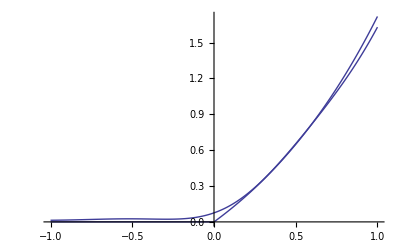
{13.229,-Graphics-}

```mathematica
Timing[Module[{x1=0.1,K=1,λ1=2,λ2=1.2,coeff=RiemanCoeffs[40,-8,8]},g1=ListPlot[Table[{i/100,Re[Module[{x2=i/100},1/(2π)^2 CoeffBasedIntegrate[(ⅇ^(-ⅈ x1( #1-ⅈ λ1)-ⅈ x2( #2+ⅈ λ2))SecondUnderlyingVanillaFourierPayOffGauche[#1-ⅈ λ1,( #2+ⅈ λ2),K]+ⅇ^(-ⅈ x1( #1+ⅈ λ1)-ⅈ x2( #2+ⅈ λ2))SecondUnderlyingVanillaFourierPayOffDroite[#1+ⅈ λ1,( #2+ⅈ λ2),K])&,coeff,coeff]]]},{i,-100,100}],Joined->True];
g2=ListPlot[Table[{i/100,Module[{x2=i/100},Re[SecondUnderlyingPayOff[x1,x2,K]]]},{i,-100,100}],Joined->True];
Show[g1,g2,PlotRange->All]]]
```

```mathematica
SymetrizedSuperBiHestonUnderlying2VanillaIntegrand[K_,τ_,M_,Q_,ρ_,Σ_,Y_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk1A=(-ω1-ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2+ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1A-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ k1A,-ⅈ k2A},β,τ];SympropagatorGauche=SuperBiHestonLaplaceTransformReduced[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
α propagatorDroit SecondUnderlyingVanillaFourierPayOffDroite[k1,k2,K]+
Symα SympropagatorDroit SecondUnderlyingVanillaFourierPayOffDroite[Sk1,k2,K]+
αA propagatorGauche SecondUnderlyingVanillaFourierPayOffGauche[k1A,k2A,K]+
SymαA SympropagatorGauche SecondUnderlyingVanillaFourierPayOffGauche[Sk1A,k2A,K]]]
```

```mathematica
NewSuperBiHestonUnderlying2Vanilla[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=NewSuperBiHestonUnderlying2VanillaAux[K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag] /; K≥0
```

```mathematica
NewSuperBiHestonUnderlying2Vanilla[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=NewSuperBiHestonUnderlying2VanillaAux[K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]-K/; K<0
```

```mathematica
NewSuperBiHestonUnderlying2VanillaAux[K_,τ_,M_,Σinf_,ρ_,Σ_,S_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},Q},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
If[printflag==1,Print["{K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2}=",{K,τ,M,Σinf,ρ,Σ,S,β,λ1,λ2}]];
If[printflag==2,Print["{NbLegendreCoef1,NbLegendreCoef1n,period1,period1n,ϵ1}=",{Length[LegendreCoef1],Length[LegendreCoef1n],period1,period1n,ϵ1}]];
If[printflag==2,Print["{NbLegendreCoef2,period2,period2n,ϵ2}=",{Length[LegendreCoef2],period2,period2n,ϵ2}]];
If[printflag==1,Print["{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1}=",{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1}," {LegendreCoef2,period2,period2n,ϵ2}=",{LegendreCoef2,period2,period2n,ϵ2}]];
res=AdaptativeIntegrate[Function[ω2,a=AdaptativeIntegrate[Function[ω1,SymetrizedSuperBiHestonUnderlying2VanillaIntegrand[K,τ,M,Q,ρ,Σ,Y,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1];If[printflag==2,Print["Integ_2=",a]];a[[2]]],LegendreCoef2,period2,period2n,ϵ2];
If[printflag==2,Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
Module[{S1=0.05,S2=0.05,K=0.05,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=0,M,Σinf,Σ},scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=12;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=8;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.00001;
Nb2=10;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/10;ϵ2=0.00001;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
Timing[NewSuperBiHestonUnderlying2Vanilla[K,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]]
```

{0.312,0.0104251}

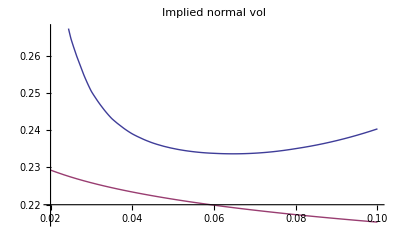
{8.627,-Graphics-}

```mathematica
Timing[Module[{S1=0.05,S2=0.05,K=0.00001,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=-0.5,ρ2=-0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,ν1=0.01,ν2=0.01,Lcoefs=LegendreCoeffs[40],
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=0,M,Σinf,Σ},scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=12;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=8;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.00001;
Nb2=10;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/10;ϵ2=0.00001;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
strikes={0.02,0.025,0.03,0.035,0.04,0.045,0.048,0.049,0.0499,0.05,0.0501,0.0505,0.055,0.06,0.08,0.1};
smile000=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,NewSuperBiHestonUnderlying2Vanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter000=Interpolation[smile000,InterpolationOrder->2];
smile2=Table[{strikes[[i]],ImpVolHeston2[S2,strikes[[i]],τ,Σ2,θ2,ρ2,-M2,ν2,Lcoefs]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter000[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"BiHeston","Heston"},LegendPosition->{1,0}]
]]
```

## Link with Heston formula

```mathematica
LNHestonRiccatiVanillaCallIntegrand[F_,K_,z_,V_,τ_,θ_,λ_,ν_,ρ_]:=
Module[{ψp,ψm,ζ,X},
Re[ⅇ^(-Log[F] I z)HestonLaplaceTransform4[-λ,θ,ρ, V,-ⅈ z,ν,τ]FourierPayOffLNSepp[z,K]]]
```

```mathematica
LNHestonRiccatiVanillaCall[F_,K_,V0_,τ_,λ_,θ_,ν_,ρ_,limsup_]:=
F+1/Pi NIntegrate[
LNHestonRiccatiVanillaCallIntegrand[F,K,k1+I/2,V0,τ,θ,λ,ν,ρ],{k1,0,limsup},MaxRecursion->20]
```

```mathematica
Timing[Module[{M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.,ρsinf=0.,ρm1=0.,ρm2=0.,ρ1=-0.5,ρ2=-0.5, Σ1=0.04,Σ2=0.04,β=2.25,τ=5,λ1=1.1,λ2=1.1,ν1,S={0.04,0.0001},strikes={0.01,0.02,0.025,0.03,0.035,0.038,0.04,0.042,0.045,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15},scope1,scope2,nb=120,integflag=0,coeffs=LegendreCoeffs[40],K,limsup=3000,Σinf,Σ,M,Q},
scope1=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=5/(√((Σ1+Σ2+θ1+θ2)/4 τ));K=0.041;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{NewSuperBiHestonVanilla[K,τ,M,Σinf,{ρ1,ρ2},Σ,S,β,λ1,λ2,scope1,scope2,nb,0],LNHestonRiccatiVanillaCall[S[[1]],K+S[[2]],Σ1,τ,-M1,Σ1,θ1,ρ1,limsup]}]]
```

{55.016,{0.00793082,0.00569173}}

```mathematica
Timing[Module[{M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.,ρsinf=0.,ρm1=0.,ρm2=0.,ρ1=-0.5,ρ2=-0.5, Σ1=0.04,Σ2=0.04,β=2.25,τ=5,λ1=1.1,λ2=1.1,ν1,S={0.04,0.0001},strikes={0.01,0.02,0.025,0.03,0.035,0.038,0.04,0.042,0.045,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15},scope1,scope2,nb=40,integflag=0,coeffs=LegendreCoeffs[40],K,limsup=3000,Σinf,Σ,M,Q},
scope1=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=5/(√((Σ1+Σ2+θ1+θ2)/4 τ));K=0.041;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{NewSuperBiHestonVanilla[K,τ,M,Σinf,{ρ1,ρ2},Σ,S,β,λ1,λ2,scope1,scope2,nb,0],LNHestonRiccatiVanillaCall[S[[1]],K+S[[2]],Σ1,τ,-M1,Σ1,θ1,ρ1,limsup]}]]
```

{5.39,{0.00806349,0.0743083}}

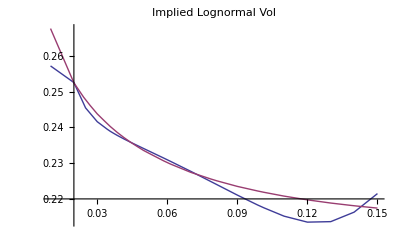
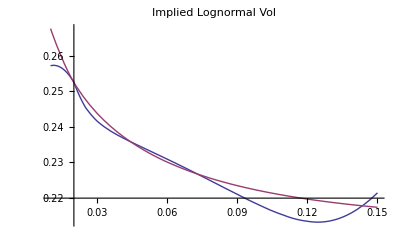
{3476.64,{-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.,ρsinf=0.,ρm1=0.,ρm2=0.,ρ1=-0.5,ρ2=-0.5, Σ1=0.04,Σ2=0.04,β=2.25,τ=5,λ1=1.1,λ2=1.1,ν1,S={0.04,0.0001},Q,strikes={0.01,0.02,0.025,0.03,0.035,0.038,0.04,0.042,0.045,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15},scope1,scope2,nb=250,integflag=0,coeffs=LegendreCoeffs[40],M,Σinf,Σ},
scope1=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=5/(√((Σ1+Σ2+θ1+θ2)/4 τ));
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
smile=Table[{strikes[[i]],ImpVolBS[S[[1]],strikes[[i]]+S[[2]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,S,β,λ1,λ2,scope1,scope2,nb,0]]},{i,1,Length[strikes]}];
inter=Interpolation[smile,InterpolationOrder->1];
inter1=Interpolation[smile,InterpolationOrder->2];
 Q=√(-M1 θ1)/β;
smile2=Table[{strikes[[i]],ImpVolBS[S[[1]]-S[[2]],strikes[[i]],τ,HestonCall2[S[[1]],strikes[[i]]+S[[2]],τ,Σ1,θ1,ρ1,-M1,Q,coeffs]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2,InterpolationOrder->1];
inter21=Interpolation[smile2,InterpolationOrder->2];
{Plot[{inter[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied Lognormal Vol",PlotLegend->{"BiHeston","Heston"}, LegendPosition->{1,0}, LegendSize->0.5],
Plot[{inter1[x],inter21[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied Lognormal Vol",PlotLegend->{"BiHeston","Heston"}, LegendPosition->{1,0}, LegendSize->0.5]}
]]
```

```mathematica
Timing[Module[{M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.,ρsinf=0.,ρm1=0.,ρm2=0.,ρ1=-0.5,ρ2=-0.5, Σ1=0.04,Σ2=0.04,β=2.25,τ=5,λ1=1.1,λ2=1.1,ν1,S={0.04,0.0001},Q,strikes={0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.08,0.1,0.12},scope1,scope2,nb=70,inter,inter2,integflag=0,coeffs=LegendreCoeffs[40],M,Σinf,Σ},
scope1=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=5/(√((Σ1+Σ2+θ1+θ2)/4 τ));
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
smile=Table[{strikes[[i]],NormalImplicitVol[S[[1]]-S[[2]],strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,S,β,λ1,λ2,scope1,scope2,nb,0]]},{i,1,Length[strikes]}];
inter=Interpolation[smile,InterpolationOrder->1];
 Q=√(-M1 θ1)/β;
smile2=Table[{strikes[[i]],NormalImplicitVol[S[[1]]-S[[2]],strikes[[i]],τ,HestonCall2[S[[1]],strikes[[i]]+S[[2]],τ,Σ1,θ1,ρ1,-M1,Q,coeffs]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2,InterpolationOrder->1];
Plot[{inter[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied Normal Vol",PlotLegend->{"BiHeston","Heston"}, LegendPosition->{1,0}, LegendSize->0.5]
]]
```

{53.586,-Graphics-}

## Comparaison with Montecarlo Calculations

Test of the Heston Formula

we use a function that computes the all smile in one shot :

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=150,flag=1,vol1,vol2,spdopt,StrikeList,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=100,dt,printflag=0},
dt=T/TimeStepsNb;
StrikeList={0.02,0.025,0.03,0.0325,0.035,0.037,0.039,0.041,0.043,0.045,0.0475,0.05,0.055,0.06};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=1;z2max=3;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
HestonMonteCarloSmile[StrikeList,M1,Σinf1,ρ1, Σ1,S1,β,TimeStepsNb,dt,nbSample,printflag]]]
```

β=2.25

{7.062,{0.0245178,0.0200306,0.0160621,0.0142936,0.0127151,0.0115819,0.0105933,0.00970611,0.00893601,0.00820456,0.00739942,0.00666619,0.0054356,0.00441009}}

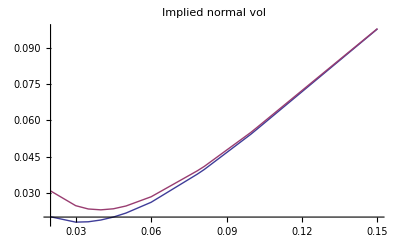
{219.915,-Graphics-}

```mathematica
Timing[Module[{M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.,ρsinf=0.,ρm1=0.,ρm2=0.,ρ1=-0.5,ρ2=-0.5, Σ1=0.04,Σ2=0.04,β=2.25,τ=5,λ1=1.1,λ2=1.1,ν1,S={0.04,0.0001},Q,strikes={0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.08,0.1,0.15},scope1,scope2,nb=70,inter,inter2,integflag=0,coeffs=LegendreCoeffs[40],dt,TimeStepsNb=200,nbSample=5000},
scope1=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=5/(√((Σ1+Σ2+θ1+θ2)/4 τ));dt=τ/TimeStepsNb;
 Q=√(-M1 θ1)/β;
smile2=Table[{strikes[[i]],NormalImplicitVol[S[[1]]-S[[2]],strikes[[i]],τ,HestonCall2[S[[1]],strikes[[i]]+S[[2]],τ,Σ1,θ1,ρ1,-M1,Q,coeffs]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2,InterpolationOrder->1];
pricelist=HestonMonteCarloSmile[strikes,M1,θ1,ρ1, Σ1,S[[1]],β,TimeStepsNb,dt,nbSample,0];
smile3=Table[{strikes[[i]],NormalImplicitVol[S[[1]]-S[[2]],strikes[[i]],τ,pricelist[[i]]]},{i,1,Length[strikes]}];
inter3=Interpolation[smile3,InterpolationOrder->1];

Plot[{inter2[x],inter3[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",PlotLegend->{"Heston","MC"}, LegendPosition->{1,0}, LegendSize->0.5]
]]
```

Test of the Bi Heston Formula

β=2.25

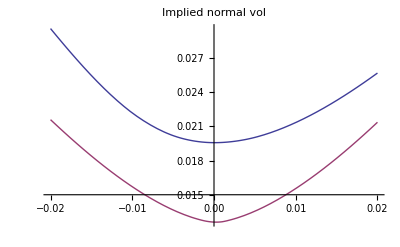
{577.625,-Graphics-}

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=120,flag=1,vol1,vol2,spdopt,inter,inter2,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=10000,dt,printflag=0,ΣinfM},
dt=T/TimeStepsNb;
StrikeList={-0.02,-0.015,-0.01,-0.007,-0.005,-0.003,-0.002,-0.001,0.001,0.002,0.003,0.005,0.007,0.01,0.015,0.02};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=3;z2max=5;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Σ=({{Σ1, √(Σ1 Σ2) ρ12}, {√(Σ1 Σ2) ρ12, Σ2}});
Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
pricelist=BiHestonMonteCarloSmile[StrikeList,M,Q,ΣinfM,{ρ1,ρ2}, {Σ1,√(Σ1 Σ2) ρ12,Σ2},{S1,S2},β,TimeStepsNb,dt,nbSample,printflag];
smile=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,pricelist[[i]]]},{i,1,Length[StrikeList]}];
inter=Interpolation[smile];
smile2=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter2=Interpolation[smile2];
Plot[{inter[x],inter2[x]},{x,StrikeList[[1]],Last[StrikeList]},PlotLabel->"Implied normal vol",PlotLegend->{"MC","Analytical"}]
]]
```

β=2.25

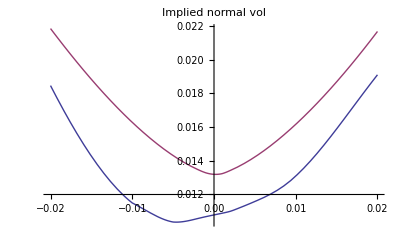
{29.11,-Graphics-}

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=40,flag=1,vol1,vol2,spdopt,inter,inter2,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=40,dt,printflag=0,ΣinfM},
dt=T/TimeStepsNb;
StrikeList={-0.02,-0.015,-0.01,-0.007,-0.005,-0.003,-0.002,-0.001,0.001,0.002,0.003,0.005,0.007,0.01,0.015,0.02};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=2.5;z2max=4.5;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Σ=({{Σ1, √(Σ1 Σ2) ρ12}, {√(Σ1 Σ2) ρ12, Σ2}});
Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
pricelist=BiHestonMonteCarloSmile[StrikeList,M,Q,ΣinfM,{ρ1,ρ2}, {Σ1,√(Σ1 Σ2) ρ12,Σ2},{S1,S2},β,TimeStepsNb,dt,nbSample,printflag];
smile=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,pricelist[[i]]]},{i,1,Length[StrikeList]}];
inter=Interpolation[smile];
smile2=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter2=Interpolation[smile2];
Plot[{inter[x],inter2[x]},{x,StrikeList[[1]],Last[StrikeList]},PlotLabel->"Implied normal vol",PlotLegend->{"MC","Analytical"}]
]]
```

β=2.25

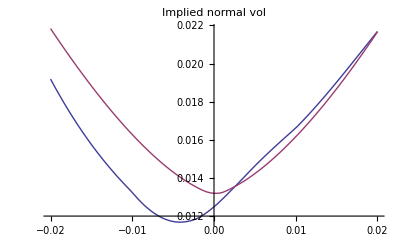
{29.141,-Graphics-}

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=40,flag=1,vol1,vol2,spdopt,inter,inter2,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=40,dt,printflag=0,ΣinfM},
dt=T/TimeStepsNb;
StrikeList={-0.02,-0.015,-0.01,-0.007,-0.005,-0.003,-0.002,-0.001,0.001,0.002,0.003,0.005,0.007,0.01,0.015,0.02};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=2.5;z2max=4.5;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Σ=({{Σ1, √(Σ1 Σ2) ρ12}, {√(Σ1 Σ2) ρ12, Σ2}});
Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
pricelist=BiHestonMonteCarloSmile[StrikeList,M,Q,ΣinfM,{ρ1,ρ2}, {Σ1,√(Σ1 Σ2) ρ12,Σ2},{S1,S2},β,TimeStepsNb,dt,nbSample,printflag];
smile=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,pricelist[[i]]]},{i,1,Length[StrikeList]}];
inter=Interpolation[smile];
smile2=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter2=Interpolation[smile2];
Plot[{inter[x],inter2[x]},{x,StrikeList[[1]],Last[StrikeList]},PlotLabel->"Implied normal vol",PlotLegend->{"MC","Analytical"}]
]]
```

β=2.25

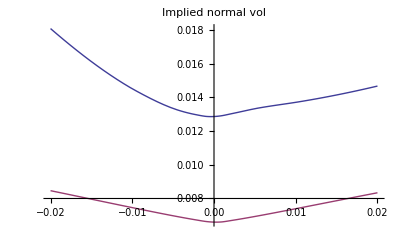
{81.375,-Graphics-}

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=40,flag=1,vol1,vol2,spdopt,inter,inter2,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=40,dt,printflag=0,ΣinfM},
dt=T/TimeStepsNb;
StrikeList={-0.02,-0.015,-0.01,-0.007,-0.005,-0.003,-0.002,-0.001,0.001,0.002,0.003,0.005,0.007,0.01,0.015,0.02};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=2.5;z2max=4.5;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Σ=({{Σ1, √(Σ1 Σ2) ρ12}, {√(Σ1 Σ2) ρ12, Σ2}});
Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
pricelist=BiHestonMonteCarloSmile[StrikeList,M,Q,ΣinfM,{ρ1,ρ2}, {Σ1,√(Σ1 Σ2) ρ12,Σ2},{S1,S2},β,TimeStepsNb,dt,nbSample,printflag];
smile=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,pricelist[[i]]]},{i,1,Length[StrikeList]}];
inter=Interpolation[smile];
smile2=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter2=Interpolation[smile2];
Plot[{inter[x],inter2[x]},{x,StrikeList[[1]],Last[StrikeList]},PlotLabel->"Implied normal vol",PlotLegend->{"MC","Analytical"}]
]]
```

β=2.25

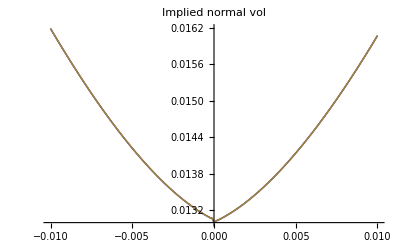
{7969.55,-Graphics-}

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=40,flag=1,vol1,vol2,spdopt,inter,inter2,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=40,dt,printflag=0,ΣinfM},
dt=T/TimeStepsNb;
StrikeList={-0.01,-0.007,-0.005,-0.003,-0.002,-0.001,-0.0007,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.0007,0.001,0.002,0.003,0.005,0.007,0.01};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=2.5;z2max=4.5;Nb1=80;Nb2=200;Nb3=500;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Σ=({{Σ1, √(Σ1 Σ2) ρ12}, {√(Σ1 Σ2) ρ12, Σ2}});
Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
smile2=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,Nb1,printflag]]},{i,1,Length[StrikeList]}];
inter2=Interpolation[smile2];
smile3=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,Nb2,printflag]]},{i,1,Length[StrikeList]}];
inter3=Interpolation[smile3];
smile4=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1,scope2,Nb3,printflag]]},{i,1,Length[StrikeList]}];
inter4=Interpolation[smile4];
Plot[{inter2[x],inter3[x],inter4[x]},{x,StrikeList[[1]],Last[StrikeList]},PlotLabel->"Implied normal vol",PlotLegend->{"NB="<>ToString[Nb1],"NB="<>ToString[Nb2],"NB="<>ToString[Nb3]}]
]]
```

β=2.25

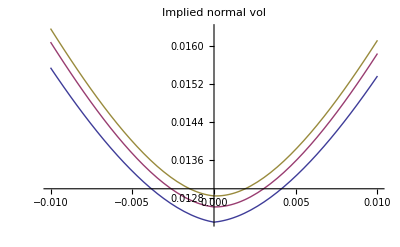
{391.843,-Graphics-}

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb,flag=1,vol1,vol2,spdopt,inter,inter2,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=40,dt,printflag=0,ΣinfM},
dt=T/TimeStepsNb;
StrikeList={-0.01,-0.007,-0.005,-0.003,-0.002,-0.001,-0.0007,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.0007,0.001,0.002,0.003,0.005,0.007,0.01};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=2.5;z2max=4.5;Nb=60;mul1=1.5;mul2=2;mul3=2.2;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Σ=({{Σ1, √(Σ1 Σ2) ρ12}, {√(Σ1 Σ2) ρ12, Σ2}});
Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
smile2=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla2[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul1,scope2 mul1,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter2=Interpolation[smile2];
smile3=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla2[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul2,scope2 mul2,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter3=Interpolation[smile3];
smile4=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla2[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul3,scope2 mul3,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter4=Interpolation[smile4];
Plot[{inter2[x],inter3[x],inter4[x]},{x,StrikeList[[1]],Last[StrikeList]},PlotLabel->"Implied normal vol",PlotLegend->{"mul="<>ToString[mul1],"mul="<>ToString[mul2],"mul="<>ToString[mul3]}]
]]
```

β=2.25

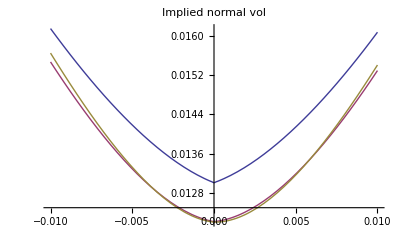
{686.825,-Graphics-}

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb,flag=1,vol1,vol2,spdopt,inter,inter2,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=40,dt,printflag=0,ΣinfM},
dt=T/TimeStepsNb;
StrikeList={-0.01,-0.007,-0.005,-0.003,-0.002,-0.001,-0.0007,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.0007,0.001,0.002,0.003,0.005,0.007,0.01};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=2.5;z2max=4.5;Nb=80;mul1=1;mul2=1.5;mul3=2.;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Σ=({{Σ1, √(Σ1 Σ2) ρ12}, {√(Σ1 Σ2) ρ12, Σ2}});
Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
smile2=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla2[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul1,scope2 mul1,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter2=Interpolation[smile2];
smile3=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla2[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul2,scope2 mul2,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter3=Interpolation[smile3];
smile4=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla2[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul3,scope2 mul3,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter4=Interpolation[smile4];
Plot[{inter2[x],inter3[x],inter4[x]},{x,StrikeList[[1]],Last[StrikeList]},PlotLabel->"Implied normal vol",PlotLegend->{"mul="<>ToString[mul1],"mul="<>ToString[mul2],"mul="<>ToString[mul3]}]
]]
```

β=2.25

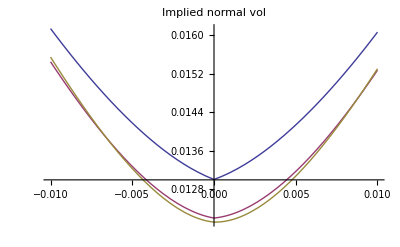
{1527.86,-Graphics-}

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=40,flag=1,vol1,vol2,spdopt,inter,inter2,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=40,dt,printflag=0,ΣinfM},
dt=T/TimeStepsNb;
StrikeList={-0.01,-0.007,-0.005,-0.003,-0.002,-0.001,-0.0007,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.0007,0.001,0.002,0.003,0.005,0.007,0.01};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=2.5;z2max=4.5;Nb=120;mul1=1;mul2=1.5;mul3=2.;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Σ=({{Σ1, √(Σ1 Σ2) ρ12}, {√(Σ1 Σ2) ρ12, Σ2}});
Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
smile2=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla2[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul1,scope2 mul1,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter2=Interpolation[smile2];
smile3=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla2[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul2,scope2 mul2,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter3=Interpolation[smile3];
smile4=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla2[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul3,scope2 mul3,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter4=Interpolation[smile4];
Plot[{inter2[x],inter3[x],inter4[x]},{x,StrikeList[[1]],Last[StrikeList]},PlotLabel->"Implied normal vol",PlotLegend->{"mul="<>ToString[mul1],"mul="<>ToString[mul2],"mul="<>ToString[mul3]}]
]]
```

```mathematica
inter4=Interpolation[smile4,InterpolationOrder->1];
```

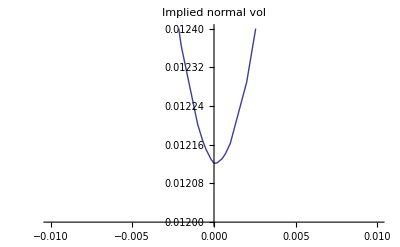

```mathematica
Plot[{inter4[x]},{x,StrikeList[[1]],Last[StrikeList]},PlotLabel->"Implied normal vol",PlotLegend->{"mul="<>ToString[mul3]},PlotRange->{0.012,0.0124}]
```

β=2.25

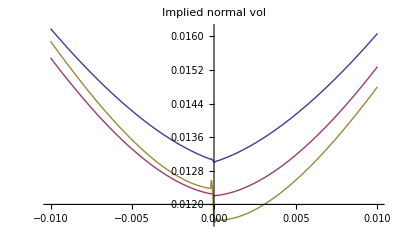
{1271.81,-Graphics-}

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=40,flag=1,vol1,vol2,spdopt,inter,inter2,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=40,dt,printflag=0,ΣinfM},
dt=T/TimeStepsNb;
StrikeList={-0.01,-0.007,-0.005,-0.003,-0.002,-0.001,-0.0007,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.0007,0.001,0.002,0.003,0.005,0.007,0.01};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=2.5;z2max=4.5;Nb=120;mul1=1;mul2=1.5;mul3=2.5;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Σ=({{Σ1, √(Σ1 Σ2) ρ12}, {√(Σ1 Σ2) ρ12, Σ2}});
Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
smile2=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul1,scope2 mul1,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter2=Interpolation[smile2];
smile3=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul2,scope2 mul2,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter3=Interpolation[smile3];
smile4=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul3,scope2 mul3,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter4=Interpolation[smile4];
Plot[{inter2[x],inter3[x],inter4[x]},{x,StrikeList[[1]],Last[StrikeList]},PlotLabel->"Implied normal vol",PlotLegend->{"mul="<>ToString[mul1],"mul="<>ToString[mul2],"mul="<>ToString[mul3]}]
]]
```

β=2.25

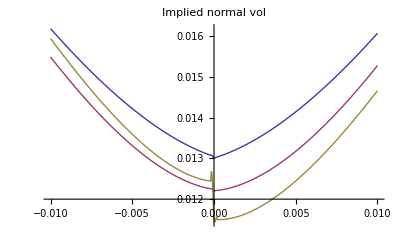
{20549.9,-Graphics-}

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=40,flag=1,vol1,vol2,spdopt,inter,inter2,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=40,dt,printflag=0,ΣinfM},
dt=T/TimeStepsNb;
StrikeList={-0.01,-0.007,-0.005,-0.003,-0.002,-0.001,-0.0007,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.0007,0.001,0.002,0.003,0.005,0.007,0.01};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=2.5;z2max=4.5;Nb=500;mul1=1;mul2=1.5;mul3=2.5;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Σ=({{Σ1, √(Σ1 Σ2) ρ12}, {√(Σ1 Σ2) ρ12, Σ2}});
Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
smile2=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul1,scope2 mul1,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter2=Interpolation[smile2];
smile3=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul2,scope2 mul2,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter3=Interpolation[smile3];
smile4=Table[{StrikeList[[i]],NormalImplicitVol[S1-S2,StrikeList[[i]],T,
NewSuperBiHestonVanilla[StrikeList[[i]],T,M,ΣinfM,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,scope1 mul3,scope2 mul3,Nb,printflag]]},{i,1,Length[StrikeList]}];
inter4=Interpolation[smile4];
Plot[{inter2[x],inter3[x],inter4[x]},{x,StrikeList[[1]],Last[StrikeList]},PlotLabel->"Implied normal vol",PlotLegend->{"mul="<>ToString[mul1],"mul="<>ToString[mul2],"mul="<>ToString[mul3]}]
]]
```

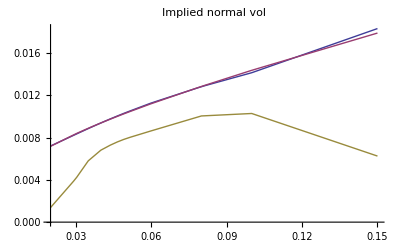
{250.078,-Graphics-}

```mathematica
Timing[Module[{M1=-0.075,M2=-0.075,θ1=0.15,θ2=0.15,ρs=0.,ρsinf=0.,ρm1=0.,ρm2=0.,ρ1=-0.5,ρ2=-0.5, Σ1=0.04,Σ2=0.04,β=2.25,τ=5,λ1=1.1,λ2=1.1,ν1,S={0.04,0.0001},Q,strikes={0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.08,0.1,0.15},scope1,scope2,nb=70,inter,inter2,integflag=0,coeffs=LegendreCoeffs[40],dt,TimeStepsNb=100,nbSample=400,M,Σinf,Σ},
scope1=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=5/(√((Σ1+Σ2+θ1+θ2)/4 τ));dt=τ/TimeStepsNb;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
smile=Table[{strikes[[i]],NormalImplicitVol[S[[1]]-S[[2]],strikes[[i]],τ,SuperBiHestonCall[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,S,β,λ1,λ2,scope1,scope2,nb,0]]},{i,1,Length[strikes]}];
inter=Interpolation[smile,InterpolationOrder->1];
 Q=√(-M1 θ1)/β;
smile2=Table[{strikes[[i]],NormalImplicitVol[S[[1]]-S[[2]],strikes[[i]],τ,HestonCall2[S[[1]],strikes[[i]]+S[[2]],τ,Σ1,θ1,ρ1,-M1,Q,coeffs]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2,InterpolationOrder->1];
pricelist=BiHestonMonteCarloSmile[strikes,M,Σinf,{ρ1,ρ2}, Σ,S,β,TimeStepsNb,dt,nbSample,0];
smile3=Table[{strikes[[i]],NormalImplicitVol[S[[1]]-S[[2]],strikes[[i]],τ,pricelist[[i]]]},{i,1,Length[strikes]}];
inter3=Interpolation[smile3,InterpolationOrder->1];

Plot[{inter[x],inter2[x],inter3[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",PlotLegend->{"BiHeston","Heston","MC"}, LegendPosition->{1,0}, LegendSize->0.5]
]]
```

# Appendices

## Appendix 1

## Computation of the Fourier transform of the payoff

Case K > 0

```mathematica
integration1=Simplify[∫_Log[ⅇ^x2+K]^∞ ⅇ^(ⅈ k1 x1)(α ⅇ^x1-β ⅇ^x2-K)ⅆx1]
```

If[Im[k1]>1,((ⅇ^x2+K)^(ⅈ k1) (K (ⅈ+k1 (-1+α))+ⅇ^x2 (k1 (α-β)+ⅈ β)))/((-1-ⅈ k1) k1),Integrate[-ⅇ^(ⅈ k1 x1) K+ⅇ^(x1+ⅈ k1 x1) α-ⅇ^(ⅈ k1 x1+x2) β,{x1,Log[ⅇ^x2+K],∞},Assumptions→Im[k1]≤1]]

```mathematica
integration11=Simplify[integration1,Im[k1]>1]
```

((ⅇ^x2+K)^(ⅈ k1) (K (ⅈ+k1 (-1+α))+ⅇ^x2 (k1 (α-β)+ⅈ β)))/((-1-ⅈ k1) k1)

```mathematica
Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration11,x2],K>0]
```

1/((-1-ⅈ k1) k1 k2 (-ⅈ+k2))ⅇ^(ⅈ k2 x2) K^(ⅈ k1) (ⅇ^x2 k2 (-ⅈ k1 (α-β)+β) Hypergeometric2F1[-ⅈ k1,1+ⅈ k2,2+ⅈ k2,-ⅇ^x2/K]+K (-ⅈ+k2) (1-ⅈ k1 (-1+α)) Hypergeometric2F1[-ⅈ k1,ⅈ k2,1+ⅈ k2,-ⅇ^x2/K])

ca converge pour Im[k1] > 1,  Im[k2] > 0  pour x2 ∈ [G, +∞[

Case K = 0

```mathematica
integration2=Simplify[∫_x2^∞ ⅇ^(ⅈ k1 x1)(α ⅇ^x1-β ⅇ^x2)ⅆx1]
```

If[Im[k1]>1,(ⅇ^(x2+ⅈ k1 x2) (k1 (α-β)+ⅈ β))/((-1-ⅈ k1) k1),Integrate[ⅇ^(x1+ⅈ k1 x1) α-ⅇ^(ⅈ k1 x1+x2) β,{x1,x2,∞},Assumptions→Im[k1]≤1]]

```mathematica
integration22=Simplify[integration2,Im[k1]>1]
```

(ⅇ^(x2+ⅈ k1 x2) (k1 (α-β)+ⅈ β))/((-1-ⅈ k1) k1)

```mathematica
Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration22,x2],K>0]
```

(ⅇ^(ⅈ (-ⅈ+k1+k2) x2) (k1 (α-β)+ⅈ β))/(k1 (-ⅈ+k1) (-ⅈ+k1+k2))

We can check that it is indeed the limit of K→0^+

```mathematica
Simplify[Integrate[ⅇ^(ⅈk2 x2)(integration11 /. K->0),x2],x2>0]
```

(ⅇ^(x2 (1+ⅈ k1+ⅈk2)) (k1 (α-β)+ⅈ β))/(k1 (-ⅈ+k1) (k1-ⅈ (1+ⅈk2)))

Check of the Fourier Transform numerically K>0

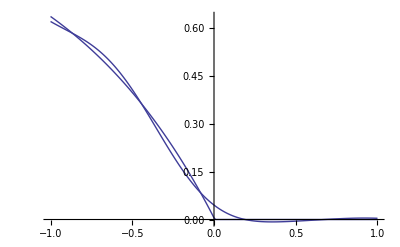
{611.187,-Graphics-}

```mathematica
Timing[Module[{x1=0.1,K=0.1,λ=2,λ2=1.2,G=-10},g1=ListPlot[Table[{i/100,Re[Module[{x2=i/100},1/(2π)^2 CoeffBasedIntegrate[(ⅇ^(-ⅈ x1( #1+ⅈ λ)-ⅈ x2( #2-ⅈ λ2))CompleteFourierPayOffGauche[#1+ⅈ λ,( #2-ⅈ λ2),K]+ⅇ^(-ⅈ x1( #1+ⅈ λ)-ⅈ x2( #2+ⅈ λ2))CompleteFourierPayOffDroite[#1+ⅈ λ,( #2+ⅈ λ2),K])&,RiemanCoeffs[40,-8,8],RiemanCoeffs[40,-8,8]]]]},{i,-100,100}],Joined->True];
g2=ListPlot[Table[{i/100,Module[{x2=i/100},Re[PayOff[x1,x2,K]]]},{i,-100,100}],Joined->True];
Show[g1,g2,PlotRange->All]]]
```

Check of the Fourier Transform numerically K==0

```mathematica
Timing[Module[{x1=0.1,λ=2,λ2=1.2,G=-10},g1=ListPlot[Table[{i/100,Re[Module[{x2=i/100},1/(2π)^2 CoeffBasedIntegrate[(ⅇ^(-ⅈ x1( #1+ⅈ λ)-ⅈ x2( #2-ⅈ λ2))CompleteFourierPayOffGauche[#1+ⅈ λ,( #2-ⅈ λ2)]+ⅇ^(-ⅈ x1( #1+ⅈ λ)-ⅈ x2( #2+ⅈ λ2))CompleteFourierPayOffDroite[#1+ⅈ λ,( #2+ⅈ λ2)])&,RiemanCoeffs[40,-8,8],RiemanCoeffs[40,-8,8]]]]},{i,-100,100}],Joined->True];
g2=ListPlot[Table[{i/100,Module[{x2=i/100},Re[PayOff[x1,x2]]]},{i,-100,100}],Joined->True];
Show[g1,g2,PlotRange->All]]]
```

{611.187,-Graphics-}

## Appendix 2

## Computation of the β optimal

Mais il faut que les valeur propres de M soient negatives, c' est equivalent a une trace negative et un determinant positif, c' est a dire

```mathematica
Det[({{(-Subscript[λ, 1])/2, (Subscript[λ, 2] Subscript[Σ, ∞2]-β (Subscript[ν, 2]^2/4))/(2 Subscript[Σ, 12])}, {(Subscript[λ, 1] Subscript[Σ, ∞1]-β (Subscript[ν, 1]^2/4))/(2 Subscript[Σ, 12]), (-Subscript[λ, 2])/2}})]>0
```

Soit encore

```mathematica
Simplify[Det[({{(-Subscript[λ, 1])/2, (Subscript[λ, 2] Subscript[Σ, ∞2]-β (Subscript[ν, 2]^2/4))/(2 Subscript[Σ, 12])}, {(Subscript[λ, 1] Subscript[Σ, ∞1]-β (Subscript[ν, 1]^2/4))/(2 Subscript[Σ, 12]), (-Subscript[λ, 2])/2}})]]
```

(β ν_1^2 (-β ν_2^2+4 λ_2 Σ_(∞2))+4 λ_1 (β ν_2^2 Σ_(∞1)+4 λ_2 (Σ_12^2-Σ_(∞1) Σ_(∞2))))/(64 Σ_12^2)

la question est quant pour β>1 on peut avoir β ν_1^2 (-β ν_2^2+4 λ_2 Σ_(∞2))+4 λ_1 (β ν_2^2 Σ_(∞1)+4 λ_2 (Σ_12^2-Σ_(∞1) Σ_(∞2)))>0

```mathematica
Collect[ β Subscript[ν, 1]^2 (-β Subscript[ν, 2]^2+4 Subscript[λ, 2] Subscript[Σ, ∞2])+4 Subscript[λ, 1] (β Subscript[ν, 2]^2 Subscript[Σ, ∞1]+4 Subscript[λ, 2] (Subscript[Σ, 12]^2-Subscript[Σ, ∞1] Subscript[Σ, ∞2])),β]
```

Sum::sumwarn: Warning: Σ_12 2 contains a capital sigma; use EscsumEsc to enter a summation sign.

-β^2 ν_1^2 ν_2^2+β (4 λ_1 ν_2^2 Σ_(∞1)+4 λ_2 ν_1^2 Σ_(∞2))+16 λ_1 λ_2 (Σ_12^2-Σ_(∞1) Σ_(∞2))

```mathematica
F[β_]:=-β^2 Subscript[ν, 1]^2 Subscript[ν, 2]^2+β (4 Subscript[λ, 1] Subscript[ν, 2]^2 Subscript[Σ, ∞1]+4 Subscript[λ, 2] Subscript[ν, 1]^2 Subscript[Σ, ∞2])+16 Subscript[λ, 1] Subscript[λ, 2] (Subscript[Σ, 12]^2-Subscript[Σ, ∞1] Subscript[Σ, ∞2])
```

Sum::sumwarn: Warning: Σ_12 2 contains a capital sigma; use EscsumEsc to enter a summation sign.

```mathematica
Solve[D[F[β],β] ==0,β]
```

{{β→(2 (λ_1 ν_2^2 Σ_(∞1)+λ_2 ν_1^2 Σ_(∞2)))/(ν_1^2 ν_2^2)}}

let define β_1=(2 λ_1 Σ_(∞1))/ν_1^2 and β_2=(2 λ_2 Σ_(∞2))/ν_2^2  on naturellement β_1>1 et β_2>1

et

β_optimal=β_1+β_2

```mathematica
Simplify[F[β]/. Solve[D[F[β],β] ==0,β]]
```

{4 ((λ_1^2 ν_2^2 Σ_(∞1)^2)/ν_1^2+(λ_2^2 ν_1^2 Σ_(∞2)^2)/ν_2^2+2 λ_1 λ_2 (2 Σ_12^2-Σ_(∞1) Σ_(∞2)))}

```mathematica
Simplify[(Subscript[λ, 1]^2 Subscript[ν, 2]^2 Subscript[Σ, ∞1]^2)/Subscript[ν, 1]^2+(Subscript[λ, 2]^2 Subscript[ν, 1]^2 Subscript[Σ, ∞2]^2)/Subscript[ν, 2]^2 /. {Subscript[Σ, ∞1]-> (Subscript[β, 1] Subscript[ν, 1]^2)/(2 Subscript[λ, 1]),Subscript[Σ, ∞2]-> (Subscript[β, 2] Subscript[ν, 2]^2)/(2 Subscript[λ, 2])}]
```

Sum::sumwarn: Warning: Σ_∞1 2 contains a capital sigma; use EscsumEsc to enter a summation sign.

Sum::sumwarn: Warning: Σ_∞2 2 contains a capital sigma; use EscsumEsc to enter a summation sign.

1/4 (β_1^2+β_2^2) ν_1^2 ν_2^2

F[β_optimal]=4 ((λ_1^2 ν_2^2 Σ_(∞1)^2)/ν_1^2+(λ_2^2 ν_1^2 Σ_(∞2)^2)/ν_2^2+2 λ_1 λ_2 (2 Σ_12^2-Σ_(∞1) Σ_(∞2)))=1/4 (β_1^2+β_2^2-2 β_1 β_2) ν_1^2 ν_2^2+16 λ_1 λ_2  Σ_12^2=1/4(β_1+β_2)^2+16 λ_1 λ_2  Σ_12^2=1/4(β_optimal)^2+16 λ_1 λ_2  Σ_12^2

Donc  β_optimal >1 et  F[β_optimal] >0

```mathematica
pour que les valeur propre de M soient reelle, il faut aussi que le discriminant >0
```

```mathematica
discriminant=trace^2-4determinant
```

```mathematica
Simplify[Tr[({{(-Subscript[λ, 1])/2, (Subscript[λ, 2] Subscript[Σ, ∞2]-β (Subscript[ν, 2]^2/4))/(2 Subscript[Σ, 12])}, {(Subscript[λ, 1] Subscript[Σ, ∞1]-β (Subscript[ν, 1]^2/4))/(2 Subscript[Σ, 12]), (-Subscript[λ, 2])/2}})]^2-4Det[({{(-Subscript[λ, 1])/2, (Subscript[λ, 2] Subscript[Σ, ∞2]-β (Subscript[ν, 2]^2/4))/(2 Subscript[Σ, 12])}, {(Subscript[λ, 1] Subscript[Σ, ∞1]-β (Subscript[ν, 1]^2/4))/(2 Subscript[Σ, 12]), (-Subscript[λ, 2])/2}})] //.  {Subscript[Σ, ∞1]-> (Subscript[β, 1] Subscript[ν, 1]^2)/(2 Subscript[λ, 1]),Subscript[Σ, ∞2]-> (Subscript[β, 2] Subscript[ν, 2]^2)/(2 Subscript[λ, 2])}]
```

((β-2 β_1) (β-2 β_2) ν_1^2 ν_2^2+4 (λ_1-λ_2)^2 Σ_12^2)/(16 Σ_12^2)

```mathematica
donc si β est plus grand que 2 Subscript[β, 1] et 2 Subscript[β, 2] ce sera positif
```

```mathematica
βOptimal[ν1_,χ1_,Σinf1_,ν2_,χ2_,Σinf2_]:=(2 (χ1 ν2^2 Σinf1+χ2 ν1^2 Σinf2))/(ν1^2 ν2^2)
```

```mathematica
βOptimal2[ν1_,χ1_,Σinf1_,ν2_,χ2_,Σinf2_]:=(4 (Max[χ1 ν2^2 Σinf1,χ2 ν1^2 Σinf2]))/(ν1^2 ν2^2)
```

```mathematica
MDeterminant[ν1_,χ1_,Σinf1_,ν2_,χ2_,Σinf2_,Σ12_,β_]:=-β^2 ν1^2 ν2^2+β (4 χ1  ν2^2 Σinf1+4 χ2 ν1^2 Σinf2)+16 χ1 χ2 (Σ12^2-Σinf1 Σinf2)
```

geometrie du risque : rapprochement avec Heston

```mathematica
Clear[Q11,Q12,Q21,Q22]
```

```mathematica
Simplify[Solve[{Q11^2+Q21^2==ν1^2/4,Q11 ρ1+Q21 ρ2 ==ν1/2 ρs1,Q12^2+Q22^2==ν2^2/4,Q12 ρ1+Q22 ρ2 ==ν2/2 ρs2},{Q11,Q21,Q12,Q22}],(ν1>0)&&(ν2>0)]
```

{{Q11→(ν1 (ρ1^2 ρs1-ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 ρ1 (ρ1^2+ρ2^2)),Q21→(ν1 (ρ2 ρs1+√(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 (ρ1^2+ρ2^2)),Q12→(ν2 (ρ1^2 ρs2-ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2))))/(2 ρ1 (ρ1^2+ρ2^2)),Q22→(ν2 (ρ2 ρs2+√(ρ1^2 (ρ1^2+ρ2^2-ρs2^2))))/(2 (ρ1^2+ρ2^2))},{Q11→(ν1 (ρ1^2 ρs1-ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 ρ1 (ρ1^2+ρ2^2)),Q21→(ν1 (ρ2 ρs1+√(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 (ρ1^2+ρ2^2)),Q12→(ν2 (ρ1^2 ρs2+ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2))))/(2 ρ1 (ρ1^2+ρ2^2)),Q22→(ν2 ρ2 ρs2-ν2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2)))/(2 (ρ1^2+ρ2^2))},{Q11→(ν1 (ρ1^2 ρs1+ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 ρ1 (ρ1^2+ρ2^2)),Q21→(ν1 ρ2 ρs1-ν1 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2)))/(2 (ρ1^2+ρ2^2)),Q12→(ν2 (ρ1^2 ρs2-ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2))))/(2 ρ1 (ρ1^2+ρ2^2)),Q22→(ν2 (ρ2 ρs2+√(ρ1^2 (ρ1^2+ρ2^2-ρs2^2))))/(2 (ρ1^2+ρ2^2))},{Q11→(ν1 (ρ1^2 ρs1+ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 ρ1 (ρ1^2+ρ2^2)),Q21→(ν1 ρ2 ρs1-ν1 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2)))/(2 (ρ1^2+ρ2^2)),Q12→(ν2 (ρ1^2 ρs2+ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2))))/(2 ρ1 (ρ1^2+ρ2^2)),Q22→(ν2 ρ2 ρs2-ν2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2)))/(2 (ρ1^2+ρ2^2))}}

Les quatre solution sont equivalente car redonne les meme observables

```mathematica
DetermineQ[ρ1_,ρ2_,ν1_,ν2_,ρs1_,ρs2_,printflag_]:=Module[{Q11,Q21,Q12,Q22},
If[(ρ1≠0)||(ρ2≠0),
Q11=(ν1 ( ρ1 ρs1-ρ2 √(ρ1^2+ρ2^2- ρs1^2)))/(2  (ρ1^2+ρ2^2));Q21=(ν1 ( ρ2 ρs1+√(ρ1^2 (ρ1^2+ρ2^2- ρs1^2))))/(2 (ρ1^2+ρ2^2));Q12=(ν2 ( ρ1 ρs2-ρ2 √(ρ1^2+ρ2^2- ρs2^2)))/(2  (ρ1^2+ρ2^2));Q22=(ν2 (ρ2 ρs2+√(ρ1^2 (ρ1^2+ρ2^2- ρs2^2))))/(2 (ρ1^2+ρ2^2));
If[((Q11==0)&&(Q12==0))||((Q21==0)&&(Q22==0)),Q11=(ν1 (ρ1^2 ρs1-ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 ρ1 (ρ1^2+ρ2^2));Q21=(ν1 (ρ2 ρs1+√(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 (ρ1^2+ρ2^2));Q12=(ν2 (ρ1^2 ρs2+ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2))))/(2 ρ1 (ρ1^2+ρ2^2));Q22=(ν2 ρ2 ρs2-ν2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2)))/(2 (ρ1^2+ρ2^2))];
If[((Q11==0)&&(Q12==0))||((Q21==0)&&(Q22==0)),Q11=(ν1 (ρ1^2 ρs1+ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 ρ1 (ρ1^2+ρ2^2));Q21=(ν1 ρ2 ρs1-ν1 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2)))/(2 (ρ1^2+ρ2^2));Q12=(ν2 (ρ1^2 ρs2-ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2))))/(2 ρ1 (ρ1^2+ρ2^2));Q22=(ν2 (ρ2 ρs2+√(ρ1^2 (ρ1^2+ρ2^2-ρs2^2))))/(2 (ρ1^2+ρ2^2))];
If[((Q11==0)&&(Q12==0))||((Q21==0)&&(Q22==0)),Q11=(ν1 (ρ1^2 ρs1+ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 ρ1 (ρ1^2+ρ2^2));Q21=(ν1 ρ2 ρs1-ν1 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2)))/(2 (ρ1^2+ρ2^2));Q12=(ν2 (ρ1^2 ρs2+ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2))))/(2 ρ1 (ρ1^2+ρ2^2));Q22=(ν2 ρ2 ρs2-ν2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2)))/(2 (ρ1^2+ρ2^2))];
,Print["error: ρ1==0 and ρ2==0"];

]
If[printflag>0,Print["{ρ1,ρ2,ν1,ν2,ρs1,ρs2}=",{ρ1,ρ2,ν1,ν2,ρs1,ρs2}]];
If[printflag>0,Print["Autres sol=",{{(ν1 (ρ1^2 ρs1-ρ2 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 ρ1 (ρ1^2+ρ2^2)),(ν1 (ρ2 ρs1+√(ρ1^2 (ρ1^2+ρ2^2-ρs1^2))))/(2 (ρ1^2+ρ2^2)),(ν2 (ρ1 ρs2+ρ2 √(ρ1^2+ρ2^2-ρs2^2)))/(2 (ρ1^2+ρ2^2)),(ν2 ρ2 ρs2-ν2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2)))/(2 (ρ1^2+ρ2^2))},{(ν1 (ρ1 ρs1+ρ2 √(ρ1^2+ρ2^2-ρs1^2)))/(2 (ρ1^2+ρ2^2)),(ν1 ρ2 ρs1-ν1 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2)))/(2 (ρ1^2+ρ2^2)),(ν2 (ρ1 ρs2-ρ2 √(ρ1^2+ρ2^2-ρs2^2)))/(2  (ρ1^2+ρ2^2)),(ν2 (ρ2 ρs2+√(ρ1^2 (ρ1^2+ρ2^2-ρs2^2))))/(2 (ρ1^2+ρ2^2))},{(ν1 (ρ1 ρs1+ρ2 √(ρ1^2+ρ2^2-ρs1^2)))/(2  (ρ1^2+ρ2^2)),(ν1 ρ2 ρs1-ν1 √(ρ1^2 (ρ1^2+ρ2^2-ρs1^2)))/(2 (ρ1^2+ρ2^2)),(ν2 (ρ1 ρs2+ρ2 √(ρ1^2+ρ2^2-ρs2^2)))/(2  (ρ1^2+ρ2^2)),(ν2 ρ2 ρs2-ν2 √(ρ1^2 (ρ1^2+ρ2^2-ρs2^2)))/(2 (ρ1^2+ρ2^2))}}]];
{{Q11,Q12},{Q21,Q22}}]
```

```mathematica
Module[{ν1=0.2,ν2=0.2,ρ1=0.5,ρ2=0.5,ρs1=-0.5,ρs2=-0.5},
Q=DetermineQ[ρ1,ρ2,ν1,ν2,ρs1,ρs2,1]]
```

{ρ1,ρ2,ν1,ν2,ρs1,ρs2}={0.5,0.5,0.2,0.2,-0.5,-0.5}

Autres sol={{-0.1,0.,0.,-0.1},{0.,-0.1,-0.1,0.},{0.,-0.1,0.,-0.1}}

{{-0.1,0.},{0.,-0.1}}

Determination du secteur du drift : rapprochement avec les hestons monodimentionnels

```mathematica
Σt={{Σ11,Σ12},{Σ12,Σ22}}
```

{{Σ11,Σ12},{Σ12,Σ22}}

```mathematica
M={{M11,M12},{M21,M22}}
```

{{M11,M12},{M21,M22}}

```mathematica
Simplify[Σt.M+Transpose[M].Σt]
```

{{2 (M11 Σ11+M21 Σ12),M12 Σ11+M11 Σ12+M22 Σ12+M21 Σ22},{M12 Σ11+M11 Σ12+M22 Σ12+M21 Σ22,2 (M12 Σ12+M22 Σ22)}}

```mathematica
Q={{Q11,Q12},{Q21,Q22}};
```

```mathematica
Transpose[Q].Q
```

{{Q11^2+Q21^2,Q11 Q12+Q21 Q22},{Q11 Q12+Q21 Q22,Q12^2+Q22^2}}

```mathematica
DetermineM[Q_,β_,Σinf1_,Σinf2_,χ1_,χ2_,Σ012_,flag_]:=Module[{M11=-χ1/2,M22=-χ2/2,M21,M12,M,ν1,ν2},
ν1=√(4(Q[[1,1]]^2+Q[[2,1]]^2));ν2=√(4(Q[[1,2]]^2+Q[[2,2]]^2));

M21=(β(Q[[1,1]]^2+Q[[2,1]]^2)-χ1 Σinf1)/(2Σ012);
M12=(β(Q[[1,2]]^2+Q[[2,2]]^2)-χ2 Σinf2)/(2Σ012);
M={{M11,M12},{M21,M22}};
If[flag==1,
Print["Q_,β,Σinf1,Σinf2,χ1,χ2,Σ012=",{Q,β,Σinf1,Σinf2,χ1,χ2,Σ012}];
Print["ν1^2/2-χ1 Σinf1 doit etre negatif 1 : ",ν1^2/2-χ1 Σinf1];
Print["ν2^2/2-χ2 Σinf2 doit etre negatif 2 : ",ν2^2/2-χ2 Σinf2];
Print["eigenvalues[M]=",Eigenvalues[M]];];
M
]
```

il faut verifier que (Tr[M] < 0 et Det[M] > 0)

```mathematica
Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σinf1=0.15,Σinf2=0.15,Σ012=0.12,ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,β=3,Q,M},
Q=DetermineQ[ρ1,ρ2,ν1,ν2,ρs1,ρs2,0];
M=DetermineM[Q,β,Σinf1,Σinf2,χ1,χ2,Σ012,1];
]
```

ν1^2/2-χ1 Σinf1 doit etre negatif 1 : -0.0025

ν2^2/2-χ2 Σinf2 doit etre negatif 2 : -0.0025

eigenvalues[M]={-0.10625,-0.04375}

## Appendix 3

## Matrix Exponential

```mathematica
If faut montrer que F = a11= ((2 ζ)/(ⅇ^(ζ τ/2)((M+ ρ Q  γ)+ζ)-ⅇ^(-ζ τ/2)(M+ ρ Q  γ-ζ)))
```

```mathematica
mais pour obtenir le bon A on doit changer en l'opposé: (peut etre t<-> τ )
```

```mathematica
H=({{(M+Q ρ γ)/2, (Q Q)/2}, {(-γ γ)/2, (-(M+Q ρ γ))/2}});ζ1=Simplify[-4Det[H]]
```

M^2+2 M Q γ ρ+Q^2 γ^2 (-1+ρ^2)

```mathematica
F =Simplify[Simplify[expM1.{1,0} /. {a->H[[1,1]],b->H[[1,2]],c->H[[2,1]],d->H[[2,2]]}] ][[1]]//.{√(M^2+2 M Q γ ρ+Q^2 γ^2 (-1+ρ^2))->ζ}
```

(ⅇ^(-(ζ τ)/2) ((-1+ⅇ^(ζ τ)) M+(1+ⅇ^(ζ τ)) ζ+(-1+ⅇ^(ζ τ)) Q γ ρ))/(2 √(M^2+2 M Q γ ρ+Q^2 γ^2 (-1+ρ^2)))

```mathematica
(ⅇ^(-(ζ τ)/2) ((-1+ⅇ^(ζ τ)) M+(1+ⅇ^(ζ τ)) ζ+(-1+ⅇ^(ζ τ)) Q γ ρ))/(2 ζ)
```

```mathematica
Si on diagonalise cette matrice , attention les matrice de passage ne sont pas orthogonale car la matrice n'est pas symetrique.
```

```mathematica
Soit une matrice h=({{a, b}, {c, d}})  on la diagonalise en :
```

```mathematica
h=1/(1+((-a+d+√Δ)/(2b))^2)({{1, (-a+d+√Δ)/(2b)}, {(-a+d+√Δ)/(2b), ((-a+d+√Δ)/(2b))^2}})Subscript[x, 1]+1/(1+((-a+d-√Δ)/(2b))^2)({{1, (-a+d-√Δ)/(2b)}, {(-a+d-√Δ)/(2b), ((-a+d-√Δ)/(2b))^2}})Subscript[x, 2]
```

```mathematica
ou Subscript[x, 1]=(a+d+√Δ)/2;Subscript[x, 2]=(a+d-√Δ)/2;Δ=a d-b c;
```

```mathematica
M1=({{7.1, 2}, {41, 3}})
```

{{7.1,2},{41,3}}

```mathematica
M1=({{a, b}, {c, d}})
```

```mathematica
Simplify[MatrixExp[M1]]
```

{{(ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2))) (d-d ⅇ^(√(a^2+4 b c-2 a d+d^2))+a (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2)))+√(a^2+4 b c-2 a d+d^2) (1+ⅇ^(√(a^2+4 b c-2 a d+d^2)))))/(2 √(a^2+4 b c-2 a d+d^2)),(b ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2))) (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2))))/(√(a^2+4 b c-2 a d+d^2))},{(c ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2))) (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2))))/(√(a^2+4 b c-2 a d+d^2)),(ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2))) (a-a ⅇ^(√(a^2+4 b c-2 a d+d^2))+d (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2)))+√(a^2+4 b c-2 a d+d^2) (1+ⅇ^(√(a^2+4 b c-2 a d+d^2)))))/(2 √(a^2+4 b c-2 a d+d^2))}}

```mathematica
{x1,x2}={(a+d+√((a+d)^2-4(a d-b c)))/2,(a+d-√((a+d)^2-4(a d-b c)))/2} ;
```

```mathematica
P1={{-(-a+d+√(a^2+4 b c-2 a d+d^2))/(2 c),1},{-(-a+d-√(a^2+4 b c-2 a d+d^2))/(2 c),1}};
```

```mathematica
InvP1={{-c/(√(a^2+4 b c-2 a d+d^2)),c/(√(a^2+4 b c-2 a d+d^2))},{-(-a+d-√(a^2+4 b c-2 a d+d^2))/(2 √(a^2+4 b c-2 a d+d^2)),(-a+d+√(a^2+4 b c-2 a d+d^2))/(2 √(a^2+4 b c-2 a d+d^2))}};
```

```mathematica
Simplify[Transpose[( P1)]. DiagonalMatrix[{x2,x1}] .Transpose[(InvP1  )]]
```

{{a,b},{c,d}}

```mathematica
expM1=Simplify[Transpose[( P1)]. DiagonalMatrix[{Exp[τ x2],Exp[τ x1]}] .Transpose[(InvP1  )]]
```

{{(ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) τ) (d-d ⅇ^(√(a^2+4 b c-2 a d+d^2) τ)+a (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2) τ))+√(a^2+4 b c-2 a d+d^2) (1+ⅇ^(√(a^2+4 b c-2 a d+d^2) τ))))/(2 √(a^2+4 b c-2 a d+d^2)),(b (-ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) τ)+ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) τ)))/(√(a^2+4 b c-2 a d+d^2))},{(c (-ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) τ)+ⅇ^(1/2 (a+d+√(a^2+4 b c-2 a d+d^2)) τ)))/(√(a^2+4 b c-2 a d+d^2)),(ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) τ) (a-a ⅇ^(√(a^2+4 b c-2 a d+d^2) τ)+d (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2) τ))+√(a^2+4 b c-2 a d+d^2) (1+ⅇ^(√(a^2+4 b c-2 a d+d^2) τ))))/(2 √(a^2+4 b c-2 a d+d^2))}}

```mathematica
MatrixId[M_]:=Module[{ss=Eigensystem[M],P,InvP,eigen},
eigen=ss[[1]];
P=ss[[2]];
InvP=Inverse[P];
(Transpose[P].DiagonalMatrix[eigen]).Transpose[InvP]
]
```

```mathematica
MatrixExp2[{{a_,b_},{c_,d_}}]:=Module[{det=√(a^2+4 b c-2 a d+d^2),expdet,expab},expdet=ⅇ^det;expab=ⅇ^(1/2 (a+d-det));{{(expab (d-d expdet+a (-1+expdet)+det (1+expdet)))/(2 det),(b expab (-1+expdet))/det},{(c expab (-1+expdet))/det,(expab (a-a expdet+d (-1+expdet)+det (1+expdet)))/(2 det)}}]
```

## Matrix Logarithm

```mathematica
MatrixLog2[{{a_,b_},{c_,d_}}]:=Module[{logdetm,adm,adp,logdetp,log4,P,InvP,det=√(a^2+4 b c-2 a d+d^2)},
adm=a+d-det;adp=a+d+det;
If[(Im[adm]==0)&&(Re[adm]≤0),logdetm=0,logdetm=Log[adm]];
If[(Im[adp]==0)&&(Re[adp]≤0),logdetp=0,logdetp=Log[adp]];
log4=Log[4];{{(-det log4+(-a+d+det) logdetm+(a-d+det) logdetp)/(2 det),(-b (logdetm-logdetp))/det},{(c (-logdetm+logdetp))/det,(-det log4+(a-d+det) logdetm+(-a+d+det)logdetp)/(2 det)}}
]
```

```mathematica
mm=MatrixExp2[{{11,2},{1.2,4.2}}]
```

{{80040.3,22418.5},{13451.1,3817.4}}

```mathematica
MatrixLog2[mm]
```

{{11.,2.},{1.2,4.2}}

la trace du log est tres simple a calculer :

```mathematica
TrMatrixLog2[{{a_,b_},{c_,d_}}]:=Module[{},
Log[- b c+a d]
]
```

```mathematica
Implementation
```

## Appendix 4

## Lognormal Heston Formula and 1 dim Wishart case

Explicitation of the matrix method

```mathematica
Placement1={{1,0}};Placement2={{0,1}};
```

```mathematica
H=-( (M-ⅈ Q ρ γ)/2)( Transpose[Placement1] .Placement1)+
(-Q  Q/2)(Transpose[Placement1] .Placement2)+
(-γ γ /2+ⅈ γ/2)(Transpose[Placement2]  .Placement1)+
((M-ⅈ Q ρ γ)/2)(Transpose[Placement2]  .Placement2) ;
```

```mathematica
{{E11,E12},{E21,E22}}=Simplify[MatrixExp2[τ H]];
```

```mathematica
ζexp=-2Simplify[E11[[2,2]]] /. τ->1
```

√(M^2-2 ⅈ M Q γ ρ+Q^2 γ (-ⅈ+γ-γ ρ^2))

```mathematica
ζexp[[1]]
```

M^2-2 ⅈ M Q γ ρ+Q^2 γ (-ⅈ+γ-γ ρ^2)

```mathematica
ExtractCarré[exp_,var_]:=Module[{a,exp1=Coefficient[exp,var,1],exp2=Coefficient[exp,var,2]},
a=exp1/(2  exp2);
exp2( var+a)^2+Simplify[exp-exp2( var+a)^2,Evaluate[var]>0]]
```

```mathematica
ExtractCarré[ζexp[[1]],M]
```

Q^2 γ (-ⅈ+γ)+(M-ⅈ Q γ ρ)^2

```mathematica
Simplify[M^2-2 ⅈ M Q γ ρ-Q^2 γ^2 (ρ^2)]
```

(M-ⅈ Q γ ρ)^2

```mathematica
XX=Collect[ⅇ^(-(ζ τ)/2)Simplify[E11,τ>0] /.{(ζexp[[1]])^n_->ζ^(2n)},ⅇ^(ζ τ)]
```

(ⅇ^(-ζ τ) (M+ζ-ⅈ Q γ ρ))/(2 ζ)+(-M+ζ+ⅈ Q γ ρ)/(2 ζ)

```mathematica
Log[XX]+τ/2 (M-ⅈ γ ρ Q+ζ)
```

1/2 (M+ζ-ⅈ Q γ ρ) τ+Log[(ⅇ^(-ζ τ) (M+ζ-ⅈ Q γ ρ))/(2 ζ)+(-M+ζ+ⅈ Q γ ρ)/(2 ζ)]

```mathematica
B=Simplify[1/2 ψp τ+ Log[(ψm+ψp ⅇ^(-ζ  τ))/(2 ζ)] /. {ψp-> -(M+I z ρ Q)+ζ,ψm-> ( M+I z ρ Q)+ζ}]
```

-1/2 (M-ζ+ⅈ Q z ρ) τ+Log[(M+ζ+ⅈ Q z ρ+ⅇ^(-ζ τ) (-M+ζ-ⅈ Q z ρ))/(2 ζ)]

```mathematica
YY=Simplify[E21,τ>0]/.{(ζexp[[1]])^n_->ζ^(2n)}
```

-(ⅇ^(-(ζ τ)/2) (-1+ⅇ^(ζ τ)) γ (-ⅈ+γ))/(2 ζ)

```mathematica
A=Simplify[ⅇ^((-ζ τ)/2)YY/XX]
```

((-1+ⅇ^(ζ τ)) γ (-ⅈ+γ))/((-1+ⅇ^(ζ τ)) M-(1+ⅇ^(ζ τ)) ζ-ⅈ (-1+ⅇ^(ζ τ)) Q γ ρ)

Implementation

```mathematica
Clear[LNHestonVanillaCall,LNHestonVanillaCallIntegrand,HestonPropagator]
```

```mathematica
HestonPropagator[V_,τ_,λ_,θ_,ν_,ρ_,z_]:=Module[{ψp,ψm,ζ,X},
ζ=Sqrt[( λ+I z ρ ν)^2+ν^2(-I z+z^2)];
ψp=-(λ+I z ρ ν)+ζ;
ψm=( λ+I z ρ ν)+ζ;
A=-θ λ/ν^2(ψp τ+2 Log[(ψm+ψp ⅇ^(-ζ  τ))/(2 ζ)]);
B=-(-I z+z^2)(1-ⅇ^(-ζ  τ))/(ψm+ψp ⅇ^(-ζ  τ));
ⅇ^(A+B  V)]
```

```mathematica
FourierPayOffLNSepp[z_,k_]:=k^(ⅈ z+1)/(z^2-ⅈ z)
```

```mathematica
Max[F-K,0]-F=(F-K)Subscript[1, F>K]-F(Subscript[1, F>K]+Subscript[1, F<K])=-K Subscript[1, F>K]-F Subscript[1, F<K] =-(K Subscript[1, F>K]+F Subscript[1, F<K])=-Min[F,K]
```

on montre  FourierTransform[Min[x,K],x,z] == K^(ⅈ z+1)/(z^2-ⅈ z)

On passe par Min car le call n' est pas borné donc la theorie ne s' aaplique pas.D' allieurs on trouve une pole pour passer du call au min

```mathematica
LNHestonVanillaCallIntegrand[F_,K_,z_,V_,τ_,θ_,λ_,ν_,ρ_]:=
Module[{ψp,ψm,ζ,X},
Re[ⅇ^(-Log[F] I z)HestonPropagator[V,τ,λ,θ,ν,ρ,z]FourierPayOffLNSepp[z,K]]]
```

```mathematica
LNHestonVanillaCall[F_,K_,V0_,τ_,λ_,θ_,ν_,ρ_,limsup_]:=
F+1/Pi NIntegrate[
LNHestonVanillaCallIntegrand[F,K,k1+I/2,V0,τ,θ,λ,ν,ρ],{k1,0,limsup},MaxRecursion->20]
```

```mathematica
LNHestonRiccatiVanillaCallIntegrand[F_,K_,z_,V_,τ_,θ_,λ_,ν_,ρ_]:=
Module[{ψp,ψm,ζ,X},
Re[ⅇ^(-Log[F] I z)HestonLaplaceTransform4[-λ,θ,ρ, V,-ⅈ z,ν,τ]FourierPayOffLNSepp[z,K]]]
```

```mathematica
LNHestonRiccatiVanillaCall[F_,K_,V0_,τ_,λ_,θ_,ν_,ρ_,limsup_]:=
F+1/Pi NIntegrate[
LNHestonRiccatiVanillaCallIntegrand[F,K,k1+I/2,V0,τ,θ,λ,ν,ρ],{k1,0,limsup},MaxRecursion->20]
```

Si on inclue le drift venant du fait que l' underlying est un log d' asset

```mathematica
HestonLaplaceTransform4[M_,θ_,ρ_, Σ_,γ_,Q_,τ_]:=
Module[{H,EXPH,A11,A1,A21,A,β,ν11,ν12,ν21,ν22,c,
Placement1={{1,0}},Placement2={{0,1}},ζ},
β=√(-M θ)/Q;
H=-( (M+Q ρ γ)/2)( Transpose[Placement1] .Placement1)+
(-Q  Q/2)(Transpose[Placement1] .Placement2)+
(γ γ /2-γ/2)(Transpose[Placement2]  .Placement1)+
((M+Q ρ γ)/2)(Transpose[Placement2]  .Placement2) ; 
EXPH=MatrixExp2[τ H];
A11=EXPH[[1,1]];
A21=EXPH[[2,1]];
A= A21/A11;
c=-2 β^2 (Log[A11]+τ/2 (M+γ ρ Q)); 
Exp[A  Σ+c]
]
```

```mathematica
HestonFourierTransform4[M_,θ_,ρ_, Σ_,γ_,β_,τ_]:=HestonLaplaceTransform4[M,θ,ρ, Σ,-ⅈ γ,β,τ]
```

```mathematica
Module[{λ=0.05,ν=0.2,ρ=-0.5,Σ=0.04,Σinf=0.05,τ=5,z=1},{HestonFourierTransform4[-λ,Σinf,ρ, Σ,z,ν,τ],HestonPropagator[Σ,τ,λ,Σinf,ν,ρ,z]}]
```

{0.888791+0.0581648 ⅈ,0.888791+0.0581648 ⅈ}

```mathematica
Module[{S=0.05,K=0.06,T=5,V=0.04,Vinf=0.04,ρ=-0.5,λ=0.05,ν=0.2,limsup=3000},
{LNHestonRiccatiVanillaCall[S,K,V,T,λ,Vinf,ν,ρ,limsup],LNHestonVanillaCall[S,K,V,T,λ,Vinf,ν,ρ,limsup]}]
```

{0.00324844,0.00324844}

## Normal Heston case

```mathematica
HestonLaplaceTransform3[M_,θ_,ρ_, Σ_,γ_,Q_,τ_]:=
Module[{H,EXPH,A11,A1,A21,A,ν11,ν12,ν21,ν22,c,
Placement1={{1,0}},Placement2={{0,1}},ζ,β=(√(-M θ))/Q},
H=-( (M+Q ρ γ)/2)( Transpose[Placement1] .Placement1)+
(-Q  Q/2)(Transpose[Placement1] .Placement2)+
(γ γ /2)(Transpose[Placement2]  .Placement1)+
((M+Q ρ γ)/2)(Transpose[Placement2]  .Placement2) ; 
EXPH=MatrixExp2[τ H];
A11=EXPH[[1,1]];
A21=EXPH[[2,1]];
A= A21/A11;
c=-2 β^2 (Log[A11]+τ/2 (M+γ ρ Q)); 
Exp[A  Σ+c]
]
```

```mathematica
HestonFourierTransform[M_,θ_,ρ_, Σ_,γ_,β_,τ_]:=HestonLaplaceTransform[M,θ,ρ, Σ,-ⅈ γ,β,τ]
```

```mathematica
HestonFourierTransform2[M_,θ_,ρ_, Σ_,γ_,β_,τ_]:=HestonLaplaceTransform2[M,θ,ρ, Σ,-ⅈ γ,β,τ]
```

```mathematica
HestonFourierTransform3[M_,θ_,ρ_, Σ_,γ_,β_,τ_]:=HestonLaplaceTransform3[M,θ,ρ, Σ,-ⅈ γ,β,τ]
```

```mathematica
GaussianHestonFondamentalTransform[ρ_,M_,Σinf_,Q_,V_,γ_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ},
argζ=(M+ⅈ ρ Q γ)^2+Q^2( γ^2);
If[Abs[argζ]≤10^(-200),
B=( M+ⅈ ρ γ Q)/Q^2-(( M-ⅈ ρ γ Q)Q^2)/(τ ( M+ⅈ  ρ γ Q)+Q^4);
A=1/(2 Q^2)(Σinf M(2 M τ+2 ⅈ Q ρ τ γ-2 ⅈ Q^4 ArcTan[(Q ρ τ γ)/(Q^4+M τ)]+Q^4 Log[Q^8/(Q^8+2 Q^4 M τ+M^2 τ^2+Q^2 ρ^2 τ^2 γ^2)]));
ⅇ^(A+B V),
ζ=√((M+ⅈ ρ Q γ)^2+Q^2( γ^2));
ψp =-(M+ⅈ ρ Q  γ)+ζ;
ψm =(M+ⅈ ρ Q  γ)+ζ;
A=-(Σinf M(τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/Q^2;
B=(-( γ^2)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
If[Re[A+B V]<-100,0,
ⅇ^(A+B V)]]]
```

```mathematica
Module[{M=-0.01,θ=0.1,ρ=0.5, Σ=0.15,γ=1,Q=2,τ=10},{HestonFourierTransform3[M,θ,ρ, Σ,γ,Q,τ],GaussianHestonFondamentalTransform[ρ,-M,θ, Q,Σ,γ,τ]}]
```

A11=2857.98+1748.79 ⅈ

(ψm + SuperscriptBox[ⅇ, -ζ τ] ψp)/(2  ζ)=0.503849+0.288656 ⅈ

{0.93296+0.0368795 ⅈ,0.93296+0.0368795 ⅈ}

## Appendix 6

## Log normale spreadoption (pour comparaison)

```mathematica
phi[x_]:=Exp[-x^2/2]/Sqrt[2Pi]
```

```mathematica
Nd[x_]:=(Erf[x/(√2)]+1)/2
```

```mathematica
LogNormalSpreadDigitaleCall[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=NIntegrate[phi[x]Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] x))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] x)/(√(1-rho^2) sig1 √t)],{x,-Infinity,-1,+Infinity}]
```

```mathematica
MesureQTLogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 ,S2 ,sig1,sig2,rho,k,t]
```

```mathematica
MesureQ1LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 Exp[sig1^2 t],S2 Exp[rho sig1 sig2 t],sig1,sig2,rho,k,t]
```

```mathematica
MesureQ2LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 Exp[rho sig1 sig2 t],S2 Exp[sig2^2 t],sig1,sig2,rho,k,t]
```

```mathematica
LogNormalSpreadOptionAux[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=S1 MesureQ1LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]-S2 MesureQ2LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]-k MesureQTLogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]
```

```mathematica
LogNormalSpreadOption[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadOptionAux[S1,S2,sig1,sig2,rho,k,t] /; k≥0
```

```mathematica
LogNormalSpreadOption[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=S1-S2-k+LogNormalSpreadOptionAux[S2,S1,sig2,sig1,rho,-k,t] /; k<0
```

```mathematica
Module[{S1=0.05,S2=0.05,sig1=0.2,sig2=0.3,ρ=0.8,k=0.01,t=10},LogNormalSpreadOption[S1,S2,sig1,sig2,ρ,k,t]]
```

0.00596171

```mathematica
Module[{S1=0.05,S2=0.05,sig1=0.2,sig2=0.2,k1=0.001,k2=0.01,k3=0.03,t=5,ρ=0.6},
{LogNormalSpreadOption[S1,S2,sig1,sig2,ρ,k1,t],LogNormalSpreadOption[S1,S2,sig1,sig2,ρ,k2,t],LogNormalSpreadOption[S1,S2,sig1,sig2,ρ,k3,t]}]
```

{0.00743791,0.00406613,0.00100504}

## Appendix 7

Monte Carlo functions used to test the closed form formulas

## Monte Carlo functions for the Heston case

```mathematica
HestonGeneratePath[M_,θ_,ρ1_, Σ_,S1_,β_,TimeStepsNb_,dt_,printflag_]:=Module[{Cov,i,j,Z,W,W11,W12,W21,W22,Z1,Z2,Q,Yn,Y,Σn,ΣinfM,σ,sqdt=√dt,Σperturb,alea},

ΣinfM=θ;Y=Log[S1];
Q=Sqrt[-(M ΣinfM)]/β;
Σn=Σ;Yn=Y;
Cov=dt{
{1,ρ1},
{ρ1,1}
};
If[printflag≥1,Print["C=",Cov // MatrixForm]];
Do[alea=Random[MultinormalDistribution[{0,0},Cov]];
If[printflag≥2,Print["alea=",alea // MatrixForm]];
{Z,W}=alea;
σ=Sqrt[Σ];
(* 
Σperturb=M (Σn-ΣinfM)dt+σ   W Q; 
Σn+=Σperturb;
*)
Σn *=(M (1-ΣinfM/Σn)-1/2(Q/σ)^2)dt+   (W Q)/σ;

Yn+=σ Z-dt/2 Σn;
If[printflag≥3,Print["Σperturb=",Σperturb // MatrixForm]];
If[printflag≥4,Print["Σn=",Σn // MatrixForm," Yn=",Yn // MatrixForm]];
,{i,1,TimeStepsNb}];
{Exp[Yn],Σn}]
```

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=150,flag=1,vol1,vol2,spdopt,strikes,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=1,dt,printflag=0},dt=T/TimeStepsNb;
strikes={0.001};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=1;z2max=3;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;

HestonGeneratePath[M1,Σinf1,ρ1, Σ1,S1,β,TimeStepsNb,dt,0]]]
```

β=2.25

{0.109,{0.0236387,0.0582514}}

```mathematica
HestonGenerateSample[M_,θ_,ρ1_, Σ_,S1_,β_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{k, samples},samples=Table[HestonGeneratePath[M,θ,ρ1, Σ,S1,β,TimeStepsNb,dt,printflag],{k,1,nbSample}];
samples]
```

```mathematica
ResSimul=Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=150,flag=1,vol1,vol2,spdopt,strikes,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=100,dt,printflag=0},dt=T/TimeStepsNb;
strikes={0.001};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=1;z2max=3;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
HestonGenerateSample[M1,Σinf1,ρ1, Σ1,S1,β,TimeStepsNb,dt,nbSample,printflag]]]
```

β=2.25

```mathematica
HestonMonteCarloOption[K_,M_,θ_,ρ_, Σ11_,S1_,β_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{samples},
samples=HestonGenerateSample[M,θ,ρ, Σ11,S1,β,TimeStepsNb,dt,nbSample,printflag];
Sum[If[samples[[i,1]]-K≥0,samples[[i,1]]-K,0],{i,1,Length[samples]}]/Length[samples]]
```

```mathematica
HestonMonteCarloSmile[StrikeList_,M_,θ11_,ρ1_, Σ11_,S1_,β_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{samples,i,k},
samples=HestonGenerateSample[M,θ11,ρ1, Σ11,S1,β,TimeStepsNb,dt,nbSample,printflag];
Table[Sum[If[samples[[i,1]]-StrikeList[[k]]≥0,samples[[i,1]]-StrikeList[[k]],0],{i,1,Length[samples]}]/Length[samples],{k,1,Length[StrikeList]}]]
```

## Monte Carlo functions for the Bi Heston case

```mathematica
BiHestonGeneratePath[{{M11_,M12_},{M21_,M22_}},Q_,ΣinfM_,{ρ1_,ρ2_}, {Σ11_,Σ12_,Σ22_},{S1_,S2_},β_,TimeStepsNb_,dt_,printflag_]:=Module[{Cov,i,j,Z,W,W11,W12,W21,W22,Z1,Z2,M,Σ,Yn,Y,Σn,σ,sqdt=√dt,Σperturb,alea},
M={{M11,M12},{M21,M22}};
Σ=({{Σ11, Σ12}, {Σ12, Σ22}});Y={Log[S1],Log[S2]};
Σn=Σ;Yn=Y;
Cov=dt{
{1,0,ρ1,ρ2,0,0},
{0,1,0,0,ρ1,ρ2},
{ρ1,0,1,0,0,0},
{ρ2,0,0,1,0,0},
{0,ρ1,0,0,1,0},
{0,ρ2,0,0,0,1}
};
If[printflag==1,Print["C=",Cov // MatrixForm]];
Do[alea=Random[MultinormalDistribution[{0,0,0,0,0,0},Cov]];
If[printflag==2,Print["alea=",alea // MatrixForm]];
{Z1,Z2,W11,W12,W21,W22}=alea;
Z={Z1,Z2};W={{W11,W12},{W21,W22}};
σ=CholeskyDecomposition[Σ];
Σperturb=M (Σn-ΣinfM)dt+σ . W.Q;
Σn+=Σperturb+Transpose[Σperturb];
Yn+=σ.Z-dt/2{Σn[[1,1]],Σn[[2,2]]};
If[printflag==3,Print["Σperturb=",Σperturb // MatrixForm]];
If[printflag==4,Print["Σn=",Σn // MatrixForm," Yn=",Yn // MatrixForm]];
,{i,1,TimeStepsNb}];
{{Exp[Yn[[1]]],Exp[Yn[[2]]]},Σn}]
```

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=150,flag=1,vol1,vol2,spdopt,strikes,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=1,dt,printflag=0,ΣinfM},dt=T/TimeStepsNb;
strikes={0.001};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=1;z2max=3;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
BiHestonGeneratePath[M,Q,ΣinfM,{ρ1,ρ2}, {Σ1,√(Σ1 Σ2) ρ12,Σ2},{S1,S2},β,TimeStepsNb,dt,printflag]]]
```

β=2.25

{0.141,{{0.0227021,0.0339462},{{0.091216,0.0429738},{0.0429738,0.125853}}}}

```mathematica
BiHestonGenerateSample[{{M11_,M12_},{M21_,M22_}},Q_,ΣinfM_,{ρ1_,ρ2_}, {Σ11_,Σ12_,Σ22_},{S1_,S2_},β_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{k, samples},samples=Table[BiHestonGeneratePath[{{M11,M12},{M21,M22}},Q,ΣinfM,{ρ1,ρ2}, {Σ11,Σ12,Σ22},{S1,S2},β,TimeStepsNb,dt,printflag],{k,1,nbSample}];
samples]
```

```mathematica
ResSimul=Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=150,flag=1,vol1,vol2,spdopt,strikes,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=100,dt,printflag=0,ΣinfM},dt=T/TimeStepsNb;
strikes={0.001};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=1;z2max=3;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 τ));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
BiHestonGenerateSample[M,Q,ΣinfM,{ρ1,ρ2}, {Σ1,√(Σ1 Σ2) ρ12,Σ2},{S1,S2},β,TimeStepsNb,dt,nbSample,printflag]]];ResSimul[[1]]
```

β=2.25

9.937

```mathematica
BiHestonMonteCarloOption[K_,{{M11_,M12_},{M21_,M22_}},Q_,ΣinfM_,{ρ1_,ρ2_}, {Σ11_,Σ12_,Σ22_},{S1_,S2_},β_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{samples},
samples=BiHestonGenerateSample[{{M11,M12},{M21,M22}},Q,ΣinfM,{ρ1,ρ2}, {Σ11,Σ12,Σ22},{S1,S2},β,TimeStepsNb,dt,nbSample,printflag];
Sum[If[samples[[i,1,1]]-samples[[i,1,2]]-K≥0,samples[[i,1,1]]-samples[[i,1,2]]-K,0],{i,1,Length[samples]}]/Length[samples]]
```

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=150,flag=1,vol1,vol2,spdopt,strikes,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=100,dt,printflag=0,ΣinfM},dt=T/TimeStepsNb;
strikes={0.001};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=1;z2max=3;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
BiHestonMonteCarloOption[K,M,Q,ΣinfM,{ρ1,ρ2}, {Σ1,√(Σ1 Σ2) ρ12,Σ2},{S1,S2},β,TimeStepsNb,dt,nbSample,printflag]]]
```

β=2.25

{9.937,0.0105103}

```mathematica
BiHestonMonteCarloSmile[StrikeList_,{{M11_,M12_},{M21_,M22_}},Q_,ΣinfM_,{ρ1_,ρ2_}, {Σ11_,Σ12_,Σ22_},{S1_,S2_},β_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{samples,i,k},
samples=BiHestonGenerateSample[{{M11,M12},{M21,M22}},Q,ΣinfM,{ρ1,ρ2}, {Σ11,Σ12,Σ22},{S1,S2},β,TimeStepsNb,dt,nbSample,printflag];
Table[Sum[If[samples[[i,1,1]]-samples[[i,1,2]]-StrikeList[[k]]≥0,samples[[i,1,1]]-samples[[i,1,2]]-StrikeList[[k]],0],{i,1,Length[samples]}]/Length[samples],{k,1,Length[StrikeList]}]]
```

```mathematica
Timing[Module[{ν1=0.2,ν2=0.2,χ1=0.15,χ2=0.15,Σ1=0.04,Σ2=0.04,Σinf1=0.15,Σinf2=0.15,S1=0.04,S2=0.040,
ρ1=0.5,ρ2=0.5,ρs1=-0.6,ρs2=-0.6,ρ12=0.8,ρinf12=0.8,β,K=0.001,integflag=0,
T=5,zmax,ω1=1,λ1=1.1,λ2=1.2,z1max,z2max,Nb=150,flag=1,vol1,vol2,spdopt,StrikeList,M,Q,Σ,M1,M2,ρm1,ρm2,TimeStepsNb=100,nbSample=100,dt,printflag=0,ΣinfM},
dt=T/TimeStepsNb;
StrikeList={-0.02,-0.015,-0.01,-0.0075,-0.005,-0.003,-0.001,0.001,0.003,0.005,0.0075,0.01,0.015,0.02};
β=βOptimal2[ν1,χ1,Σinf1,ν2,χ2,Σinf2];Print["β=",β];
z1max=1;z2max=3;
scope1=z1max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));scope2=z2max/(√((Σ1+Σ2+Σinf1+Σinf2)/4 T));
M1=-0.075;M2=-0.075;ρm1=0.0;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});ΣinfM=({{Σinf1, √(Σinf1 Σinf2) ρinf12}, {√(Σinf1 Σinf2) ρinf12, Σinf2}});Q=CholeskyDecomposition[-((M.ΣinfM+ΣinfM. Transpose[M])/2)]/β;
BiHestonMonteCarloSmile[StrikeList,M,Q,ΣinfM,{ρ1,ρ2}, {Σ1,√(Σ1 Σ2) ρ12,Σ2},{S1,S2},β,TimeStepsNb,dt,nbSample,printflag]]]
```

β=2.25

{10.031,{0.0246112,0.0197767,0.0154796,0.0135241,0.0117236,0.01044,0.00936011,0.0083956,0.00748358,0.00666864,0.00587163,0.00522334,0.004184,0.003284}}

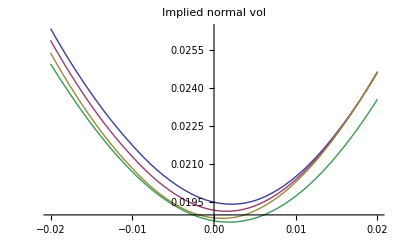
{55.099,-Graphics-}

```mathematica
Timing[Module[{S1=0.05,S2=0.05,K=0.00001,M1=-0.05,M2=-0.05,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1,ρm2,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,ν1=0.01,ν2=0.01,Lcoefs=LegendreCoeffs[40],
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=0,M,Σinf,Σ},scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=12;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=8;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.00001;
Nb2=10;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/10;ϵ2=0.00001;
Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
strikes={-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02};
ρm1=-0.5;ρm2=-0.5;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile000=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter000=Interpolation[smile000,InterpolationOrder->2];
ρm1=-0.5;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile001=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter001=Interpolation[smile001,InterpolationOrder->2];
ρm1=-0.5;ρm2=0.5;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile002=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter002=Interpolation[smile002,InterpolationOrder->2];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρ1,-M1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρ2,-M2,ν2,Lcoefs];ρsmod=ρs;
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρsmod,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter000[x],inter001[x],inter002[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston --","biheston -0","biheston -+","bilog"},LegendPosition->{1,0}]
]]
```

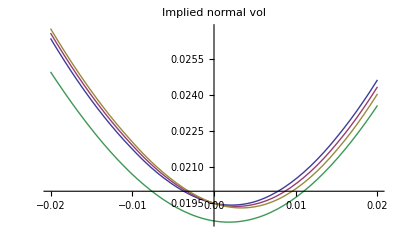
{56.254,-Graphics-}

```mathematica
Timing[Module[{S1=0.05,S2=0.05,K=0.00001,M1=-0.05,M2=-0.05,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1,ρm2,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,ν1=0.01,ν2=0.01,Lcoefs=LegendreCoeffs[40],
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=0,M,Σinf,Σ},scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=12;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=8;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.00001;
Nb2=10;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/10;ϵ2=0.00001;
Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
strikes={-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02};
ρm1=-0.5;ρm2=-0.5;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile000=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter000=Interpolation[smile000,InterpolationOrder->2];
ρm1=0.;ρm2=-0.5;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile001=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter001=Interpolation[smile001,InterpolationOrder->2];
ρm1=0.5;ρm2=-0.5;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile002=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter002=Interpolation[smile002,InterpolationOrder->2];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρ1,-M1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρ2,-M2,ν2,Lcoefs];ρsmod=ρs;
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρsmod,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter000[x],inter001[x],inter002[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston --","biheston 0-","biheston +-","bilog"},LegendPosition->{1,0}]
]]
```

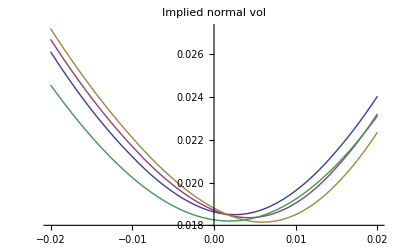
{65.115,-Graphics-}

```mathematica
Timing[Module[{S1=0.05,S2=0.05,K=0.00001,M1=-0.2,M2=-0.2,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1,ρm2,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,ν1=0.01,ν2=0.01,Lcoefs=LegendreCoeffs[40],
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=0,M,Σinf,Σ},scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=12;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=8;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.00001;
Nb2=10;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/10;ϵ2=0.00001;
Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
strikes={-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02};
ρm1=-0.5;ρm2=-0.5;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile000=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter000=Interpolation[smile000,InterpolationOrder->2];
ρm1=0.;ρm2=-0.5;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile001=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter001=Interpolation[smile001,InterpolationOrder->2];
ρm1=0.5;ρm2=-0.5;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile002=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,NewSuperBiHestonVanilla[strikes[[i]],τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]]},{i,1,Length[strikes]}];
inter002=Interpolation[smile002,InterpolationOrder->2];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρ1,-M1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρ2,-M2,ν2,Lcoefs];ρsmod=ρs;
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρsmod,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter000[x],inter001[x],inter002[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston --","biheston 0-","biheston +-","bilog"},LegendPosition->{1,0}]
]]
```

```mathematica
Timing[Module[{S1=0.05,S2=0.005,K=0.0000,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,
Nb2,LegendreCoef2,period2,period2n,ϵ2,printflag=2,M,Σinf,Σ},scope1=2/(√((Σ1+Σ2+θ1+θ2)/4 τ));scope2=3/(√((Σ1+Σ2+θ1+θ2)/4 τ));
Nb1=20;LegendreCoef1=LegendreCoeffs[Nb1];Nb1n=8;LegendreCoef1n=LegendreCoeffs[Nb1n];period1=scope1;period1n=scope1;ϵ1=0.00001;
Nb2=10;LegendreCoef2=LegendreCoeffs[Nb2];period2=scope2;period2n=scope2/10;ϵ2=0.00001;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});
{NewSuperBiHestonVanilla[K,τ,M,Σinf,{ρ1,ρ2}, Σ,{S1,S2},β,λ1,λ2,
{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},printflag]}]]
```

{NbLegendreCoef1,NbLegendreCoef1n,period1,period1n,ϵ1}={20,8,4.45823,4.45823,0.00001}

{NbLegendreCoef2,period2,period2n,ϵ2}={10,6.68734,0.668734,0.00001}

Integ_2={2,2.31505}

Integ_2={2,1.77644}

Integ_2={2,-0.0614284}

Integ_2={3,-0.69629}

Integ_2={3,0.169008}

Integ_2={3,0.0136468}

Integ_2={3,-0.0279515}

Integ_2={3,0.0118366}

Integ_2={2,0.00183024}

Integ_2={3,-0.00205849}

Integ_2={3,-0.00188577}

Integ_2={3,0.00029081}

Integ_2={3,0.000192339}

Integ_2={1,-0.0001716}

Integ_2={3,-7.4355×10^-6}

Integ_1={5,0.895297}

{2.403,{0.0453563}}